```mathematica
SetDirectory["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark\ matter\ capture/Tex\ Notes/"];
Needs["PlotLegends`"];
DG=Darker[Green];
DB=Darker[Blue];
```

## Compute <σv>_ANNas a function of mass and fraction of WIMPs

```mathematica
(*particle masses in GeV*)
(*gauge bosons*)
mW = 80.385;
mZ = 91.1876;
mH=125.09;
(*leptons*)
me=510.998928*^-6;
mmu=0.1056583715;
mtau=1.77686;
(*quarks*)
mu=2.3*^-3;
md=4.8*^-3;
ms=0.095;
mc=1.275;
mb=4.66;
mt=173.21;
Ωch2=0.1131;
mTab1=10^Range[Log10[4.95],4,.1];
mTab2=Range[15,70,1];
mTab=Sort[Join[mTab1,mTab2],Less];
NN=Length[mTab];
```

```mathematica
(*very simple calculation of g_**)grel[T_]:=(8*2+2+6*UnitStep[1-mW/T]+3*UnitStep[1-mZ/T]+UnitStep[1-mH/T])+7/8*(12*UnitStep[1-mu/T]+12*UnitStep[1-md/T]+12*UnitStep[1-ms/T]+12*UnitStep[1-mc/T]+12*UnitStep[1-mb/T]+12*UnitStep[1-mt/T]+4*UnitStep[1-me/T]+4*UnitStep[1-mmu/T]+4*UnitStep[1-mtau/T]+6);
```

```mathematica
(*get g_* from Steigman+12 PRD 86, 023506 Fig 2*)
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/RelicDensity/Steigman+Fig2.png.dat","Table"];
grel2=Interpolation[in,InterpolationOrder->1];
```

```mathematica
(*LogLinearPlot[{grel[T],grel2[T]},{T,1*^-3,1*^4},PlotRange->{{1*^-3,1*^4},{0,120}},Frame->True,FrameLabel->{"T [GeV]","g_*"}]*)
```

```mathematica
(*d(ln g)/d(ln T)*)
grellog[T_,d_] := (Log[grel2[T(1+d)]]-Log[grel2[T(1-d)]])/(Log[T(1+d)]-Log[T(1-d)]);
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/RelicDensity/dlng_dlnT.bmp.dat"];
grellog2=Interpolation[in,InterpolationOrder->1];
```

```mathematica
(*LogLinearPlot[{grellog[T,.21],grellog[T,.05],grellog[T,.1],grellog[T,.1],grellog2[T]},{T,10^-3,10^3},Frame->True,FrameLabel->{"T [GeV]", "d(lng)/d(lnT)"},PlotRange->{{10^-3,10^3},{-0.5,2.5}}]*)
```

```mathematica
(*get x_**)
xStar[sigv_,m_] := FindRoot[x+Log[x-1.5]-0.5Log[x]-20.5-Log[sigv*10*^26]-Log[m]+0.5Log[grel2[m/x]],{x,15}][[1,2]];
```

```mathematica
(*get T_**)
Tstar[sigv_,m_]:=m/xStar[sigv,m];
```

```mathematica
(*get g_**)
gstar[sigv_,m_]:=grel2[m/xStar[sigv,m]]
```

```mathematica
(*get (Γ/H)_**)
gamHstar[sigv_,m_]:=(1+0.618)(xStar[sigv,m]-3/2-grellog2[Tstar[sigv,m]])/(1+1/3  grellog2[Tstar[sigv,m]]);
```

```mathematica
(*get α_**)
astar[sigv_,m_]:=NIntegrate[1/Tstar[sigv,m] Sqrt[grel2[T]/grel2[Tstar[sigv,m]]] (1+1/3 grellog2[T]),{T,Tstar[sigv,m]/100,Tstar[sigv,m]}];
```

```mathematica
(*calculate Omega h^ 2*)
Omh[sigv_,m_]:=9.92*^-28/sigv (xStar[sigv,m]/Sqrt[gstar[sigv,m]])*gamHstar[sigv,m]/(1+astar[sigv,m]gamHstar[sigv,m]);
```

```mathematica
(*Steigman plot*)
(*ann=10^-26;LogLinearPlot[{Sqrt[gstar[ann,m]],xStar[ann,m],(1+0.618)(xStar[ann,m]-3/2),gamHstar[ann,m],50*astar[ann,m]},{m,10^-1,10^4},PlotRange->{{10^-1,10^4},{0,50}},Frame->True,FrameLabel->{"m [GeV]"}]*)
```

```mathematica
(*get Annhiliation Cross section as a function of Ωh^2, in m^3 s *)
OmhTarget:=Ωch2;
AnnStart=2*10^-26;
AnnFin1=ConstantArray[AnnStart,NN];
For[i=1,i≤NN,i++,{While[Omh[AnnFin1[[i]],mTab[[i]]]>OmhTarget,AnnFin1[[i]]=AnnFin1[[i]]*1.01],AnnFin1[[i]]=10^-6 AnnFin1[[i]]}];
AnnFun1=Interpolation[{mTab,AnnFin1}//Transpose];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14437242792210758`}. NIntegrate obtained 0.919811 and 2.4463×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14430900028763652`}. NIntegrate obtained 0.9198 and 9.56176×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.1442456279245094`}. NIntegrate obtained 0.919792 and 2.74518×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

```mathematica
OmhTarget=Ωch2*.1;
AnnStart=2*10^-25;
AnnFin2=AnnFin1;
For[i=1,i≤NN,i++,{While[Omh[AnnFin2[[i]],mTab[[i]]]>OmhTarget,AnnFin2[[i]]=AnnFin2[[i]]*1.01],AnnFin2[[i]]=10^-6 AnnFin2[[i]]}];
AnnFun2=Interpolation[{mTab,AnnFin2}//Transpose];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14489465538596122`}. NIntegrate obtained 0.92539 and 8.79656×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.1447399217789581`}. NIntegrate obtained 0.925333 and 8.57284×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.1445855053928393`}. NIntegrate obtained 0.925276 and 0.0000232485 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

```mathematica
OmhTarget=Ωch2*.01;
AnnStart=2*10^-24;
AnnFin3=AnnFin2;
For[i=1,i≤NN,i++,{While[Omh[AnnFin3[[i]],mTab[[i]]]>OmhTarget,AnnFin3[[i]]=AnnFin3[[i]]*1.01],AnnFin3[[i]]=10^-6 AnnFin3[[i]]}];
AnnFun3=Interpolation[{mTab,AnnFin3}//Transpose];
```

```mathematica
OmhTarget=Ωch2*.001;
AnnStart=2*10^-23;
AnnFin4=AnnFin3;
For[i=1,i≤NN,i++,{While[Omh[AnnFin4[[i]],mTab[[i]]]>OmhTarget,AnnFin4[[i]]=AnnFin4[[i]]*1.01],AnnFin4[[i]]=10^-6 AnnFin4[[i]]}];
AnnFun4=Interpolation[{mTab,AnnFin4}//Transpose];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14472522789502798`}. NIntegrate obtained 0.917841 and 3.13043×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14462139018857686`}. NIntegrate obtained 0.917884 and 0.0000145072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14451769938440281`}. NIntegrate obtained 0.917925 and 0.0000201166 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.3579519793839124`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.6929352649543746`} lies outside the range of data in the interpolating function. Extrapolation will be used.

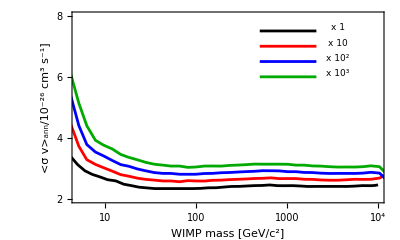

SigmaAnnPlot.png

```mathematica
(*Plotting the annihilation cross section vs. mass*)
thick1=0.005;
MyFrame=LogLinearPlot[-20,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{5,10^4},{2 10^-26,0.8 10^-25}},FrameTicks->{{{1,1},{10,10},{100,100},{1000,1000},{10^4,Superscript[10,4]}},{{2 10^-26,2},{3 10^-26,3},{4 10^-26,4},{5 10^-26,5},{6 10^-26,6},{7 10^-26,7},{8 10^-26,8},{9 10^-26,9}},{{1,""},{10,""},{100,""},{1000,""},{10^4,""}},{{2 10^-26,""},{3 10^-26,""},{4 10^-26,""},{5 10^-26,""},{6 10^-26,""},{7 10^-26,""},{8 10^-26,""},{9 10^-26,""}}},AspectRatio->0.6,FrameLabel->{{"<σ v>_ann/10^-26 cm^3 s^-1]",""},{"WIMP mass [GeV/c^2]",""}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"]];
Label1=LogLinearPlot[7.5 10^-26,{x,500,2100},PlotStyle->{Black,Thickness[thick1]}];
Label2=LogLinearPlot[7 10^-26,{x,500,2100},PlotStyle->{Red,Thickness[thick1]}];
Label3=LogLinearPlot[6.5 10^-26,{x,500,2100},PlotStyle->{Blue,Thickness[thick1]}];
Label4=LogLinearPlot[6 10^-26,{x,500,2100},PlotStyle->{Darker[Green],Thickness[thick1]}];
Sigma1=LogLinearPlot[10^6AnnFun1[mm],{mm,Log10[5],10^4},PlotStyle->{Black, Thickness[thick1]}];
Sigma2=LogLinearPlot[10^5AnnFun2[mm],{mm,0.5,1.6 10^4},PlotStyle->{Red, Thickness[thick1]}];
Sigma3=LogLinearPlot[10^4AnnFun3[mm],{mm,0.5,1.6 10^4},PlotStyle->{Blue, Thickness[thick1]}];
Sigma4=LogLinearPlot[10^3AnnFun4[mm],{mm,0.5,1.6 10^4},PlotStyle->{DG, Thickness[thick1]}];
SigmaAnnPlot=Show[MyFrame,Sigma1,Sigma2,Sigma3,Sigma4,Graphics[{EdgeForm[Thin],White,Rectangle[{6,Exp[-58.15]},{18,Exp[-57.7]}]}],Label1,Label2,Label3,Label4,Graphics[Text[Style["x 1",FontFamily->"Times",FontSize->9],{8.2,7.6 10^-26}]],Graphics[Text[Style["x 10",FontFamily->"Times",FontSize->9],{8.2,7.1  10^-26}]],Graphics[Text[Style["x 10^2",FontFamily->"Times",FontSize->9],{8.2,6.6 10^-26}]],Graphics[Text[Style["x 10^3",FontFamily->"Times",FontSize->9],{8.2,6.1  10^-26}]]]
Export["SigmaAnnPlot.pdf",SigmaAnnPlot,"pdf"]
```

## Constants

```mathematica
(*Constants*)
mHy=1.67 10^-27;(* Hydrogen mass in kg*)
cc=0.938/mHy; (* Conversion from kg to GeV *)
sW=0.124;
hbarc=0.2 10^-15; (* GeV m *)
GF=1.17 10^-5;(*Fermi constant, in GeV^-2*)
GN=6.67 10^-11(*Newton constant in SI*);
clight=3 10^8 (*speed of light in m/s*);
MPl=1.221 10^19(*Planck mass in GeV*);
DD=1.5 10^11 (*1 AU*);
KtoGeV=1.16 10^-13;

μA[mm_,mA_]:=mm mA/(mm/cc+mA)/cc; (*Reduced mass for nucleus-WIMP in kg*)
μH[mm_]:=μA[mm,mHy];(*Reduced mass for nucleon-WIMP in kg*)


(*Elements*)
AH1=1;(*Hydrogen*)
AHe4=4;(*Helium-4*)
AHe3=3;(*Helium-3*)
AC12=12;(*Carbon*)
AC13=13;(*Carbon*)
AN=14;(*Nitrogen*)
AO16=16;(*Oxygen*)
AO17=17;(*Oxygen*)
AO18=18;(*Oxygen*)
ANe=20;(*Neon*)
ANa=23;(*Sodium*)
AMg24=24;(*Magnesium*)
AMg25=25;(*Magnesium*)
AMg26=26;(*Magnesium*)
AAl=27;(*Aluminum*)
ASi28=28;(*Silicon*)
ASi29=29;(*Silicon*)
ASi30=30;(*Silicon*)
AP = 31; (*Phosphor*)
AS=32;(*Sulfur*)
AAr=40;(*Argon*)
ACa40=40;(*Calcium*)
ACa42=42;(*Calcium*)
ACa43=43;(*Calcium*)
ACa44=44;(*Calcium*)
ACa48=48;(*Calcium*)
ACr50 = 50; (*Chromium*)
ACr52 = 52; (*Chromium*)
ACr53 = 53; (*Chromium*)
ACr54 = 54; (*Chromium*)
AMn=55; (*Manganese*)
AFe54=54;(*Iron*)
AFe56=56;(*Iron*)
AFe57=57;(*Iron*)
AFe58=58;(*Iron*)
ANi58=58;(*Nickel*)
ANi60=60;(*Nickel*)
ANi61=61;(*Nickel*)
ANi62=62;(*Nickel*)
ANi64=64;(*Nickel*)

(*Oxygen abundances on Earth*)
xO16=0.99757;
xO17=3.8 10^-4;
xO18=2.05 10^-3;

(*Silicon abundance on Earth*)
xSi28=0.922297;
xSi29=0.046832;
xSi30=0.030872;

(*Magnesium isotopic abundance on Earth*)
xMg24=0.7899;
xMg25=0.1;
xMg26=0.1101;

(*Chromium isotopic abundance on Earth*)
xCr50=0.04345;
xCr52=0.83789;
xCr53=0.09501;
xCr54=0.02365;

(*Carbon isotopic abundance on Earth*)
xC12=0.9893;
xC13=0.0107;

(*Calcium isotopic abundance on Earth*)
xCa40=0.96941;
xCa42=6.47 10^-3;
xCa43=1.35 10^-3;
xCa44=0.02086;
xCa48=1.87 10^-3;

(*Iron abundances*)
xFe54=0.058;
xFe56=0.917;
xFe57=0.022;
xFe58=0.0028;

(*Nickel abundances*)
xNi58=0.681;
xNi60=0.262;
xNi61=0.011;
xNi62=0.036;
xNi64=0.009;



(*OGM Sp and Sn*)
OGMSp[mm_,JJ_]:=(mm-JJ)/4.586;
OGMSn[mm_]:=-mm/3.826;


(*Magnetic moment*)
μFe57=0.09044;
μNi61=-0.75002;
μCr53=-0.47454;
μCa43=-1.317643;

(*Nuclear spin*)
JH1=1/2;
JHe3=1/2;
JC13=1/2;
JN14=1;
JO17=5/2;
JNa23 = 3/2;
JMg25=5/2;
JAl27=5/2;
JSi29=1/2;
JP31=1/2;
JCa43=7/2;
JCr53=3/2;
JMn55=5/2;
JFe57=1/2;
JNi61=1/2;

(*expectation values of the proton spin in nuclei*)
SpH1 = 0.5;
SpHe3=0;
SpC13=-0.009;
SpN14=0.5;
SpO17=−0.036;
SpNa23=0.1566;
SpMg25=0.040;
SpAl27=0.333;
SpSi29=0.054;
SpP31=0.181;
SpCa43=0;
SpCr53=0;
SpMn55=0.264;
SpFe57=0.;
SpNi61=0.;

(*expectation values of the neutron spin in nuclei*)
SnH1=0;
SnHe3=0.5;
SnC13=−0.172;
SnN14=0.5;
SnO17=0.508;
SnNa23=0;
SnMg25=0.376;
SnAl27=0.043;
SnSi29=0.204;
SnP31=0.032;
SnCa43=OGMSn[μCa43];
SnCr53=OGMSn[μCr53];
SnMn55=0.;
SnFe57=OGMSn[μFe57];
SnNi61=OGMSn[μNi61];
```

## Sun Data

```mathematica
(*Density of the Sun as a function of radius, in kg/m^3*)
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/SolarData/Sun_density_profile.txt","Table"];
SunDensity1=Interpolation[in,InterpolationOrder->1]; (*In g/cm^3*)
SunDensity[r_]:=10^3 SunDensity1[r] (*rescale to kg/m^3*)

(*Temperature of the Sun as a function of radius, in kelvin*)
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/SolarData/Sun_temperature_profile.txt","Table"];
SunTemperature=Interpolation[in,InterpolationOrder->1];
```

```mathematica
(*Sun data*)
RSun=7 10^8; (*meters*)
MSun=2 10^30;
VSun=(4π RSun^3)/3;
ρSun=MSun/VSun; (*Mean density in kg/m^3*)
ρSunCore=150000;(*core density in kg/m^3*)
TSun=1.57 10^7 ;(*core temperature in Kelvin*)
ves=618 10^3; (*escape velocity at surface in m/s*)
vec=1381 10^3; (*escape velocity at core in m/s*)
(*veSun[r_]:=Sqrt[vec^2-Menc[r]/MSun(vec^2-ves^2)]; (*Average escape velocity in m/s*)*)
veSun=618 10^3;(*escape velocity in m/s when using ϕ*)

(* Sun mass fraction, from DarkSUSY*)
xHS=0.670;
xHe4S=0.311;
xHe3S=3.75 10^-4;
xCS=2.53 10^-3;
xNS=1.56 10^-3;
xOS=8.5 10^-3;
xNeS=1.92 10^-3;
xNaS=3.94 10^-5;
xMgS=7.33 10^-4;
xAlS=6.38 10^-5;
xSiS=7.98 10^-4;
xSS=5.48 10^-4;
xArS=8.04 10^-5;
xCaS=7.33 10^-5;
xFeS=1.42 10^-3;
xNi58S=8.40 10^-5 xNi58;
xNi60S=8.40 10^-5 xNi60;

(*gravitational potential*)
ϕHS=3.15;
ϕHe4S=3.40;
ϕHe3S=3.40;
ϕCS=2.85;
ϕNS=3.83;
ϕOS=3.25;
ϕNeS=3.22;
ϕNaS=3.22;
ϕMgS=3.22;
ϕAlS=3.22;
ϕSiS=3.22;
ϕSS=3.22;
ϕArS=3.22;
ϕCaS=3.22;
ϕFeS=3.22;
ϕNiS=3.22;

(*Vectors for the Sun, SI*)
xSunSI={xHS,xHe4S,xHe3S,xCS,xNS,xOS,xNeS,xNaS,xMgS,xAlS,xSiS,xSS,xArS,xCaS,xFeS,xNi58S,xNi60S};
ASunSI={AH1,AHe4,AHe3,AC12,AN,AO16,ANe,ANa,AMg24,AAl,ASi28,AS,AAr,ACa40,AFe56,ANi58,ANi60};
ϕSunSI={ϕHS,ϕHe4S,ϕHe3S,ϕCS,ϕNS,ϕOS,ϕNeS,ϕNaS,ϕMgS,ϕAlS,ϕSiS,ϕSS,ϕArS,ϕCaS,ϕFeS,ϕNiS,ϕNiS};
mSunSI=mHy ASunSI ;(*mass of each element in kg*)
LSunSI=Length[mSunSI]; (*Number of elements considered*)

(*Vectors for the Sun, SD*)
xSunSD={xHS,xHe3S,xNS,xNaS,xAlS};
ASunSD={AH1,AHe3,AN,ANa,AAl};
ϕSunSD={ϕHS,ϕHe3S,ϕNS,ϕNaS,ϕAlS};
SpSun={SpH1,SpHe3,SpN14,SpNa23,SpAl27};
SnSun={SnH1,SnHe3,SnN14,SnNa23,SnAl27};
JSun={JH1,JHe3,JN14,JNa23,JAl27};
mSunSD=mHy ASunSD;
LSunSD=Length[mSunSD];
```

## Earth Data

```mathematica
(*Density of the Earth as a function of radius, in kg/m^3*)
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/EarthData/Earth_density_profile.txt","Table"];
EarthDensity1=Interpolation[in,InterpolationOrder->1]; (*In g/cm^3*)
EarthDensity[r_]:=10^3 EarthDensity1[r] (*rescale to kg/m^3*)

(*Temperature of the Earth as a function of radius, in kelvin*)
in=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/EarthData/Earth_temperature_profile.txt","Table"];
EarthTemperature1=Interpolation[in,InterpolationOrder->1];
EarthTemperature[r_]:=KtoGeV EarthTemperature1[r];

rχEarthprof[rr_,mm_]:=Sqrt[6EarthTemperature[rr]/(π^2 GN EarthDensity[rr] mm)] clight/1000;(*1104.0679*)
rchiT= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{rc=FindRoot[rχEarthprof[rr,mTab[[i]]]==rr,{rr,6000}];rchiT[[i]]=10^3 rr/.rc}];
rchiEarth=Interpolation[Table[{mTab[[i]],rchiT[[i]]},{i,1,NN}],InterpolationOrder->1];
(*Subscript[r, χ] as a function of the WIMP mass, in meters. Use it for the annihilation and evaporation*)
```

```mathematica
(*Earth data*)
MEarth=6 10^24 ;(*kg*)
REarth=6.4 10^6; (*meters*)
VEarth=(4π REarth^3)/3;
ρEarth=MEarth/VEarth;
ρEarthCore=12000;(*core density in kg/m^3*)
TEarth=5700 ;(*core temperature in Kelvin*)
veEarth=11.2 10^3;

(*Earth mass fraction, McDonough 2014*)
xOE=0.297;
xSiE=0.161;
xFeE=0.32;
xMgE=0.154;
xNiE=0.0181;
xCrE=0.0047;
xCE=0.0007;
xCaE=0.0171;

xFe54E=xFeE xFe54;
xFe56E=xFeE xFe56;
xFe57E=xFeE xFe57;
xFe58E=xFeE xFe58;
xO16E=xOE xO16;
xO17E=xOE xO17;
xO18E=xOE xO18;
xSi28E=xSiE xSi28;
xSi29E=xSiE xSi29;
xSi30E=xSiE xSi30;
xMg24E=xMgE xMg24;
xMg25E=xMgE xMg25;
xMg26E=xMgE xMg26;
xNi58E= xNiE xNi58;
xNi60E= xNiE xNi60;
xNi61E= xNiE xNi61;
xNi62E= xNiE xNi62;
xNi64E= xNiE xNi64;
xCa40E=xCaE xCa40;
xCa42E=xCaE xCa42;
xCa43E=xCaE xCa43;
xCa44E=xCaE xCa44;
xCa48E=xCaE xCa48;
xAlE=0.0159;
xSE=0.0064;
xCr50E=xCrE xCr50;
xCr52E=xCrE xCr52;
xCr53E=xCrE xCr53;
xCr54E=xCrE xCr54;
xNaE=0.0018;
xPE=0.0007;
xMnE=0.0016;
xC12E=xCE xC12;
xC13E=xCE xC13;
xHE=0.0003;

(*gravitational potential*)
ϕFeE=1.54;
ϕOE=1.20;
ϕSiE=1.25;
ϕMgE=1.20;
ϕNiE=1.56;
ϕCaE=1.2;
ϕAlE=1.20;
ϕSE=1.58;
ϕCrE=1.45;
ϕNaE=1.20;
ϕPE=1.56;
ϕMnE=1.54;
ϕCE=1.64;
ϕHE=1.35;


(*Vectors for the Earth*)
(*xEarth={xFe54E,xFe56E,xFe57E,xFe58E,xO16E,xO17E,xO18E,xSi28E,xSi29E,xSi30E,xMg24E,xMg25E,xMg26E,xNi58E,xNi60E,xNi61E,xNi62E,xNi64E,xCa40E,xCa42E,xCa43E,xCa44E,xCa48E,xAlE,xSE,xCr50E,xCr52E,xCr53E,xCr54E,xNaE,xPE,xMnE,xC12E,xC13E,xHE};
AEarth={AFe54,AFe56,AFe57,AFe58,AO16,AO17,AO18,ASi28,ASi29,ASi30,AMg24,AMg25,AMg26,ANi58,ANi60,ANi61, ANi62, ANi64, ACa40,ACa42,ACa43,ACa44,ACa48,AAl,AS,ACr50,ACr52,ACr53,ACr54,ANa,AP,AMn,AC12,AC13,AH1};
ϕEarth={ϕFeE,ϕFeE,ϕFeE,ϕFeE,ϕOE,ϕOE,ϕOE,ϕSiE,ϕSiE,ϕSiE,ϕMgE,ϕMgE,ϕMgE,ϕNiE,ϕNiE,ϕNiE,ϕNiE,ϕNiE,ϕCaE,ϕCaE,ϕCaE,ϕCaE,ϕCaE,ϕAlE,ϕSE,ϕCrE,ϕCrE,ϕCrE,ϕCrE,ϕNaE,ϕPE,ϕMnE,ϕCE,ϕCE,ϕHE};
mEarth=mHy AEarth ;(*mass of each element in kg*)
LEarth=Length[mEarth] ;(*Number of elements considered*)
μA[mm_,mA_]:=mm mA/(mm/cc+mA)/cc; (*Reduced mass for nucleus-WIMP in kg*)
μH[mm_]:=μA[mm,mHy];(*Reduced mass for nucleon-WIMP in kg*)
μSun=Sum[mSun[[i]] xSun[[i]],{i,1,LSun}];(*Mean molecular mass of the Sun in kg*)
μEarth=Sum[mEarth[[i]] xEarth[[i]],{i,1,LEarth}];(*Mean molecular mass of the Earth in kg*)*)

(*Vectors for the Earth SI*)
xEarthSI={xFeE,xOE,xSiE,xMgE,xNiE,xCaE,xAlE,xSE,xCrE,xNaE,xPE,xMnE,xCE,xHE};
AEarthSI={AFe56,AO16,ASi28,AMg24,ANi58,ACa40,AAl,AS,ACr52,ANa,AP,AMn,AC12,AH1};
ϕEarthSI={ϕFeE,ϕOE,ϕSiE,ϕMgE,ϕNiE,ϕCaE,ϕAlE,ϕSE,ϕCrE,ϕNaE,ϕPE,ϕMnE,ϕCE,ϕHE};
mEarthSI=mHy AEarthSI;(*mass of each element in kg*)
LEarthSI=Length[mEarthSI] ;(*Number of elements considered*)

(*Vectors for the Earth, SD*)
xEarthSD={xFe57E,xO17E,xSi29E,xMg25E,xNi61E,xCa43E,xAlE,xCr53E,xNaE,xPE,xMnE,xC13E,xHE};
AEarthSD={AFe57,AO17,ASi29,AMg25,ANi61,ACa43,AAl,ACr53,ANa,AP,AMn,AC13,AH1};
ϕEarthSD={ϕFeE,ϕOE,ϕSiE,ϕMgE,ϕNiE,ϕCaE,ϕAlE,ϕCrE,ϕNaE,ϕPE,ϕMnE,ϕCE,ϕHE};
SpEarth={SpFe57,SpO17,SpSi29,SpMg25,SpNi61,SpCa43,SpAl27,SpCr53,SpNa23,SpP31,SpMn55,SpC13,SpH1};
SnEarth={SnFe57,SnO17,SnSi29,SnMg25,SnNi61,SnCa43,SnAl27,SnCr53,SnNa23,SnP31,SnMn55,SnC13,SnH1};
JEarth={JFe57,JO17,JSi29,JMg25,JNi61,JCa43,JAl27,JCr53,JNa23,JP31,JMn55,JC13,JH1};
mEarthSD=mHy AEarthSD;
LEarthSD=Length[mEarthSD];

(*Vectors for the Earth, SD as in DarkSUSY*)
xEarthSDDS={xAlE,xNaE,xPE};
AEarthSDDS={AAl,ANa,AP};
ϕEarthSDDS={ϕAlE,ϕNaE,ϕPE};
SpEarthDS={SpAl27,SpNa23,SpP31};
SnEarthDS={SnAl27,SnNa23,SnP31};
JEarthDS={JAl27,JNa23,JP31};
mEarthSDDS=mHy AEarthSDDS;(*mass of each element in kg*)
LEarthSDDS=Length[mEarthSDDS] ;(*Number of elements considered*)
```

## Introduce the capture rate functions for the Sun and the Earth

```mathematica
σSI=10^-44 10^-4;(*Reference SI cross section in m^2*)
σSD=10^-38 10^-4;(*Reference SD cross section in m^2*)

(*DM number density in m^-3; mm is the DM mass in GeV*)
nDM0[mm_,fcdm_]:= (0.4 fcdm)/(10^-6 mm); (*fcdm is the fraction of WIMP energy density contributing to the total CDM budget*)

Subscript[v, σ] =270 10^3;(*Standard dark matter halo velocity dispersion in m/s*)
vsol=220 10^3;(*speed of the solar system in the WIMP halo*)
η=Sqrt[3/2] vsol/Subscript[v, σ];
yS:=Sqrt[3/2] veSun/Subscript[v, σ];
yE:=Sqrt[3/2] veEarth/Subscript[v, σ];


ff0[x_]:=4/π^(1/2)x^2 Exp[-x^2];(*In this distribution, the Sun is still*)

ff[x_]:=4/π^(1/2)x Exp[-x^2-η^2] Sinh[2 x η]/(2 η);(*In this distribution, the solar system moves in the WIMP background with velocity vsun (in m/s). We use this distribution*)


xmaxS[mm_,mN_]:=Sqrt[3/2] veSun/Subscript[v, σ] Sqrt[(4 mN mm /cc)/(mm/cc-mN)^2];
xmaxE[mm_,mN_]:=Sqrt[3/2] veEarth/Subscript[v, σ] Sqrt[(4 mN mm /cc)/(mm/cc-mN)^2];


RA[mN_]:=0.91 (cc mN)^(1/3)+0.3 (*Radius in fermi*)
EQ[mN_]:=3/(2mN cc (0.91 (mN cc)^(1/3)+0.3)^2)(0.2^2  1.6022 10^-10) (*Form factor energy cutoff in Joules*)
(*0.2 converts from fm to GeV and 1.6022 10^-10 converts from GeV to Joules*)

(*Limits of integration in ER*)

Emin[mm_,x_]:=(Subscript[v, σ]^2 mm/cc)/3 x^2; (*In Joules*)
Emax[mm_,mN_,x_,y_]:=(4 Subscript[v, σ]^2 μA[mm,mN]^2)/(3mN)(x^2+y^2);(*In Joules*)

R1[mN_]:=Sqrt[(1.23(mN/mHy)^(1/3)-0.6)^2+2.177] (*Effective nuclear radius in fermi*)

zmin[mm_,mN_,x_]:=Emin[mm,x] R1[mN];
zmax[mm_,mN_,x_,y_]:=Emax[mm,mN,x,y] R1[mN]

FSD2[z_]:=If[z≤2.55 ||z ≥ 4.5,SphericalBesselJ[0,z]^2,0.047];

FormFactorSI[mm_,mN_,x_,y_]:=EQ[mN]/2 (ⅇ^(-(2 Emin[mm,x])/EQ[mN])-ⅇ^(-(2 Emax[mm,mN,x,y])/EQ[mN]));(*Integral of F(ER)^2 in joules*)

(*FormFactorSD[mm_,mN_,x_,y_]:=NIntegrate[FSD2[z],{z,zmin[mm,mN,x],zmax[mm,mN,x,y]}]/R1[mN];*)

FormFactorSD[mm_,mN_,x_,y_]:=Emax[mm,mN,x,y] - Emin[mm,x];


(*(*Toy model for the Sun*)
ClearAll[CToySun]
CToySun[mm_,ss_,fcdm_]:=Sqrt[6/π](nDM0[mm,fcdm] MSun veSun^2 σSI ss)/(μH[mm]^2 Subscript[v, σ])  Sum[ASun[[i]]^2 xSun[[i]]ϕSun[[i]] μA[mm,mSun[[i]]]^2/mSun[[i]](1-(1-Exp[-(xmaxS[mm,mSun[[i]]])^2])/(xmaxS[mm,mSun[[i]]])^2),{i,1,LSun}];


(*Toy model for the Earth*)
ClearAll[CToyEarth]
CToyEarth[mm_,ss_,fcdm_]:=Sqrt[6/π](nDM0[mm,fcdm] MEarth veEarth^2 σSI ss)/(μH[mm]^2 Subscript[v, σ])  Sum[AEarth[[i]]^2 xEarth[[i]]ϕEarth[[i]] μA[mm,mEarth[[i]]]^2/mEarth[[i]](1-(1-Exp[-(xmaxE[mm,mEarth[[i]]])^2])/(xmaxE[mm,mEarth[[i]]])^2),{i,1,LEarth}];*)


(*Capture rate SI Sun*)
ClearAll[CSunSI]
CSunSI[mm_,ss_,fcdm_]:=(nDM0[mm,fcdm] MSun σSI ss)/(2 μH[mm]^2 Subscript[v, σ]) Sum[ ASunSI[[i]]^2 xSunSI[[i]]ϕSunSI[[i]] NIntegrate[ff[x]/x FormFactorSI[mm,mSunSI[[i]],x,yS],{x,0,xmaxS[mm,mSunSI[[i]]]}],{i,1,LSunSI}];

(*Capture rate SI Earth*)
ClearAll[CEarthSI]
(*CEarthSI[mm_,ss_,fcdm_]:=(nDM0[mm,fcdm] MEarth σSI ss)/(2 μH[mm]^2 Subscript[v, σ]) Sum[ AEarth[[i]]^2 xEarth[[i]]ϕEarth[[i]] NIntegrate[ff[x]/x FormFactorSI[mm,mEarth[[i]],x,yE],{x,0,xmaxE[mm,mEarth[[i]]]}],{i,1,LEarth}];

CEarthSIElement[mm_,ss_,fcdm_,i_]:=(nDM0[mm,fcdm] MEarth σSI ss)/(2 μH[mm]^2 Subscript[v, σ])  AEarth[[i]]^2 xEarth[[i]]ϕEarth[[i]] NIntegrate[ff[x]/x FormFactorSI[mm,mEarth[[i]],x,yE],{x,0,xmaxE[mm,mEarth[[i]]]}];*)

CEarthSI[mm_,ss_,fcdm_]:=(nDM0[mm,fcdm] MEarth σSI ss)/(2 μH[mm]^2 Subscript[v, σ]) Sum[ AEarthSI[[i]]^2 xEarthSI[[i]]ϕEarthSI[[i]] NIntegrate[ff[x]/x FormFactorSI[mm,mEarthSI[[i]],x,yE],{x,0,xmaxE[mm,mEarthSI[[i]]]}],{i,1,LEarthSI}];

(*Capture rate SD Sun*)
ClearAll[CSunSD]
CSunSD[mm_,ss_,fcdm_]:=(2nDM0[mm,fcdm] MSun σSD ss)/(3 μH[mm]^2 Subscript[v, σ]) Sum[xSunSD[[i]]ϕSunSD[[i]](SpSun[[i]]+SnSun[[i]])^2(JSun[[i]]+1)/JSun[[i]] NIntegrate[ff[x]/x FormFactorSD[mm,mSunSD[[i]],x,yS],{x,0,xmaxS[mm,mSunSD[[i]]]}],{i,1,LSunSD}];

CSunSDElement[mm_,ss_,fcdm_,i_]:=(2nDM0[mm,fcdm] MSun σSD ss)/(3 μH[mm]^2 Subscript[v, σ]) xSunSD[[i]]ϕSunSD[[i]](SpSun[[i]]+SnSun[[i]])^2(JSun[[i]]+1)/JSun[[i]] NIntegrate[ff[x]/x FormFactorSD[mm,mSunSD[[i]],x,yS],{x,0,xmaxS[mm,mSunSD[[i]]]}];


(*Capture rate SD Earth*)
ClearAll[CEarthSD]
CEarthSD[mm_,ss_,fcdm_]:=(nDM0[mm,fcdm] MEarth σSD ss)/(2 μH[mm]^2 Subscript[v, σ]) Sum[xEarthSD[[i]]ϕEarthSD[[i]] (SpEarth[[i]]+SnEarth[[i]])^2(JEarth[[i]]+1)/JEarth[[i]] NIntegrate[ff[x]/x FormFactorSD[mm,mEarthSD[[i]],x,yE],{x,0,xmaxE[mm,mEarthSD[[i]]]}],{i,1,LEarthSD}];

(*Capture rate SD Earth, DarkSUSY*)
ClearAll[CEarthSDDS]
CEarthSDDS[mm_,ss_,fcdm_]:=(nDM0[mm,fcdm] MEarth σSD ss)/(2 μH[mm]^2 Subscript[v, σ]) Sum[xEarthSDDS[[i]]ϕEarthSDDS[[i]] (SpEarthDS[[i]]+SnEarthDS[[i]])^2(JEarthDS[[i]]+1)/JEarthDS[[i]] NIntegrate[ff[x]/x FormFactorSD[mm,mEarthSDDS[[i]],x,yE],{x,0,xmaxE[mm,mEarthSDDS[[i]]]}],{i,1,LEarthSDDS}];

(*CEarthSDElement[mm_,ss_,fcdm_,i_]:=(nDM0[mm,fcdm] MEarth σSD ss)/(2 μH[mm]^2 Subscript[v, σ]) xEarthSD[[i]]ϕEarthSD[[i]] (SpEarth[[i]]+SnEarth[[i]])^2(JEarth[[i]]+1)/JEarth[[i]] NIntegrate[ff[x]/x FormFactorSD[mm,mEarthSD[[i]],x,yE],{x,0,xmaxE[mm,mEarthSD[[i]]]}]*)

(* Annihilation rate *)
TSev = TSun KtoGeV; (*Temperature of the Sun core in GeV*)
rχSun[mm_]:=Sqrt[3TSev/(2π GN ρSunCore mm)] clight;(*Thermal radius of the Sun in meters*)

TEev = TEarth KtoGeV; (*Temperature of the Earth core in GeV*)
rχEarth[mm_]:=Sqrt[3TEev/(2π GN ρEarthCore mm)] clight;(*Thermal radius of the Earth in meters*)


(* fcdm is the fraction of WIMP energy density contributing to the total CDM budget *)
Ωch2=0.1131;
σAnn[mm_,fcdm_]:=AnnFun1[mm]/fcdm;(*The approximation works in the range of interest*)

(*σAn[fcdm_]:=(3 10^-27 10^-6)/(Ωch2 fcdm)(*m^3/s*);*)

(*Annihilation rate*)
CASun[mm_,fcdm_]:=(σAnn[mm,fcdm](-4 ⅇ^(-(2 RSun^2)/rχSun[mm]^2) RSun/rχSun[mm]+√(2 π) Erf[(√2 RSun)/rχSun[mm]]))/(2 π rχSun[mm]^3 (-2 ⅇ^(-RSun^2/rχSun[mm]^2) RSun/rχSun[mm]+√π Erf[RSun/rχSun[mm]])^2)  ;
CAEarth[mm_,fcdm_]:=(σAnn[mm,fcdm](-4 ⅇ^(-(2 REarth^2)/rχEarth[mm]^2) REarth/rχEarth[mm]+√(2 π) Erf[(√2 REarth)/rχEarth[mm]]))/(2 π rχEarth[mm]^3 (-2 ⅇ^(-REarth^2/rχEarth[mm]^2) REarth/rχEarth[mm]+√π Erf[REarth/rχEarth[mm]])^2)  ;


Veff[mm_]:=2 π rχSun[mm]^3 (-2 ⅇ^(-RSun^2/rχSun[mm]^2) RSun/rχSun[mm]+√π Erf[RSun/rχSun[mm]])^2/(-4 ⅇ^(-(2 RSun^2)/rχSun[mm]^2) RSun/rχSun[mm]+√(2 π) Erf[(√2 RSun)/rχSun[mm]]);
τSun=4.6 10^9 3.15 10^7;(*Age of the solar system in seconds*)

(*Relaxation time τA*)
τASunSI[mm_,ss_,fcdm_]:=1/Sqrt[CSunSI[mm,ss,fcdm] CASun[mm,fcdm]]/τSun;
τAEarthSI[mm_,ss_,fcdm_]:=1/Sqrt[CEarthSI[mm,ss,fcdm] CAEarth[mm,fcdm]]/τSun;
(*τA divided by the age of the Sun for SI*)

τASunSD[mm_,ss_,fcdm_]:=1/Sqrt[CSunSD[mm,ss,1] CASun[mm,fcdm]]/τSun;
τAEarthSD[mm_,ss_,fcdm_]:=1/Sqrt[CEarthSD[mm,ss,fcdm] CAEarth[mm,fcdm]]/τSun;
τAEarthSDDS[mm_,ss_,fcdm_]:=1/Sqrt[CEarthSDDS[mm,ss,fcdm] CAEarth[mm,fcdm]]/τSun;
(*τA divided by the age of the Sun for SD*)

(*(*Relaxation time for Subscript[σv, ANN] = 3 10^-25*)
τASunSI01[mm_,ss_]:=1/Sqrt[CSunSI[mm,ss,0.1] CASun01[mm]]/τSun;
τASunSD01[mm_,ss_]:=1/Sqrt[CSunSD[mm,ss,0.1] CASun01[mm]]/τSun;
τAEarthSI01[mm_,ss_]:=1/Sqrt[CEarthSI[mm,ss,0.1] CAEarth01[mm]]/τSun;
τAEarthSD01[mm_,ss_]:=1/Sqrt[CEarthSD[mm,ss,0.1] CAEarth01[mm]]/τSun;

(*Relaxation time for Subscript[σv, ANN] = 3 10^-24*)
τASunSI001[mm_,ss_]:=1/Sqrt[CSunSI[mm,ss,0.01] CASun001[mm]]/τSun;
τASunSD001[mm_,ss_]:=1/Sqrt[CSunSD[mm,ss,0.01] CASun001[mm]]/τSun;
τAEarthSI001[mm_,ss_]:=1/Sqrt[CEarthSI[mm,ss,0.01] CAEarth001[mm]]/τSun;
τAEarthSD001[mm_,ss_]:=1/Sqrt[CEarthSD[mm,ss,0.01] CAEarth001[mm]]/τSun;*)
```

```mathematica
NSSI0[mm_,ss_,fcdm_]:=√(CSunSI[mm,ss,fcdm]/CASun[mm,fcdm])Tanh[1/τASunSI[mm,ss,fcdm]];
NESI0[mm_,ss_,fcdm_]:=√(CEarthSI[mm,ss,fcdm]/CAEarth[mm,fcdm])Tanh[1/τAEarthSI[mm,ss,fcdm]];
```

```mathematica
NSSI0[100,1,1]
```

1.54945×10^37

```mathematica
NSSI0[100,1,1] 100 1.67 10^-27/10^30
NESI0[100,1,1] 100 1.67 10^-27/10^24
```

2.58758×10^-18

3.40948×10^-20

```mathematica
NSSI0[100,1,1]
```

1.54945×10^37

```mathematica
CSunSI[100,1,1]
```

1.0336×10^21

```mathematica
τASunSI[100,1,1]
```

0.103456

## Evaporation as in Gould 1987 Eq. 3.17, with E_e computed as in 1104.0679

```mathematica
Esun[mm_]:=mm/(2 TSev)(1400000/clight)^2;
(*Eearth[mm_]:=mm/(2 TEev)(15000/clight)^2;*)
Eearth[mm_]:=mm/(2 EarthTemperature[rchiEarth[mm]])(15000/clight)^2;
EvapSSI[mm_,ss_,fcdm_]:=(2σSI clight)/(√π)nDM0[mm,fcdm] ss √((2TSev)/mm)Exp[-Esun[mm]] Esun[mm]Sum[(xSunSI[[i]] MSun)/mSunSI[[i]] ASunSI[[i]]^2(μA[mm,mSunSI[[i]]]^2/μH[mm]^2)^2,{i,1,LSunSI}];EvapSSD[mm_,ss_,fcdm_]:=(2σSD clight)/(√π) nDM0[mm,fcdm]ss √((2TSev)/mm)Exp[-Esun[mm]] Esun[mm]Sum[(xSunSD[[i]] MSun)/mSunSD[[i]](μA[mm,mSunSD[[i]]]^2/μH[mm]^2)^2 4/3(SpSun[[i]]+SnSun[[i]])^2(JSun[[i]]+1)/JSun[[i]],{i,1,LSunSD}];EvapESI[mm_,ss_,fcdm_]:=(2σSI clight)/(√π)nDM0[mm,fcdm] ss √((2TEev)/mm)Exp[-Eearth[mm]] Eearth[mm]Sum[(xEarthSI[[i]] MEarth)/mEarthSI[[i]] AEarthSI[[i]]^2(μA[mm,mEarthSI[[i]]]^2/μH[mm]^2)^2,{i,1,LEarthSI}];
EvapESD[mm_,ss_,fcdm_]:=(2σSD clight)/(√π)nDM0[mm,fcdm] ss √((2TEev)/mm)Exp[-Eearth[mm]] Eearth[mm]Sum[(xEarthSD[[i]] MEarth)/mEarthSD[[i]](μA[mm,mEarthSD[[i]]]^2/μH[mm]^2)^2 4/3(SpEarth[[i]]+SnEarth[[i]])^2(JEarth[[i]]+1)/JEarth[[i]],{i,1,LEarthSD}];

αSSI[mm_,ss_,fcdm_]:=Sqrt[1+(EvapSSI[mm,ss,fcdm]τASunSI[mm,ss,fcdm]τSun/2)^2];
αSSD[mm_,ss_,fcdm_]:=Sqrt[1+(EvapSSD[mm,ss,fcdm]τASunSD[mm,ss,fcdm]τSun/2)^2];
αESI[mm_,ss_,fcdm_]:=Sqrt[1+(EvapESI[mm,ss,fcdm]τAEarthSI[mm,ss,fcdm]τSun/2)^2];
αESD[mm_,ss_,fcdm_]:=Sqrt[1+(EvapESD[mm,ss,fcdm]τAEarthSD[mm,ss,fcdm]τSun/2)^2];
```

```mathematica
(*Number of WIMPs captured today*)
NSSI0[mm_,ss_,fcdm_]:=√(CSunSI[mm,ss,fcdm]/CASun[mm,fcdm])Tanh[1/τASunSI[mm,ss,fcdm]];
NSSI[mm_,ss_,fcdm_]:=√(CSunSI[mm,ss,fcdm]/CASun[mm,fcdm]) Tanh[αSSI[mm,ss,fcdm]/τASunSI[mm,ss,fcdm]]/(αSSI[mm,ss,fcdm]+√(αSSI[mm,ss,fcdm]^2-1) Tanh[αSSI[mm,ss,fcdm]/τASunSI[mm,ss,fcdm]]);
NESI0[mm_,ss_,fcdm_]:=√(CEarthSI[mm,ss,fcdm]/CAEarth[mm,fcdm])Tanh[1/τAEarthSI[mm,ss,fcdm]];
NESI[mm_,ss_,fcdm_]:=√(CEarthSI[mm,ss,fcdm]/CAEarth[mm,fcdm]) Tanh[αESI[mm,ss,fcdm]/τAEarthSI[mm,ss,fcdm]]/(αESI[mm,ss,fcdm]+√(αESI[mm,ss,fcdm]^2-1) Tanh[αESI[mm,ss,fcdm]/τAEarthSI[mm,ss,fcdm]]);
NSSD0[mm_,ss_,fcdm_]:=√(CSunSD[mm,ss,fcdm]/CASun[mm,fcdm])Tanh[1/τASunSD[mm,ss,fcdm]];
NSSD[mm_,ss_,fcdm_]:=√(CSunSD[mm,ss,fcdm]/CASun[mm,fcdm]) Tanh[αSSD[mm,ss,fcdm]/τASunSD[mm,ss,fcdm]]/(αSSD[mm,ss,fcdm]+√(αSSD[mm,ss,fcdm]^2-1) Tanh[αSSD[mm,ss,fcdm]/τASunSD[mm,ss,fcdm]]);
NESD0[mm_,ss_,fcdm_]:=√(CEarthSI[mm,ss,fcdm]/CAEarth[mm,fcdm])Tanh[1/τAEarthSI[mm,ss,fcdm]];
NESD[mm_,ss_,fcdm_]:=√(CEarthSD[mm,ss,fcdm]/CAEarth[mm,fcdm]) Tanh[αESD[mm,ss,fcdm]/τAEarthSD[mm,ss,fcdm]]/(αESD[mm,ss,fcdm]+√(αESD[mm,ss,fcdm]^2-1) Tanh[αESD[mm,ss,fcdm]/τAEarthSD[mm,ss,fcdm]]);
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

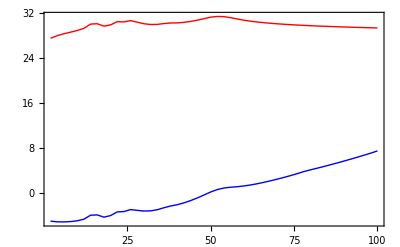

```mathematica
NNN=50;
mT=Table[2i,{i,1,NNN}];
mN1=mT;
mN2=mT;
For[i=1,i≤NNN,i++,{mN1[[i]]=NESI0[mT[[i]],1,1];mN2[[i]]=NESI[mT[[i]],1,1]}]
AE1=ListLinePlot[Table[{mT[[i]],Log10[mN1[[i]]]},{i,1,NNN}],PlotStyle->Red];
AE2=ListLinePlot[Table[{mT[[i]],Log10[mN2[[i]]]},{i,1,NNN}],PlotStyle->Blue];
Show[AE2,AE1,PlotRange->All,Frame->True,Axes->False]
```

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

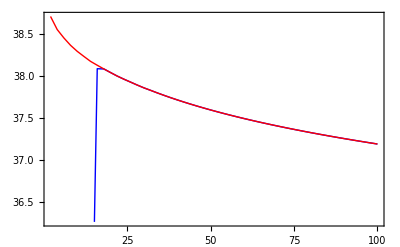

```mathematica
NNN=50;
mT=Table[2i,{i,1,NNN}];
mN1=mT;
mN2=mT;
For[i=1,i≤NNN,i++,{mN1[[i]]=NSSI0[mT[[i]],1,1];mN2[[i]]=NSSI[mT[[i]],1,1]}]
A1=ListLinePlot[Table[{mT[[i]],Log10[mN1[[i]]]},{i,1,NNN}],PlotStyle->Red];
A2=ListLinePlot[Table[{mT[[i]],Log10[mN2[[i]]]},{i,1,NNN}],PlotStyle->Blue];
Show[A2,A1,PlotRange->All,Frame->True,Axes->False]
```

```mathematica
(*μr[mm_,mN_]=(mm/cc)/mN; (*Dimension-less*)
μp[mm_,mN_]:=(μr[mm,mN]+1)/2;(*Dimension-less*)
μm[mm_,mN_]:=Abs[μr[mm,mN]-1]/2;(*Dimension-less*)
αp[mm_,mN_,TT_,x_,y_]:=√(mN/(2TT/cc))(μp[mm,mN] y+μm[mm,mN] x);(*Dimension-less; TT in GeV*)
αm[mm_,mN_,TT_,x_,y_]:=√(mN/(2TT/cc))(μp[mm,mN] y-μm[mm,mN] x);(*Dimension-less; TT in GeV*)
βp[mm_,mN_,TT_,x_,y_]:=√(mN/(2TT/cc))(μm[mm,mN] y+μp[mm,mN] x);(*Dimension-less; TT in GeV*)
βm[mm_,mN_,TT_,x_,y_]:=√(mN/(2TT/cc))(μm[mm,mN] y-μp[mm,mN] x);(*Dimension-less; TT in GeV*)

A1[mm_,mN_,TT_,x_,y_]:=μr[mm,mN] (αp[mm,mN,TT,x,y] Exp[-αm[mm,mN,TT,x,y]^2]-αm[mm,mN,TT,x,y] Exp[-αp[mm,mN,TT,x,y]^2]);
A2[mm_,mN_,TT_,x_,y_]:=(μr[mm,mN]-2, μr[mm,mN] αp[mm,mN,TT,x,y] αm[mm,mN,TT,x,y]-2 μp[mm,mN] μm[mm,mN])Erf[αm[mm,mN,TT,x,y],αp[mm,mN,TT,x,y]];
A3[mm_,mN_,TT_,x_,y_]:=2 μp[mm,mN]^2 Erf[βm[mm,mN,TT,x,y],βp[mm,mN,TT,x,y]]Exp[-mm/(3TT)(Subscript[v, σ]/clight)^2(y^2-x^2)];
RRSISun[mm_,mN_,x_,y_]:=1/(√π)TT/mN (σ x)/(x μr[mm,mN]^2) (A1[mm,mN,TSev,x,y]+A2[mm,mN,TSev,x,y]+A3[mm,mN,TEev,x,y] );
RRSDSun[mm_,mN_,x_,y_]:=1/(√π)TT/mN (σ x)/(x μr[mm,mN]^2) (A1[mm,mN,TSev,x,y]+A2[mm,mN,TSev,x,y]+A3[mm,mN,TEev,x,y] );
RRSIEarth[mm_,mN_,x_,y_]:=1/(√π)TT/mN (σ x)/(x μr[mm,mN]^2) (A1[mm,mN,TEev,x,y]+A2[mm,mN,TEev,x,y]+A3[mm,mN,TEev,x,y] );
RRSDEarth[mm_,mN_,x_,y_]:=1/(√π)TT/mN (σ x)/(x μr[mm,mN]^2) (A1[mm,mN,TEev,x,y]+A2[mm,mN,TEev,x,y]+A3[mm,mN,TEev,x,y] );
CESI[mm_,mN_,x_,y_,TT_,fcdm_]:=NIntegrate[4π rr^2 ff[x] nDM0[mm,fcdm] Exp[-(rr/rχEarth[mm])^2]RR[mm,mN,x,y,TT],{rr,0,REarth},{x,0,Infinity}]/NIntegrate[4π rr^2 Exp[-(rr/rχEarth[mm])^2],{rr,0,REarth}];
CESI[mm_,mN_,x_,y_,TT_,fcdm_]:=NIntegrate[4π rr^2 ff[x] nDM0[mm,fcdm] Exp[-(rr/rχEarth[mm])^2]RR[mm,mN,x,y,TT],{rr,0,REarth},{x,0,Infinity}]/NIntegrate[4π rr^2 Exp[-(rr/rχEarth[mm])^2],{rr,0,REarth}];
CESD[mm_,mN_,x_,y_,TT_,fcdm_]:=NIntegrate[4π rr^2 ff[x] nDM0[mm,fcdm] Exp[-(rr/rχEarth[mm])^2]RR[mm,mN,x,y,TT],{rr,0,REarth},{x,0,Infinity}]/NIntegrate[4π rr^2 Exp[-(rr/rχEarth[mm])^2],{rr,0,REarth}];
CESD[mm_,mN_,x_,y_,TT_,fcdm_]:=NIntegrate[4π rr^2 ff[x] nDM0[mm,fcdm] Exp[-(rr/rχEarth[mm])^2]RR[mm,mN,x,y,TT],{rr,0,REarth},{x,0,Infinity}]/NIntegrate[4π rr^2 Exp[-(rr/rχEarth[mm])^2],{rr,0,REarth}];*)
```

## Spin Independent Capture rate in the Sun

```mathematica
(*define frame sizes*)
x1=300;
y1=250;
pxr1=10;
pxl1=1;
pyu1=6;
pyd1=5;
pxax1=50;
pyax1=50;
thick=0.0055;
labelstyle={Bold,14};
ylabC=Row[{"Log_10 Capture rate [",Superscript["s",-1],"]"}];
ylabSI=Row[{"Log_10 ",Subsuperscript["σ","p","SI"]," / ",Superscript["cm",2]}];
ylabSD=Row[{"Log_10 ",Subsuperscript["σ","p","SD"]," / ",Superscript["cm",2]}];
```

```mathematica
(*Compute the capture rate*)
CTable1=Table[1,{i,1,NN}];
CTable01=Table[1,{i,1,NN}];
CTable001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTable1[[i]]=CSunSI[mTab[[i]],1,1];CTable01[[i]]=CSunSI[mTab[[i]],0.1,1];CTable001[[i]]=CSunSI[mTab[[i]],0.01,1]}];
```

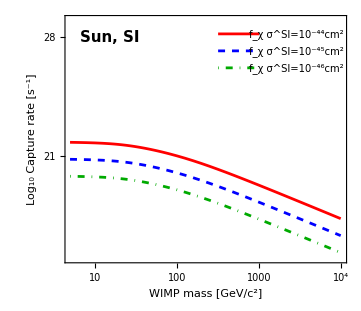

```mathematica
(* Capture rate plot *)
MyFrameSSI=Plot[-20,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4},{15,29}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-14,-14},{-13,-13},{-12,-12},{-11,-11},{-10,-10},{-9,-9},{-8,-8},{-7,-7},{-6,-6},{-5,-5},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-14,""},{-13,""},{-12,""},{-11,""},{-10,""},{-9,""},{-8,""},{-7,""},{-6,""},{-5,""},{-4,""},{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},
FrameLabel->{{ylabC,""},{"WIMP mass [GeV/c^2]",""}},AspectRatio->Full];

PlotC1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTable1[[i]]]},{i,1,NN}],PlotStyle->{Red,Thickness[thick]},PlotRange->All];
PlotC01=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTable01[[i]]]},{i,1,NN}],PlotStyle->{Blue,Dashed,Thickness[thick]},PlotRange->All];
PlotC001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTable001[[i]]]},{i,1,NN}],PlotStyle->{DG,DotDashed,Thickness[thick]},PlotRange->All];
LabelC1=Plot[28.2,{x,2.5,3},PlotStyle->{Red,Thickness[thick]}];
LabelC01=Plot[27.2,{x,2.5,3},PlotStyle->{Blue,Dashed,Thickness[thick]}];
LabelC001=Plot[26.2,{x,2.5,3},PlotStyle->{DG,DotDashed,Thickness[thick]}];

PlotCaptureSSI=Show[MyFrameSSI,PlotC1,PlotC01,PlotC001,Graphics[{EdgeForm[Thin],White,Rectangle[{2.4,25.5},{4.5,30}]}],LabelC1,LabelC01,LabelC001,Graphics[Text[Style["f_χ σ^SI=10^-44cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^28]}]],Graphics[Text[Style["f_χ σ^SI=10^-45cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^27]}]],Graphics[Text[Style["f_χ σ^SI=10^-46cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^26]}]],Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[15],28}]],Axes->False]
(*Export["PlotCapture_SI_Sun.png",PlotCaptureSSI,"png"]*)
```

## Spin Dependent capture rate in the Sun

```mathematica
(*Compute the capture rate*)
CTableSD1=Table[1,{i,1,NN}];
CTableSD01=Table[1,{i,1,NN}];
CTableSD001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTableSD1[[i]]=CSunSD[mTab[[i]],1,1];CTableSD01[[i]]=CSunSD[mTab[[i]],0.1,1];CTableSD001[[i]]=CSunSD[mTab[[i]],0.01,1]}]
```

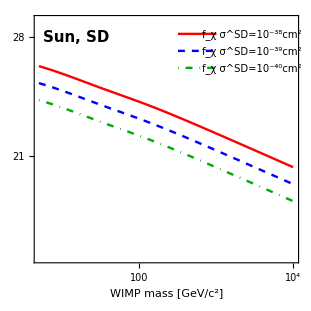

```mathematica
(* SD Capture rate plot *)
labelstyle={Bold,14};
MyFrameSSD=Plot[-20,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4},{15,29}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-14,-14},{-13,-13},{-12,-12},{-11,-11},{-10,-10},{-9,-9},{-8,-8},{-7,-7},{-6,-6},{-5,-5},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-14,""},{-13,""},{-12,""},{-11,""},{-10,""},{-9,""},{-8,""},{-7,""},{-6,""},{-5,""},{-4,""},{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}},FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{" WIMP mass [GeV/c^2]",None},AspectRatio->Full];

PlotCSD1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableSD1[[i]]]},{i,1,NN}],PlotStyle->{Red,Thickness[thick]}];
PlotCSD01=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableSD01[[i]]]},{i,1,NN}],PlotStyle->{Blue,Dashed,Thickness[thick]}];
PlotCSD001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableSD001[[i]]]},{i,1,NN}],PlotStyle->{DG,DotDashed,Thickness[thick]}];

PlotCaptureSSD=Show[MyFrameSSD,PlotCSD1,PlotCSD01,PlotCSD001,Graphics[{EdgeForm[Thin],White,Rectangle[{2.4,25.5},{4.5,30}]}],LabelC1,LabelC01,LabelC001,Graphics[Text[Style["f_χ σ^SD=10^-38cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^28]}]],Graphics[Text[Style["f_χ σ^SD=10^-39cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^27]}]],Graphics[Text[Style["f_χ σ^SD=10^-40cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.85 10^3],Log[10,1.5 10^26]}]],
Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[15],28}]],Axes->False]
(*Export["PlotCapture_SD_Sun.png",PlotCaptureSSD,"png"]*)
```

## Spin independent capture rate in the Earth

```mathematica
(*Compute the capture rate*)
CTableESI1=Table[1,{i,1,NN}];
CTableESI01=Table[1,{i,1,NN}];
CTableESI001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTableESI1[[i]]=CEarthSI[mTab[[i]],1,1];CTableESI01[[i]]=CEarthSI[mTab[[i]],0.1,1];CTableESI001[[i]]=CEarthSI[mTab[[i]],0.01,1]}];
```

```mathematica
(*CTableESIFe=Table[1,{i,1,NN}];
CTableESIO=Table[1,{i,1,NN}];
CTableESISi=Table[1,{i,1,NN}];
CTableESIMg=Table[1,{i,1,NN}];
CTableESINi=Table[1,{i,1,NN}];
CTableESICa=Table[1,{i,1,NN}];
CTableESIAl=Table[1,{i,1,NN}];
CTableESIS=Table[1,{i,1,NN}];
CTableESINa=Table[1,{i,1,NN}];
CTableESIP=Table[1,{i,1,NN}];
CTableESIMn=Table[1,{i,1,NN}];
CTableESIC=Table[1,{i,1,NN}];
CTableESIE=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTableESIFe[[i]]=CEarthSIElement[mTab[[i]],1,1,2],CTableESIO[[i]]=CEarthSIElement[mTab[[i]],1,1,5],CTableESISi[[i]]=CEarthSIElement[mTab[[i]],1,1,8],CTableESIMg[[i]]=CEarthSIElement[mTab[[i]],1,1,11],CTableESINi[[i]]=CEarthSIElement[mTab[[i]],1,1,14],CTableESICa[[i]]=CEarthSIElement[mTab[[i]],1,1,19],CTableESIAl[[i]]=CEarthSIElement[mTab[[i]],1,1,24],CTableESIS[[i]]=CEarthSIElement[mTab[[i]],1,1,25],CTableESINa[[i]]=CEarthSIElement[mTab[[i]],1,1,30],CTableESIP[[i]]=CEarthSIElement[mTab[[i]],1,1,31],CTableESIMn[[i]]=CEarthSIElement[mTab[[i]],1,1,32],CTableESIC[[i]]=CEarthSIElement[mTab[[i]],1,1,33],CTableESIE[[i]]=CEarthSIE[mTab[[i]],1,1]}];*)
```

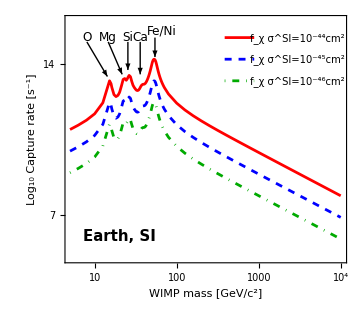

```mathematica
(* Capture rate plot *)
labelstyle={Bold,14};
MyFrameESI=Plot[-20,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4},{5,16}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-14,-14},{-13,-13},{-12,-12},{-11,-11},{-10,-10},{-9,-9},{-8,-8},{-7,-7},{-6,-6},{-5,-5},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-14,""},{-13,""},{-12,""},{-11,""},{-10,""},{-9,""},{-8,""},{-7,""},{-6,""},{-5,""},{-4,""},{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},
FrameLabel->{{ylabC,""},{"WIMP mass [GeV/c^2]",""}},AspectRatio->Full];

(*FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-14,-14},{-13,-13},{-12,-12},{-11,-11},{-10,-10},{-9,-9},{-8,-8},{-7,-7},{-6,-6},{-5,-5},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-14,""},{-13,""},{-12,""},{-11,""},{-10,""},{-9,""},{-8,""},{-7,""},{-6,""},{-5,""},{-4,""},{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}}*)
(*FrameLabel->{{"Log_10 Capture rate [s^-1]",""},{"WIMP mass [GeV/c^2]",""}}*)

PlotCESI1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESI1[[i]]]},{i,1,NN}],PlotStyle->{Red,Thickness[thick]}];
PlotCESI01=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESI01[[i]]]},{i,1,NN}],PlotStyle->{Blue,Dashed,Thickness[thick]}];
PlotCESI001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESI001[[i]]]},{i,1,NN}],PlotStyle->{DG,DotDashed,Thickness[thick]}];

PlotlE1=Plot[15.2,{x,2.58,2.94},PlotStyle->{Red,Thickness[thick]}];
PlotlE2=Plot[14.2,{x,2.58,2.94},PlotStyle->{Blue,Dashed,Thickness[thick]}];
PlotlE3=Plot[13.2,{x,2.58,2.94},PlotStyle->{DG,DotDashed,Thickness[thick]}];

PlotCaptureESI=Show[MyFrameESI,PlotCESI1,PlotCESI01,PlotCESI001,Graphics[{EdgeForm[Thin],White,Rectangle[{2.5,12.5},{4.5,30}]}],PlotlE1,PlotlE2,PlotlE3,Graphics[Text[Style["f_χ σ^SI=10^-44cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^15]}]],Graphics[Text[Style["f_χ σ^SI=10^-45cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^14]}]],Graphics[Text[Style["f_χ σ^SI=10^-46cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^13]}]],Graphics[{EdgeForm[Thin],White,Rectangle[{2.2,25.5},{4.5,30}]}],Graphics[{Text[Style["O",FontFamily->"Times",FontSize->12],{0.9,15.2}],Arrow[{{0.9,15},{1.15,13.4}}]}],Graphics[{Text[Style["Mg",FontFamily->"Times",FontSize->12],{1.16,15.2}],Arrow[{{1.16,15},{1.33,13.5}}]}],Graphics[{Text[Style["Si",FontFamily->"Times",FontSize->12],{1.4,15.2}],Arrow[{{1.4,15},{1.4,13.7}}]}],Graphics[{Text[Style["Ca",FontFamily->"Times",FontSize->12],{1.55,15.2}],Arrow[{{1.55,15},{1.55,13.5}}]}],Graphics[{Text[Style["Fe/Ni",FontFamily->"Times",FontSize->12],{1.81,15.5}],Arrow[{{1.73,15.2},{1.73,14.3}}]}],Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[20],6}]],Axes->False]
```

## Spin dependent capture rate in the Earth

```mathematica
(*Compute the capture rate*)
CTableESD1=Table[1,{i,1,NN}];
CTableESD01=Table[1,{i,1,NN}];
CTableESD001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTableESD1[[i]]=CEarthSD[mTab[[i]],1,1];CTableESD01[[i]]=CEarthSD[mTab[[i]],0.1,1];CTableESD001[[i]]=CEarthSD[mTab[[i]],0.01,1]}];
```

```mathematica
CTableESDDS=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,CTableESDDS[[i]]=CEarthSDDS[mTab[[i]],1,1]];
```

```mathematica
(*CTableESDFe=Table[1,{i,1,NN}];
CTableESDO=Table[1,{i,1,NN}];
CTableESDSi=Table[1,{i,1,NN}];
CTableESDMg=Table[1,{i,1,NN}];
CTableESDNi=Table[1,{i,1,NN}];
CTableESDCa=Table[1,{i,1,NN}];
CTableESDAl=Table[1,{i,1,NN}];
CTableESDCr=Table[1,{i,1,NN}];
CTableESDNa=Table[1,{i,1,NN}];
CTableESDP=Table[1,{i,1,NN}];
CTableESDMn=Table[1,{i,1,NN}];
CTableESDC=Table[1,{i,1,NN}];
CTableESDH=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{CTableESDFe[[i]]=CEarthSDElement[mTab[[i]],1,1,1];CTableESDO[[i]]=CEarthSDElement[mTab[[i]],1,1,2];CTableESDSi[[i]]=CEarthSDElement[mTab[[i]],1,1,3];CTableESDMg[[i]]=CEarthSDElement[mTab[[i]],1,1,4],CTableESDNi[[i]]=CEarthSDElement[mTab[[i]],1,1,5],CTableESDCa[[i]]=CEarthSDElement[mTab[[i]],1,1,6],CTableESDAl[[i]]=CEarthSDElement[mTab[[i]],1,1,7],CTableESDCr[[i]]=CEarthSDElement[mTab[[i]],1,1,8],CTableESDNa[[i]]=CEarthSDElement[mTab[[i]],1,1,9],CTableESDP[[i]]=CEarthSDElement[mTab[[i]],1,1,10],CTableESDMn[[i]]=CEarthSDElement[mTab[[i]],1,1,11],CTableESDC[[i]]=CEarthSDElement[mTab[[i]],1,1,12],CTableESDH[[i]]=CEarthSDElement[mTab[[i]],1,1,13]}];*)
```

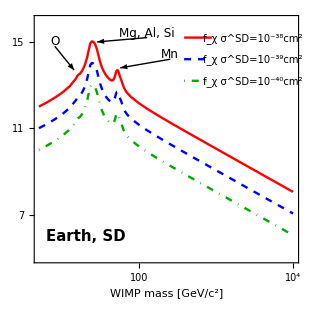

```mathematica
(* Capture rate plot *)
labelstyle={Bold,14};
MyFrameESD=Plot[-10,{x,10^-8,2.8},Frame->True,PlotRange->{{Log[10,5],4},{5,16}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}},FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{" WIMP mass [GeV/c^2]",None},AspectRatio->Full];

PlotCESD1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESD1[[i]]]},{i,1,NN}],PlotStyle->{Red,Thickness[thick]}];
PlotCESD01=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESD01[[i]]]},{i,1,NN}],PlotStyle->{Blue,Dashed,Thickness[thick]}];
PlotCESD001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESD001[[i]]]},{i,1,NN}],PlotStyle->{DG,DotDashed,Thickness[thick]}];
PlotlE1=Plot[15.2,{x,2.58,2.94},PlotStyle->{Red,Thickness[thick]}];
PlotlE2=Plot[14.2,{x,2.58,2.94},PlotStyle->{Blue,Dashed,Thickness[thick]}];
PlotlE3=Plot[13.2,{x,2.58,2.94},PlotStyle->{DG,DotDashed,Thickness[thick]}];

PlotCaptureESD=Show[MyFrameESD,PlotCESD1,PlotCESD01,PlotCESD001,Graphics[{EdgeForm[Thin],White,Rectangle[{2.5,12.5},{4.5,30}]}],PlotlE1,PlotlE2,PlotlE3,Graphics[Text[Style["f_χ σ^SD=10^-38cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^15]}]],Graphics[Text[Style["f_χ σ^SD=10^-39cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^14]}]],Graphics[Text[Style["f_χ σ^SD=10^-40cm^2",FontFamily->"Times",FontSize->10],{Log[10,2.95 10^3],Log[10,1.5 10^13]}]],Graphics[{Text[Style["O",FontFamily->"Times",FontSize->12],{0.9,15}],Arrow[{{0.9,14.8},{1.15,13.7}}]}],Graphics[{Text[Style["Mg, Al, Si",FontFamily->"Times",FontSize->12],{2.1,15.4}],Arrow[{{2.1,15.2},{1.45,15}}]}],Graphics[{Text[Style["Mn",FontFamily->"Times",FontSize->12],{2.4,14.4}],Arrow[{{2.4,14.2},{1.75,13.8}}]}],Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[20],6}]]]
```

```mathematica
CapturePlotSun=Row[{PlotCaptureSSI,PlotCaptureSSD},Frame->{False,All}]
Export["CapturePlotSun.pdf",CapturePlotSun,"pdf"]
```

-Graphics--Graphics-

CapturePlotSun.pdf

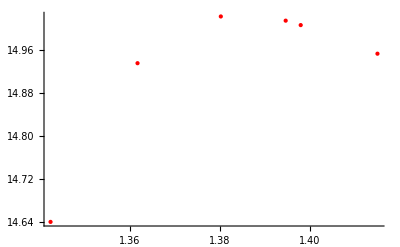

```mathematica
ListPlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESD1[[i]]]},{i,15,20}],PlotStyle->{Red,Thickness[thick]}]
```

```mathematica
CapturePlotEarth=Row[{PlotCaptureESI,PlotCaptureESD},Frame->{False,All}]
Export["CapturePlotEarth.pdf",CapturePlotEarth,"pdf"]
```

-Graphics--Graphics-

CapturePlotEarth.pdf

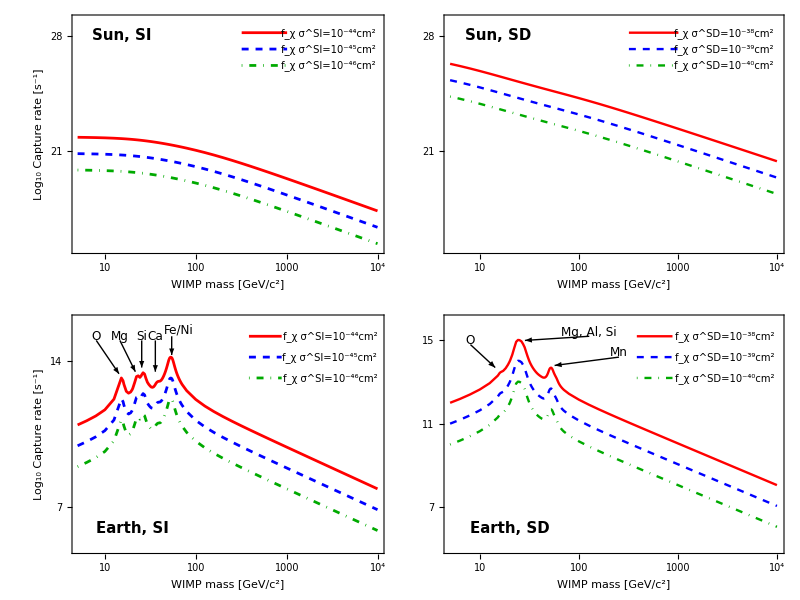

PlotCapture.pdf

```mathematica
CapturePlot=Grid[{{PlotCaptureSSI,PlotCaptureSSD},{PlotCaptureESI,PlotCaptureESD}},Frame->{False,All},Spacings->{0,.5}]
Export["PlotCapture.pdf",CapturePlot,"pdf"]
```

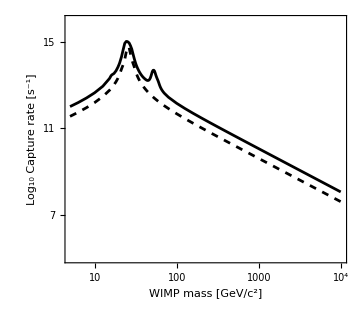

```mathematica
labelstyle={Bold,14};
MyFrameESDDS=Plot[-10,{x,10^-8,2.8},Frame->True,PlotRange->{{Log[10,5],4},{5,16}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,""},{11,""},{12,""},{13,""},{14,""},{15,""},{16,""},{17,""},{18,""},{19,""},{20,""},{21,""},{22,""},{23,""},{24,""},{25,""},{26,""},{27,""},{28,""},{29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},
FrameLabel->{{ylabC,""},{"WIMP mass [GeV/c^2]",""}},AspectRatio->Full];
PlotCESD=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESD1[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[thick]}];
PlotCESDDS=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,CTableESDDS[[i]]]},{i,1,NN}],PlotStyle->{Black,Dashed,Thickness[thick]}];
Show[MyFrameESDDS,PlotCESD,PlotCESDDS]
```

## Direct detection bounds, SI

```mathematica
lf=12;
```

```mathematica
(*Best LUX data from 1310.8214*)
LUX={{10000,2.0509200423284802 10^-44},{7909.827385974627,1.6237767391887442 10^-44},{5259.901322745289,1.0822433920725059 10^-44},{3700.224768617656,7.213126850614776 10^-45},{2495.448871537707,5.3984047895765343 10^-45},{1682.942377791068,3.395411760103083 10^-45},{1183.9129079342968,2.398074661276182 10^-45},{856.6239727617127,1.7947525400987933 10^-45},{561.6824249778103,1.0652706318278849 10^-45},{368.2912883138664,8.448380303483693 10^-46},{238.11243562293677,5.0145138244622756 10^-46},{151.79683940866238,3.342161714726789 10^-46},{102.37249769744422,2.650580271165979 10^-46},{70.01866873837952,1.6671242292151556 10^-46},{44.636948869478985,1.4846521582540252 10^-46},{28.058546715578945,1.667124229215155 10^-46},{19.738569824388446,2.650580271165979 10^-46},{12.063307409877854,1.0652706318278849 10^-45},{8.977529126389083,6.061898993497647 10^-45},{7.476994954377685,4.1046138970982103 10^-44},{6.681088898486456,2.0800692950144016 10^-43},{6.2272650704588095,1.054103596716002 10^-42},{6.054487586172747,3.772758783721487 10^-42},{5.804267963945424,2.2749895444311947 10^-41},{5.643226671245355,3.893937853818128 10^-40},{5.486653521318087,1.1229056044856463 10^-38},{5.410003623757898,7.603382956801555 10^-38},{5.310003623757898,7.603382956801555 10^-36}};
LUXPlot=ListLinePlot[Table[{Log[10,LUX[[i,1]]],Log[10,LUX[[i,2]]]},{i,1,Length[LUX]}],PlotRange->All,PlotStyle->{DB,Dashed,Thickness[0.005]}];
```

```mathematica
LUX2016SI = Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/DirectDetectionConstraints/Lux2016_SI.dat"];
CDMSLite2016SI=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/DirectDetectionConstraints/CDMSLite2016_SI.dat"];
CRESST2016SI=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/Mathematica/DirectDetectionConstraints/Cresst2016_SI.dat"];
LUX2016SIPlot=ListLinePlot[Table[{Log[10,LUX2016SI[[i,1]]],Log[10,LUX2016SI[[i,2]]]},{i,1,Length[LUX2016SI]}],PlotRange->All,PlotStyle->{DB,Thickness[0.005]}];
CRESST2016SIPlot=ListLinePlot[Table[{Log[10,CRESST2016SI[[i,1]]],Log[10,CRESST2016SI[[i,2]]]},{i,1,Length[CRESST2016SI]}],PlotRange->All,PlotStyle->{DB,Dashed,Thickness[0.005]}];
CDMSLite2016SIPlot=ListLinePlot[Table[{Log[10,CDMSLite2016SI[[i,1]]],Log[10,CDMSLite2016SI[[i,2]]]},{i,1,Length[CDMSLite2016SI]}],PlotRange->All,PlotStyle->{DB,Dashed,Thickness[0.005]}];
```

```mathematica
(*CDMS2 Ge 2009*)
CDMS={{8322.338933253635,1.9556197007925556 10^-42},{178.45706346363184,5.653189946945146 10^-44},{115.17273848124464,3.9894904627857157 10^-44},{70.24667408703127,3.9894904627857157 10^-44},{
50.759983516522986,5.991325789168044 10^-44},{35.15703731573158,1.274983566653138 10^-43},{23.01246760682718,7.284258025108387 10^-43}};
CDMSPlot=ListLinePlot[Table[{Log[10,CDMS[[i,1]]],Log[10,CDMS[[i,2]]]},{i,1,Length[CDMS]}],PlotStyle->{Red,Thickness[0.005]},PlotRange->All];
```

```mathematica
(*SuperCDMS2014 from 1402.7137*)
sCDMS={{3.649720139803372,8.007093566705995 10^-40},{3.7891883224692635,4.393970560760822 10^-40},{4.1269822784760954,1.478713949698179 10^-40},{4.5264788569990975,6.07832312829731 10^-41},{4.93144142097338,3.335539002014846 10^-41},{5.3540318480420455,1.7508270317357199 10^-41},{6.465022105482647,5.043159487171349 10^-42},{7.214598165501769,2.4219762725958416 10^-42},{7.996276968955154,1.2712972403326482 10^-42},{9.724826350402695,5.711586478126447 10^-43},{12.370375902915793,3.4256976894089663 10^-43},{15.575429551716837,2.4005396314866287 10^-43},{19.080553288961706,2.054666370572307 10^-43},{22.66302286512223,1.9653336650637646 10^-43},{27.104773915216654,1.9653336650637646 10^-43},{29.949809899520734,1.9653336650637646 10^-43}};
sCDMSPlot=ListLinePlot[Table[{Log[10,sCDMS[[i,1]]],Log[10,sCDMS[[i,2]]]},{i,1,Length[sCDMS]}],PlotStyle->{Red,Thickness[0.005]},PlotRange->All];
```

```mathematica
(*CDMSLite*)
CDMSLite={{1.44246591884 ,9.91500659938 10^-38},{1.48807744283,3.1138953832 10^-38},{1.57310917006,1.17189353987 10^-38},{1.67237029524,3.95653802105 10^-39},{1.78057263088,1.45936119043 10^-39},{1.90674409537,5.74049362195 10^-40},{2.06975043011,2.25801558091 10^-40},{2.26169212494,1.15350007776 10^-40},{2.48228908277,6.59485499723 10^-41},{2.75399352384,4.18593830288 10^-41},{3.08622587851,2.74375473938 10^-41},{3.58198060892,1.9647005757 10^-41},{4.2025703123,1.5808354225 10^-41},{4.8508774815,1.440875587 10^-41},{5.33029246607,1.40632981631 10^-41},{5.76546314597,1.28710902876 10^-41},{6.30754052897,1.11797654328 10^-41},{7.45805436177,8.13499840557 10^-42},{9.00352751177,6.36362256716 10^-42},{10.3476189886,5.54927704711 10^-42},{11.5744577063,5.07858719947 10^-42},{12.7181014694,4.83866003557 10^-42},{13.8955214807,4.76082623728 10^-42},{15.0312786953,4.81804578395 10^-42}};
CDMSLitePlot=ListLinePlot[Table[{Log[10,CDMSLite[[i,1]]],Log[10,CDMSLite[[i,2]]]},{i,1,Length[CDMSLite]}],PlotStyle->{DB,Dashed,Thickness[0.005]},PlotRange->All];
```

```mathematica
(*CRESST*)
CRESST={{1.2597808004600963,8.154875270087116 10^-38},{1.3032995574462207,4.998260622459671 10^-38},{1.3854565823796385,2.3025269621793454 10^-38},{1.534054213876622,8.304076446274118 10^-39},{1.6530617828593748,5.0897085403077376 10^-39},{1.9457433092073053,1.9916480638308707 10^-39},{2.154434690031884,1.2207146966133233 10^-39},{2.535886393793826,6.620124267486042 10^-40},{2.846277804429182,4.402514422750886 10^-40},{3.5614136497581894,2.486962812591004 10^-40},{3.8901872083118083,2.028087153802468 10^-40},{4.2493116509339925,1.587769304023469 10^-40},{4.673223147406958,1.0136908159767351 10^-40},{5.00167011255914,6.471778159406801 10^-41},{5.389685474444668,3.9666620101612553 10^-41},{5.690654802047439,2.8621534453892906 10^-41},{6.258354747641396,1.827304920277265 10^-41},{6.836097678798157,1.2151941476076345 10^-41},{7.884155153546923,7.758250168566858 10^-42},{8.909483079436773,5.831066998996835 10^-42},{10.275415922455043,4.3826045316956895 10^-42},{12.012848989431937,3.57395933140969 10^-42},{13.667630061472448,2.6861722502291397 10^-42},{15.133556515712828,1.9382133242529564 10^-42},{16.530617828593748,1.4567526834669086 10^-42},{19.59004340421583,8.571777040668072 10^-43},{24.679160560811056,4.648607029950468 10^-43},{29.44601633495884,3.091416213374161 10^-43},{37.09552602881553,1.894781148109043 10^-43},{52.09717322799161,1.1149209970081005 10^-43},{61.32119639330014,9.864940909388522 10^-44},{76.20893626135357,9.470610000772354 10^-44},{100.0000000000001,1.0703543023037402 10^-43}};
CRESSTint=Interpolation[Table[{CRESST[[i,1]],CRESST[[i,2]]},{i,1,Length[CRESST]}]];

CRESSTPlot=ListLinePlot[Table[{Log[10,CRESST[[i,1]]],Log[10,CRESST[[i,2]]]},{i,1,Length[CRESST]}],PlotStyle->{DB,Dashed,Thickness[0.005]},PlotRange->All];
```

```mathematica
(*Neutrino floor from Strigari*)
NuFloor={{8852.11083904734,1.640978816780426 10^-47},{6495.719925251636,1.3014170014556133 10^-47},{4902.61397189492,9.739986443321232 10^-48},{3448.8809840083595,6.879052186057414 10^-48},{2358.895802767997,4.85846250956033 10^-48},{1590.850350231973,2.8837275956642175 10^-48},{1014.1681785985471,1.921997685780353 10^-48},{619.8130164746741,1.2088707311815587 10^-48},{363.146168540605,9.047357242349496 10^-49},{221.9382612215351,5.37003500515994 10^-49},{141.48579224409886,3.3775681371450596 10^-49},{99.53213962498107,2.8385022633124287 10^-49},{69.0404907351131,1.6847855244251481 10^-49},{49.25659179403833,1.0596724043239502 10^-49},{30.529876741124575,8.403982238273251 10^-50},{21.17705577546665,7.484139543610833 10^-50},{14.897592463936409,1.2609169965852953 10^-49},{12.407559153197663,2.678660170567887 10^-49},{11.086807764556323,8.537881335243249 10^-49},{10.931922336467812,2.7213387683753756 10^-48},{10.480128284813217,1.4613684447074126 10^-47},{9.497225312519632,6.988654854126813 10^-47},{8.728444675990366,7.10000380126522 10^-46},{7.167986004197866,1.7947525400987933 10^-45},{5.113963658641654,3.812726894956225 10^-45},{3.3063457678330948,3.0237730994836134 10^-45},{2.3259414489100756,2.5411735420628328 10^-45},{1.5037976761598806,3.204208910459779 10^-45},{0.9320733738282607,9.637883965929923 10^-45},{0.6198130164746741,2.735715545083376 10^-44},{0.43602481011453703,4.884129667010867 10^-44},{0.33375024147590915,5.175577427271256 10^-44}};
NuFloorPlot=ListLinePlot[Table[{Log[10,NuFloor[[i,1]]],Log[10,NuFloor[[i,2]]]},{i,1,32}],PlotStyle->{Red,Dashed,Thickness[0.005]},PlotRange->All];
LUXLabel=Inset[Graphics[Rotate[Text[Style["LUX 2015",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-44.4}];
CDMSLabel=Inset[Graphics[Rotate[Text[Style["CDMSlite",FontFamily->"Times",FontSize->lf],{1,1}],-π/12]],{1.05,-40.9}];
LUXLabel001=Inset[Graphics[Rotate[Text[Style["LUX 2015",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-42.4}];
CDMSLabel001=Inset[Graphics[Rotate[Text[Style["CDMSlite",FontFamily->"Times",FontSize->lf],{1,1}],-π/12]],{1.05,-38.9}];
CDMSLabel001A=Inset[Graphics[{Text[Style["CDMSlite",FontFamily->"Times",FontSize->8],{1,1}],Arrow[{{1.05,-38},{1,-37}}]}],{1.05,-38.8}];
NuFloorLabel=Inset[Graphics[Rotate[Text[Style["Neutrino Floor",FontFamily->"Times",FontSize->lf],{1,1}],π/14]],{3,-47.3}];
(*LUXLabelm4=Inset[Graphics[Rotate[Text[Style["LUX 2015",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-40.4}];
CDMSLabelm4=Inset[Graphics[Rotate[Text[Style["CDMSlite",FontFamily->"Times",FontSize->lf],{1,1}],-π/12]],{1,-36.7}];*)
```

## Direct detection bounds, SD

```mathematica
(*LUX SD*)
LUXSD={{2.5,1.4683785599005913*^-29},{3.2645851589,1.33384520173 10^-34},{3.3079335281,5.76966601089 10^-35},{3.39264362873,1.45616201919 10^-35},{3.74524496635,1.7379907025 10^-36},{4.46595258742,1.49141482013 10^-37},{5.3692128002,2.16048650019 10^-38},{6.4449093996,4.83013246882 10^-39},{8.0952922328,1.12893515403 10^-39},{9.73758380174,5.66200325081 10^-40},{12.2582086058,2.8812228374 10^-40},{14.5821464611,1.89187526113 10^-40},{19.9939860825,1.13401221198 10^-40},{24.7427753094,9.74391932485 10^-41},{32.0375534954,9.0188040677 10^-41},{43.1827703093,9.12816326603 10^-41},{58.1637243019,1.12227011201 10^-40},{79.9395378367,1.40030980024 10^-40},{114.401126409,1.77287411618 10^-40},{179.234984481,2.60453572774 10^-40},{286.491388459,4.06154017485 10^-40},{370.529359975,5.14722309571 10^-40},{532.778084234,7.1284630333 10^-40},{886.638888074,1.1621982838 10^-39},{1591.28798272,2.1024815615 10^-39},{3064.96771942,4.03531965028 10^-39},{5473.65775303,7.08523856261 10^-39},{9627.46453933,1.26297196472 10^-38},{14410.3946932,1.91265127589 10^-38},{31807.4717178,4.07091559861 10^-38},{52918.8691051,7.15267613582 10^-38},{75711.212832,9.75920559164 10^-38}};
LUXSDPlot=ListLinePlot[Table[{Log[10,LUXSD[[i,1]]],Log[10,LUXSD[[i,2]]]},{i,1,Length[LUXSD]}],PlotStyle->{DB,Dashed,Thickness[0.005]},PlotRange->All];
```

```mathematica
(*LUX2016SD=Import["/Users/luca.visinelli/Dropbox/LucaVisinelliArticoli/Dark matter capture/Mathematica/DirectDetectionConstraints/Lux2016_SD.dat"];*)
PICO2016SD60=Import["/Users/luca.visinelli/Dropbox/LucaVisinelliArticoli/Dark matter capture/Mathematica/DirectDetectionConstraints/PICO2016_Fig3_PICO-60_SD.dat"];
PICO2016SD60 = Join[PICO2016SD60,{{10^4,3.3*^-38}}];
PICO2016SD2L=Import["/Users/luca.visinelli/Dropbox/LucaVisinelliArticoli/Dark matter capture/Mathematica/DirectDetectionConstraints/PICO2016_Fig3_PICO-2L_SD.dat"];
(*LUX2016SDPlot=ListLinePlot[Table[{Log[10,LUX2016SD[[i,1]]],Log[10,LUX2016SD[[i,2]]]},{i,1,Length[LUX2016SD]}],PlotRange->All,PlotStyle->{DB,Thickness[0.005]}];*)
PICO2016SD2L = Join[PICO2016SD2L,{{10^4,5.5*^-38}}];
PICO2016SD60Plot=ListLinePlot[Table[{Log[10,PICO2016SD60[[i,1]]],Log[10,PICO2016SD60[[i,2]]]},{i,1,Length[PICO2016SD60]}],PlotRange->All,PlotStyle->{DB,Dashed,Thickness[0.005]}];
PICO2016SD2LPlot=ListLinePlot[Table[{Log[10,PICO2016SD2L[[i,1]]],Log[10,PICO2016SD2L[[i,2]]]},{i,1,Length[PICO2016SD2L]}],PlotRange->All,PlotStyle->{DB,Dashed,Thickness[0.005]}];
PICOLabel=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-38}];
PICOLabel001=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-36}];
PICOLabelbb=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-39}];
PICOLabelbb001=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-37}];
(*PICOLabelm4=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-34}];
PICOLabelm4b=Inset[Graphics[Rotate[Text[Style["PICO2016",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-35}];*)
```

Import::nffil: File not found during Import.

Part::partd: Part specification Join[$Failed, {{10000, 3.3`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification Join[$Failed, {{10000, 3.3`*^-38}}] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partw: Part 2 of {{10000, 3.3`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000.`, 3.3`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 2 of {{10000.`, 3.3`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000, 5.5`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification Join[$Failed, {{10000, 5.5`*^-38}}] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partw: Part 2 of {{10000, 5.5`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000.`, 5.5`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 2 of {{10000.`, 5.5`*^-38}} does not exist.

```mathematica
(*Frames*)
x1=300;
y1=250;
pxr1=10;
pxl1=5;
pyu1=6;
pyd1=5;
pxax1=50;
pyax1=50;
ipyf=10;
thick=0.0055;
labelstyle={Bold,14};

SunSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1,pyu1}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
EarthSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1},ImagePadding->{{pxl1,pxr1},{pyd1,pyu1}},AspectRatio->Full];
SunSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30},{-29,-29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
EarthSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
```

## Spin Independent cross section vs. mass, Sun

```mathematica
(*Compute the σ-Subscript[m, χ] plot*)
(*ss is inputed in units of σSI*)
sTableSSI= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSI[mTab[[i]],ss,1]==1,{ss,0.1,10}];sTableSSI[[i]]=10^4 σSI ss/.sA}];(*I multiplied the result by σSI (m^2) and by an additional 10^4 cm^2/m^2 so that ss is expressed in cm^-2*)

(*sTable01= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSI[mTab[[i]],ss,0.1]==1,{ss,0.1,10}];sTable01[[i]]=10^4 σSI ss/.sA}];*)
(*sTable001= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSI[mTab[[i]],ss,0.01]==1,{ss,0.1,10}];sTable001[[i]]=10^4 σSI ss/.sA}];*)
```

```mathematica
sTableSSI1= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSI[mTab[[i]],ss,0.01]==1,{ss,0.1,10}];sTableSSI1[[i]]=10^4 σSI ss/.sA}];
```

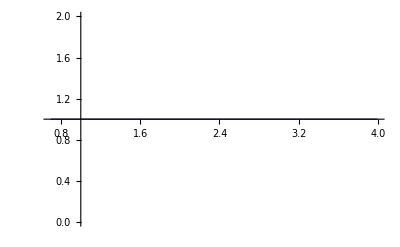

```mathematica
ListLinePlot[Table[{Log10[mTab[[i]]],sTableSSI[[i]]/sTableSSI1[[i]]},{i,1,NN}],PlotRange->All]
```

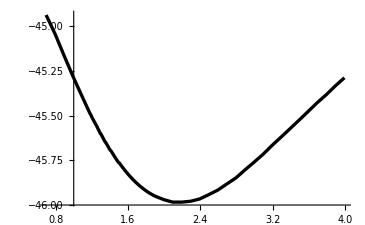

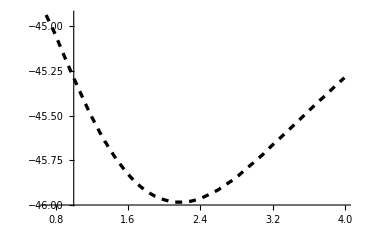

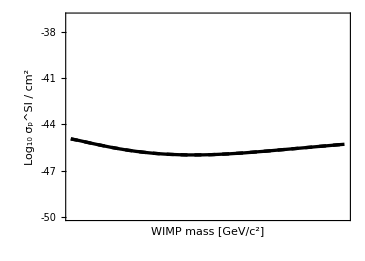

```mathematica
ppp=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All]
qqq=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSI1[[i]]]},{i,1,NN}],PlotStyle->{Black,Dashed,Thickness[0.0065]},PlotRange->All]
Show[SunSIFrame,ppp,qqq]
```

```mathematica
3/7.
```

0.428571

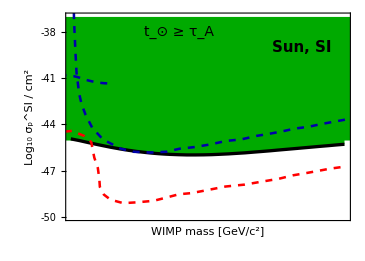

```mathematica
(* Cross section vs mass at τA = τSun *)
PlotSunSIσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All,Filling->Top,FillingStyle->Darker[Green]];
Filling1=Plot[{Log[10,sTableSSI[[1]]],-37.1},{mm,-3,5},PlotStyle->{{Darker[Green],Thickness[0.0065]},{Darker[Green],Thickness[0.0065]}},Filling->{1->{2}},FillingStyle->Darker[Green],PlotRange->All];

PlotSunSI=Show[SunSIFrame,Filling1,PlotSunSIσ,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,
Graphics[Text[Style["t_⊙ ≥ τ_A",FontFamily->"Times",FontSize->14],{2,-38}]],Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[3000],-39}]],
Epilog->{CDMSLabel,LUXLabel,NuFloorLabel},Axes->False]
```

## Spin Independent cross section vs. mass, Earth

```mathematica
(*Compute the σ-Subscript[m, χ] plot*)
(*ss is inputed in units of σSI*)
sTableESI= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τAEarthSI[mTab[[i]],ss,1]==1,{ss,0.1,10}];sTableESI[[i]]=10^4 σSI ss/.sA}];(*I multiplied the result by σSI (m^2) and by an additional 10^4 cm^2/m^2 so that ss is expressed in cm^-2*)
```

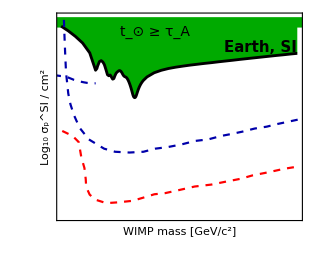

```mathematica
(* Cross section vs mass at τA = τSun *)
PlotEarthSIσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All,Filling->Top,FillingStyle->Darker[Green]];
Filling1=Plot[{Log[10,sTableESI[[1]]],-37.1},{mm,-3,5},PlotStyle->{{Darker[Green],Thickness[0.0065]},{Darker[Green],Thickness[0.0065]}},Filling->{1->{2}},FillingStyle->Darker[Green],PlotRange->All];

PlotEarthSI=Show[EarthSIFrame,Filling1,PlotEarthSIσ,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,
Graphics[Text[Style["t_⊙ ≥ τ_A",FontFamily->"Times",FontSize->14],{2,-38}]],Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[3000],-39}]],
Epilog->{CDMSLabel,LUXLabel,NuFloorLabel},Axes->False]
```

## Spin Dependent cross section vs. mass, Sun

```mathematica
(*Compute the σ-Subscript[m, χ] plot*)
(*ss is inputed in units of σSI*)
sTableSSD= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSD[mTab[[i]],ss,1]==1,{ss,0.1}];sTableSSD[[i]]=10^4 σSD ss/.sA}];(*I multiplied the result by σSD (m^2) and by an additional 10^4 cm^2/m^2 so that ss is expressed in cm^-2*)

(*sTableSD01= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSD01[mTab[[i]],ss]==1,{ss,0.1}];sTableSD01[[i]]=10^4 σSD ss/.sA}];*)
(*sTableSD001= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSD001[mTab[[i]],ss]==1,{ss,0.1}];sTableSD001[[i]]=10^4 σSD ss/.sA}];*)
```

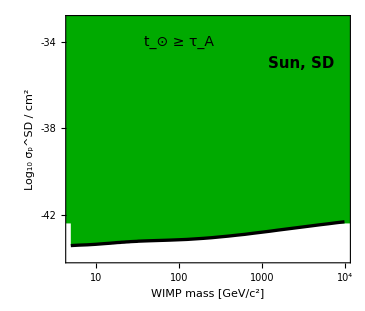

```mathematica
(* Cross section vs mass at τA = τSun *)

PlotSunSDσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},Filling->Top,FillingStyle->Darker[Green],PlotRange->All];
Filling1=Plot[{Log[10,sTableSSD[[NN]]],-29},{mm,-3,5},PlotStyle->{{Darker[Green],Thickness[0.0065]},{Darker[Green],Thickness[0.0065]}},Filling->{1->{2}},FillingStyle->Darker[Green],PlotRange->All];

PlotSunSD=Show[SunSDFrame,Filling1,PlotSunSDσ,PICO2016SD60Plot,PICO2016SD2LPlot,
Graphics[Text[Style["t_⊙ ≥ τ_A",FontFamily->"Times",FontSize->14],{2,-34}]],Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[3000],-35}]],
Epilog->{PICOLabel},Axes->False]
```

## Spin Dependent cross section vs. mass, Earth

```mathematica
(*Compute the σ-Subscript[m, χ] plot*)
(*ss is inputed in units of σSI*)
sTableESD= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τAEarthSD[mTab[[i]],ss,1]==1,{ss,0.1}];sTableESD[[i]]=10^4 σSD ss/.sA}];(*I multiplied the result by σSD (m^2) and by an additional 10^4 cm^2/m^2 so that ss is expressed in cm^-2*)

(*sTableSD01= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSD01[mTab[[i]],ss]==1,{ss,0.1}];sTableSD01[[i]]=10^4 σSD ss/.sA}];*)
(*sTableSD001= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τASunSD001[mTab[[i]],ss]==1,{ss,0.1}];sTableSD001[[i]]=10^4 σSD ss/.sA}];*)
```

```mathematica
sTableESDDS= Table[i,{i,1,NN}];
For[i=1,i≤NN,i++,{sA=FindRoot[τAEarthSDDS[mTab[[i]],ss,1]==1,{ss,0.1}];sTableESDDS[[i]]=10^4 σSD ss/.sA}];
PlotEarthSDDSσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESDDS[[i]]]},{i,1,NN}],PlotStyle->{Black,Dashed,Thickness[0.0065]},PlotRange->All];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

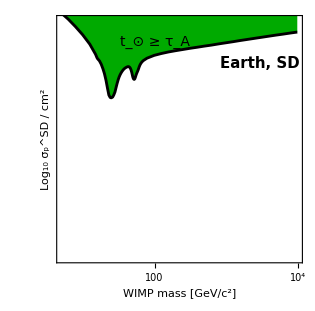

```mathematica
(* Cross section vs mass at τA = τSun *)
PlotEarthSDσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},Filling->Top,FillingStyle->Darker[Green],PlotRange->All];
Filling1=Plot[{Log[10,sTableESD[[1]]],-29},{mm,-3,5},PlotStyle->{{Darker[Green],Thickness[0.0065]},{Darker[Green],Thickness[0.0065]}},Filling->{1->{2}},FillingStyle->Darker[Green],PlotRange->All];

PlotEarthSD=Show[EarthSDFrame,Filling1,PlotEarthSDσ,PICO2016SD60Plot,PICO2016SD2LPlot,
Graphics[Text[Style["t_⊙ ≥ τ_A",FontFamily->"Times",FontSize->14],{2,-34}]],Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[3000],-35}]],Epilog->{PICOLabel},Axes->False]
```

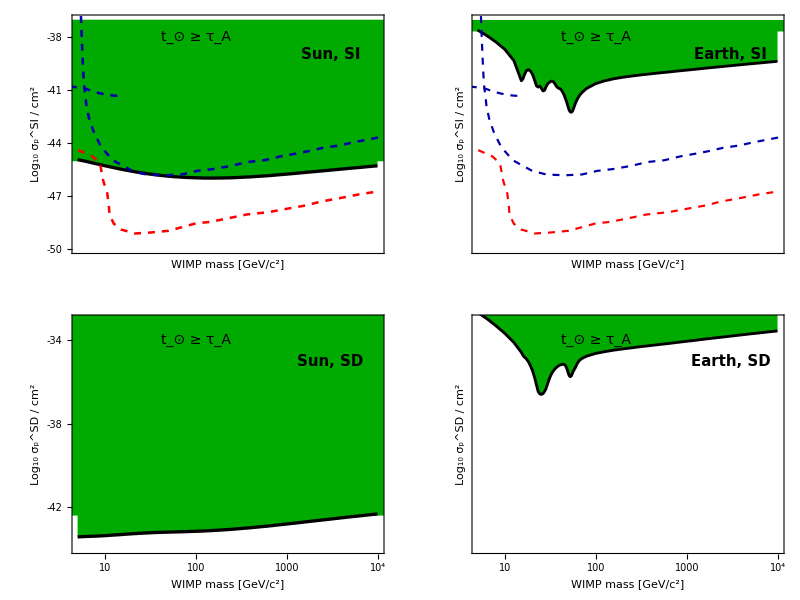

EquilibriumPlot.pdf

```mathematica
EquilibriumPlot=Grid[{{PlotSunSI,PlotEarthSI},{PlotSunSD,PlotEarthSD}},Frame->{False,All},Spacings->{0,.5}]
Export["EquilibriumPlot.pdf",EquilibriumPlot,"pdf"]
```

## Annihilation rate Sun SI, as a function of σ and mass, f_CDM= 1 & f_CDM=0.01

```mathematica
fcdm1=1;
fcdm001=0.01;
fcdmm4=10^-4;
```

```mathematica
(* Annihilation rate Γ = C tanh^2(t/τ) *)
ΓSunSI[mm_,ss_,fcdm_]:=0.5 CSunSI[mm,ss,fcdm] (Tanh[1/τASunSI[mm,ss,fcdm]])^2;
ΓSunSD[mm_,ss_,fcdm_]:=0.5CSunSD[mm,ss,fcdm] (Tanh[1/τASunSD[mm,ss,fcdm]])^2;
ΓEarthSI[mm_,ss_,fcdm_]:=0.5CEarthSI[mm,ss,fcdm] (Tanh[1/τAEarthSI[mm,ss,fcdm]])^2;
ΓEarthSD[mm_,ss_,fcdm_]:=0.5CEarthSD[mm,ss,fcdm] (Tanh[1/τAEarthSD[mm,ss,fcdm]])^2;
ΓEarthSDDS[mm_,ss_,fcdm_]:=0.5CEarthSDDS[mm,ss,fcdm] (Tanh[1/τAEarthSDDS[mm,ss,fcdm]])^2;
```

```mathematica
σSITab=10^-6 10^Range[0,14.5,0.75];
σSDTab=10^-6 10^Range[0,11,0.5];
NSI=Length[σSITab];
NSD=Length[σSDTab];
```

```mathematica
(*Subscript[f, χ]=100%*)
```

```mathematica
GammaEarthSI1= Table[ΓEarthSI[mTab[[i]],σSITab[[j]],1],{j,1,NSI},{i,1,NN}];
```

```mathematica
GammaEarthSD1= Table[ΓEarthSD[mTab[[i]],σSDTab[[j]],1],{j,1,NSD},{i,1,NN}];
```

```mathematica
GammaSunSI1= Table[ΓSunSI[mTab[[i]],σSITab[[j]],1],{j,1,NSI},{i,1,NN}];
```

```mathematica
GammaSunSD1= Table[ΓSunSD[mTab[[i]],σSDTab[[j]],1],{j,1,NSD},{i,1,NN}];
```

```mathematica
(*Subscript[f, χ]=1%*)
```

```mathematica
GammaEarthSI001= Table[ΓEarthSI[mTab[[i]],σSITab[[j]],fcdm001],{j,1,NSI},{i,1,NN}];
```

```mathematica
GammaEarthSD001= Table[ΓEarthSD[mTab[[i]],σSDTab[[j]],fcdm001],{j,1,NSD},{i,1,NN}];
```

```mathematica
GammaSunSI001= Table[ΓSunSI[mTab[[i]],σSITab[[j]],fcdm001],{j,1,NSI},{i,1,NN}];
```

```mathematica
GammaSunSD001= Table[ΓSunSD[mTab[[i]],σSDTab[[j]],fcdm001],{j,1,NSD},{i,1,NN}];
```

```mathematica
(*Subscript[f, χ]=0.01%*)
```

```mathematica
(*GammaSunSIm4= Table[ΓSunSI[mTab[[i]],σSITab[[j]],fcdmm4],{j,1,NSI},{i,1,NN}];
GammaSunSDm4= Table[ΓSunSD[mTab[[i]],σSDTab[[j]],fcdmm4],{j,1,NSD},{i,1,NN}];
GammaEarthSIm4= Table[ΓEarthSI[mTab[[i]],σSITab[[j]],fcdmm4],{j,1,NSI},{i,1,NN}];
GammaEarthSDm4= Table[ΓEarthSD[mTab[[i]],σSDTab[[j]],fcdmm4],{j,1,NSD},{i,1,NN}];*)
```

```mathematica
AnnRateSunSI=Log10[GammaSunSI1];
AnnRateEarthSI=Log10[GammaEarthSI1];
AnnRateSunSD=Log10[GammaSunSD1];
AnnRateEarthSD=Log10[GammaEarthSD1];
```

```mathematica
AnnRateSunSI001=Log10[GammaSunSI001];
AnnRateEarthSI001=Log10[GammaEarthSI001];
AnnRateSunSD001=Log10[GammaSunSD001];
AnnRateEarthSD001=Log10[GammaEarthSD001];
```

```mathematica
maxplot=
Max[AnnRateSunSI, AnnRateEarthSI, AnnRateSunSD, AnnRateEarthSD,AnnRateSunSI001, AnnRateEarthSI001, AnnRateSunSD001, AnnRateEarthSD001];
minplot=Min[AnnRateSunSI, AnnRateEarthSI, AnnRateSunSD, AnnRateEarthSD,AnnRateSunSI001, AnnRateEarthSI001, AnnRateSunSD001, AnnRateEarthSD001];
range=maxplot-minplot;
```

```mathematica
AnnRateSunSI=(AnnRateSunSI-minplot)/range;
AnnRateEarthSI=(AnnRateEarthSI-minplot)/range;
AnnRateSunSD=(AnnRateSunSD-minplot)/range;
AnnRateEarthSD=(AnnRateEarthSD-minplot)/range;
AnnRateSunSI001=(AnnRateSunSI001-minplot)/range;
AnnRateEarthSI001=(AnnRateEarthSI001-minplot)/range;
AnnRateSunSD001=(AnnRateSunSD001-minplot)/range;
AnnRateEarthSD001=(AnnRateEarthSD001-minplot)/range;
```

```mathematica
(*Isopycnal curves, Sun SI*)
σTabSSI08f1=Table[1,{i,1,NN}];
σTabSSI10f1=Table[1,{i,1,NN}];
σTabSSI12f1=Table[1,{i,1,NN}];
σTabSSI14f1=Table[1,{i,1,NN}];
σTabSSI16f1=Table[1,{i,1,NN}];
σTabSSI18f1=Table[1,{i,1,NN}];
σTabSSI20f1=Table[1,{i,1,NN}];
σTabSSI22f1=Table[1,{i,1,NN}];
σTabSSI24f1=Table[1,{i,1,NN}];
σTabSSI26f1=Table[1,{i,1,NN}];
σTabSSI28f1=Table[1,{i,1,NN}];
σTabSSI30f1=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^8==1,{ss,1,10}];σTabSSI08f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^10==1,{ss,1,10}];σTabSSI10f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^12==1,{ss,1,10}];σTabSSI12f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^14==1,{ss,1,10}];σTabSSI14f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^16==1,{ss,1,10}];σTabSSI16f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^18==1,{ss,1,10}];σTabSSI18f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^20==1,{ss,1,10}];σTabSSI20f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^22==1,{ss,1,10}];σTabSSI22f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^24==1,{ss,1,10}];σTabSSI24f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^26==1,{ss,1,10}];σTabSSI26f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^28==1,{ss,1,10}];σTabSSI28f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,1]/10^30==1,{ss,1,10}];σTabSSI30f1[[i]]=10^4 σSI ss/.sol}];
```

```mathematica
PlotSSI08f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI08f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI10f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI10f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI12f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI12f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI14f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI14f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI16f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI16f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI18f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI18f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI20f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI20f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI22f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI22f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI24f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI24f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI26f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI26f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI28f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI28f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI30f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI30f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
```

```mathematica
(*Isopycnal curves, Earth SI*)
σTabESIm8f1=Table[1,{i,1,NN}];
σTabESIm6f1=Table[1,{i,1,NN}];
σTabESIm4f1=Table[1,{i,1,NN}];
σTabESIm2f1=Table[1,{i,1,NN}];
σTabESI00f1=Table[1,{i,1,NN}];
σTabESI02f1=Table[1,{i,1,NN}];
σTabESI04f1=Table[1,{i,1,NN}];
σTabESI06f1=Table[1,{i,1,NN}];
σTabESI08f1=Table[1,{i,1,NN}];
σTabESI10f1=Table[1,{i,1,NN}];
σTabESI12f1=Table[1,{i,1,NN}];
σTabESI14f1=Table[1,{i,1,NN}];
σTabESI16f1=Table[1,{i,1,NN}];
σTabESI18f1=Table[1,{i,1,NN}];
σTabESI20f1=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^-8==1,{ss,1,10}];σTabESIm8f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^-6==1,{ss,1,10}];σTabESIm6f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^-4==1,{ss,1,10}];σTabESIm4f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^-2==1,{ss,1,10}];σTabESIm2f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^0==1,{ss,1,10}];σTabESI00f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^2==1,{ss,1,10}];σTabESI02f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^4==1,{ss,1,10}];σTabESI04f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^6==1,{ss,1,10}];σTabESI06f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^8==1,{ss,1,10}];σTabESI08f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^10==1,{ss,1,10}];σTabESI10f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^12==1,{ss,1,10}];σTabESI12f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^14==1,{ss,1,10}];σTabESI14f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^16==1,{ss,1,10}];σTabESI16f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^18==1,{ss,1,10}];σTabESI18f1[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,1]/10^20==1,{ss,1,10}];σTabESI20f1[[i]]=10^4 σSI ss/.sol}];
```

```mathematica
PlotESIm8f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm8f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm6f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm6f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm4f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm4f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm2f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm2f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI00f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI00f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI02f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI02f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI04f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI04f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI06f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI06f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI08f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI08f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI10f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI10f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI12f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI12f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI14f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI14f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI16f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI16f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI18f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI18f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];PlotESI20f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI20f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
(*Isopycnal curves, Sun SD*)
σTabSSD14f1=Table[1,{i,1,NN}];
σTabSSD16f1=Table[1,{i,1,NN}];
σTabSSD18f1=Table[1,{i,1,NN}];
σTabSSD20f1=Table[1,{i,1,NN}];
σTabSSD22f1=Table[1,{i,1,NN}];
σTabSSD24f1=Table[1,{i,1,NN}];
σTabSSD26f1=Table[1,{i,1,NN}];
σTabSSD28f1=Table[1,{i,1,NN}];
σTabSSD30f1=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^14==1,{ss,1,10}];σTabSSD14f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^16==1,{ss,1,10}];σTabSSD16f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^18==1,{ss,1,10}];σTabSSD18f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^20==1,{ss,1,10}];σTabSSD20f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^22==1,{ss,1,10}];σTabSSD22f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^24==1,{ss,1,10}];σTabSSD24f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^26==1,{ss,1,10}];σTabSSD26f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^28==1,{ss,1,10}];σTabSSD28f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,1]/10^30==1,{ss,1,10}];σTabSSD30f1[[i]]=10^4 σSD ss/.sol}];
```

```mathematica
PlotSSD14f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD14f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD16f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD16f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD18f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD18f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD20f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD20f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD22f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD22f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD24f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD24f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD26f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD26f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD28f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD28f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD30f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD30f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
(*Isopycnal curves, Earth SD*)
σTabESDm6f1=Table[1,{i,1,NN}];
σTabESDm4f1=Table[1,{i,1,NN}];
σTabESDm2f1=Table[1,{i,1,NN}];
σTabESD00f1=Table[1,{i,1,NN}];
σTabESD02f1=Table[1,{i,1,NN}];
σTabESD04f1=Table[1,{i,1,NN}];
σTabESD06f1=Table[1,{i,1,NN}];
σTabESD08f1=Table[1,{i,1,NN}];
σTabESD10f1=Table[1,{i,1,NN}];
σTabESD12f1=Table[1,{i,1,NN}];
σTabESD14f1=Table[1,{i,1,NN}];
σTabESD16f1=Table[1,{i,1,NN}];
σTabESD18f1=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^-6==1,{ss,1,10}];σTabESDm6f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^-4==1,{ss,1,10}];σTabESDm4f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^-2==1,{ss,1,10}];σTabESDm2f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^0==1,{ss,1,10}];σTabESD00f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^2==1,{ss,1,10}];σTabESD02f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^4==1,{ss,1,10}];σTabESD04f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^6==1,{ss,1,10}];σTabESD06f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^8==1,{ss,1,10}];σTabESD08f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^10==1,{ss,1,10}];σTabESD10f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^12==1,{ss,1,10}];σTabESD12f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^14==1,{ss,1,10}];σTabESD14f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^16==1,{ss,1,10}];σTabESD16f1[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,1]/10^18==1,{ss,1,10}];σTabESD18f1[[i]]=10^4 σSD ss/.sol}];
```

```mathematica
PlotESDm6f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm6f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESDm4f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm4f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESDm2f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm2f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD00f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD00f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD02f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD02f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD04f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD04f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD06f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD06f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD08f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD08f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD10f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD10f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD12f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD12f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD14f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD14f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD16f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD16f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD18f1=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD18f1[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
(*Fermi bounds*)
TTFermi=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/FermiBounds/ttfermi.dat"];
TTFermiLog = {TTFermi[[Range[Length[TTFermi]],1]],TTFermi[[Range[Length[TTFermi]],2]]}//Transpose;
TTFermi2=Interpolation[TTFermiLog,InterpolationOrder->1];

BBFermi=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/FermiBounds/bbfermi.dat"];
BBFermiLog = {BBFermi[[Range[Length[BBFermi]],1]],BBFermi[[Range[Length[BBFermi]],2]]}//Transpose;
BBFermi2=Interpolation[BBFermiLog,InterpolationOrder->1];
```

```mathematica
m100TT=Log10[mm/.FindRoot[10^6 AnnFun1[mm]==TTFermi2[mm],{mm,80,100}]]
m100BB=Log10[mm/.FindRoot[10^6 AnnFun1[mm]==BBFermi2[mm],{mm,80,100}]]
m1TT=Log10[mm/.FindRoot[1.4 10^-2 10^6 AnnFun1[mm]==TTFermi2[mm],{mm,3000,100}]]
m1BB=Log10[mm/.FindRoot[1.4 10^-2 10^6 AnnFun1[mm]==BBFermi2[mm],{mm,8000,10}]]
m1TT=0.1;
m1BB=0.1;
```

1.92515

2.09056

InterpolatingFunction::dmval: Input value {0.5029330255789688`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5029328418297905`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

0.473533+1.36438 ⅈ

InterpolatingFunction::dmval: Input value {-11.253984116733225`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.42227365297229`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

-0.268984

## Annihilation rate Sun SI, as a function of σ and mass, f_CDM= 0.01

```mathematica
LUXPlot001=ListLinePlot[Table[{Log[10,LUX[[i,1]]],Log[10,1/fcdm001 LUX[[i,2]]]},{i,1,Length[LUX]}],PlotStyle->{Blue,Dashed,Thickness[0.005]},PlotRange->All];
CRESST2016SIPlot001=ListLinePlot[Table[{Log[10,CRESST2016SI[[i,1]]],Log[10,1/fcdm001 CRESST2016SI[[i,2]]]},{i,1,Length[CRESST2016SI]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];
CDMSLitePlot001=ListLinePlot[Table[{Log[10,CDMSLite[[i,1]]],Log[10,1/fcdm001 CDMSLite[[i,2]]]},{i,1,Length[CDMSLite]}],PlotStyle->{Blue,Dashed,Thickness[0.005]},PlotRange->All];
PICO2016SD60Plot001=ListLinePlot[Table[{Log[10,PICO2016SD60[[i,1]]],Log[10,1/fcdm001 PICO2016SD60[[i,2]]]},{i,1,Length[PICO2016SD60]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];
PICO2016SD2LPlot001=ListLinePlot[Table[{Log[10,PICO2016SD2L[[i,1]]],Log[10,1/fcdm001 PICO2016SD2L[[i,2]]]},{i,1,Length[PICO2016SD2L]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];
```

Part::partd: Part specification Join[$Failed, {{10000, 3.3`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification Join[$Failed, {{10000, 3.3`*^-38}}] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partw: Part 2 of {{10000, 3.3`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000.`, 3.3`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 2 of {{10000.`, 3.3`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000, 5.5`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification Join[$Failed, {{10000, 5.5`*^-38}}] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partw: Part 2 of {{10000, 5.5`*^-38}} does not exist.

Part::partd: Part specification Join[$Failed, {{10000.`, 5.5`*^-38}}] ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 2 of {{10000.`, 5.5`*^-38}} does not exist.

```mathematica
(*LUXPlotm4=ListLinePlot[Table[{Log[10,LUX[[i,1]]],Log[10,1/fcdmm4 LUX[[i,2]]]},{i,1,Length[LUX]}],PlotStyle->{Blue,Dashed,Thickness[0.005]},PlotRange->All];
CRESST2016SIPlotm4=ListLinePlot[Table[{Log[10,CRESST2016SI[[i,1]]],Log[10,1/fcdmm4 CRESST2016SI[[i,2]]]},{i,1,Length[CRESST2016SI]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];
CDMSLitePlotm4=ListLinePlot[Table[{Log[10,CDMSLite[[i,1]]],Log[10,1/fcdmm4 CDMSLite[[i,2]]]},{i,1,Length[CDMSLite]}],PlotStyle->{Blue,Dashed,Thickness[0.005]},PlotRange->All];
PICO2016SD60Plotm4=ListLinePlot[Table[{Log[10,PICO2016SD60[[i,1]]],Log[10,1/fcdmm4 PICO2016SD60[[i,2]]]},{i,1,Length[PICO2016SD60]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];
PICO2016SD2LPlotm4=ListLinePlot[Table[{Log[10,PICO2016SD2L[[i,1]]],Log[10,1/fcdmm4 PICO2016SD2L[[i,2]]]},{i,1,Length[PICO2016SD2L]}],PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}];*)
```

```mathematica
(*min and max for the labeled plot*)(*min = Min[AnnRateSunSI,AnnRateSunSD,AnnRateEarthSI,AnnRateEarthSD,AnnRateSunSI001,AnnRateSunSD001,AnnRateEarthSI001,AnnRateEarthSD001];
max=Max[AnnRateSunSI,AnnRateSunSD,AnnRateEarthSI,AnnRateEarthSD,AnnRateSunSI001,AnnRateSunSD001,AnnRateEarthSI001,AnnRateEarthSD001];*)
```

```mathematica
(*Isopycnal curves, Sun SI*)
σTabSSI06001=Table[1,{i,1,NN}];
σTabSSI08001=Table[1,{i,1,NN}];
σTabSSI10001=Table[1,{i,1,NN}];
σTabSSI12001=Table[1,{i,1,NN}];
σTabSSI14001=Table[1,{i,1,NN}];
σTabSSI16001=Table[1,{i,1,NN}];
σTabSSI18001=Table[1,{i,1,NN}];
σTabSSI20001=Table[1,{i,1,NN}];
σTabSSI22001=Table[1,{i,1,NN}];
σTabSSI24001=Table[1,{i,1,NN}];
σTabSSI26001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^6==1,{ss,1,10}];σTabSSI06001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^8==1,{ss,1,10}];σTabSSI08001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^10==1,{ss,1,10}];σTabSSI10001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^12==1,{ss,1,10}];σTabSSI12001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^14==1,{ss,1,10}];σTabSSI14001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^16==1,{ss,1,10}];σTabSSI16001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^18==1,{ss,1,10}];σTabSSI18001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^20==1,{ss,1,10}];σTabSSI20001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^22==1,{ss,1,10}];σTabSSI22001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^24==1,{ss,1,10}];σTabSSI24001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSI[mTab[[i]],ss,fcdm001]/10^26==1,{ss,1,10}];σTabSSI26001[[i]]=10^4 σSI ss/.sol}];
```

```mathematica
PlotSSI06001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI06001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI08001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI08001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI10001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI10001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI12001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI12001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI14001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI14001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI16001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI16001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI18001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI18001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI20001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI20001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI22001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI22001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI24001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI24001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
PlotSSI26001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSI26001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]},PlotRange->All];
```

```mathematica
(*Isopycnal curves, Earth SI*)
σTabESIm8001=Table[1,{i,1,NN}];
σTabESIm6001=Table[1,{i,1,NN}];
σTabESIm4001=Table[1,{i,1,NN}];
σTabESIm2001=Table[1,{i,1,NN}];
σTabESI00001=Table[1,{i,1,NN}];
σTabESI02001=Table[1,{i,1,NN}];
σTabESI04001=Table[1,{i,1,NN}];
σTabESI06001=Table[1,{i,1,NN}];
σTabESI08001=Table[1,{i,1,NN}];
σTabESI10001=Table[1,{i,1,NN}];
σTabESI12001=Table[1,{i,1,NN}];
σTabESI14001=Table[1,{i,1,NN}];
σTabESI16001=Table[1,{i,1,NN}];
σTabESI18001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^-8==1,{ss,1,10}];σTabESIm8001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^-6==1,{ss,1,10}];σTabESIm6001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^-4==1,{ss,1,10}];σTabESIm4001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^-2==1,{ss,1,10}];σTabESIm2001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^0==1,{ss,1,10}];σTabESI00001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^2==1,{ss,1,10}];σTabESI02001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^4==1,{ss,1,10}];σTabESI04001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^6==1,{ss,1,10}];σTabESI06001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^8==1,{ss,1,10}];σTabESI08001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^10==1,{ss,1,10}];σTabESI10001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^12==1,{ss,1,10}];σTabESI12001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^14==1,{ss,1,10}];σTabESI14001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^16==1,{ss,1,10}];σTabESI16001[[i]]=10^4 σSI ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSI[mTab[[i]],ss,fcdm001]/10^18==1,{ss,1,10}];σTabESI18001[[i]]=10^4 σSI ss/.sol}];
```

```mathematica
PlotESIm8001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm8001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm6001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm6001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm4001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm4001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESIm2001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESIm2001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI00001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI00001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI02001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI02001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI04001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI04001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI06001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI06001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI08001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI08001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI10001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI10001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI12001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI12001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI14001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI14001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI16001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI16001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESI18001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESI18001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
(*Isopycnal curves, Sun SD*)
σTabSSD14001=Table[1,{i,1,NN}];
σTabSSD16001=Table[1,{i,1,NN}];
σTabSSD18001=Table[1,{i,1,NN}];
σTabSSD20001=Table[1,{i,1,NN}];
σTabSSD22001=Table[1,{i,1,NN}];
σTabSSD24001=Table[1,{i,1,NN}];
σTabSSD26001=Table[1,{i,1,NN}];
σTabSSD28001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^14==1,{ss,1,10}];σTabSSD14001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^16==1,{ss,1,10}];σTabSSD16001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^18==1,{ss,1,10}];σTabSSD18001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^20==1,{ss,1,10}];σTabSSD20001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^22==1,{ss,1,10}];σTabSSD22001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^24==1,{ss,1,10}];σTabSSD24001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^26==1,{ss,1,10}];σTabSSD26001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓSunSD[mTab[[i]],ss,fcdm001]/10^28==1,{ss,1,10}];σTabSSD28001[[i]]=10^4 σSD ss/.sol}];
```

```mathematica
PlotSSD14001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD14001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD16001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD16001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD18001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD18001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD20001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD20001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD22001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD22001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD24001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD24001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD26001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD26001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotSSD28001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabSSD28001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
(*Isopycnal curves, Earth SD*)
σTabESDm8001=Table[1,{i,1,NN}];
σTabESDm6001=Table[1,{i,1,NN}];
σTabESDm4001=Table[1,{i,1,NN}];
σTabESDm2001=Table[1,{i,1,NN}];
σTabESD00001=Table[1,{i,1,NN}];
σTabESD02001=Table[1,{i,1,NN}];
σTabESD04001=Table[1,{i,1,NN}];
σTabESD06001=Table[1,{i,1,NN}];
σTabESD08001=Table[1,{i,1,NN}];
σTabESD10001=Table[1,{i,1,NN}];
σTabESD12001=Table[1,{i,1,NN}];
σTabESD14001=Table[1,{i,1,NN}];
σTabESD16001=Table[1,{i,1,NN}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^-8==1,{ss,1,10}];σTabESDm8001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^-6==1,{ss,1,10}];σTabESDm6001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^-4==1,{ss,1,10}];σTabESDm4001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^-2==1,{ss,1,10}];σTabESDm2001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^0==1,{ss,1,10}];σTabESD00001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^2==1,{ss,1,10}];σTabESD02001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^4==1,{ss,1,10}];σTabESD04001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^6==1,{ss,1,10}];σTabESD06001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^8==1,{ss,1,10}];σTabESD08001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^10==1,{ss,1,10}];σTabESD10001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^12==1,{ss,1,10}];σTabESD12001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^14==1,{ss,1,10}];σTabESD14001[[i]]=10^4 σSD ss/.sol}];
For[i=1,i≤NN,i++,{sol=FindRoot[ΓEarthSD[mTab[[i]],ss,fcdm001]/10^16==1,{ss,1,10}];σTabESD16001[[i]]=10^4 σSD ss/.sol}];
```

```mathematica
PlotESDm8001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm8001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESDm6001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm6001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESDm4001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm4001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESDm2001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESDm2001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD00001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD00001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD02001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD02001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD04001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD04001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD06001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD06001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD08001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD08001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD10001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD10001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD12001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD12001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD14001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD14001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
PlotESD16001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,σTabESD16001[[i]]]},{i,1,NN}],PlotStyle->{Gray,Dotted,Thickness[0.004]}];
```

```mathematica
PlotListGridSITot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{AnnRateSunSI, AnnRateEarthSI,AnnRateSunSI001,AnnRateEarthSI001};
PlotListGridSDTot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{AnnRateSunSD,AnnRateEarthSD,AnnRateSunSD001,AnnRateEarthSD001};
```

```mathematica
(*Resketch previous curves without the filling*)
ylab=Row[{"\*SubscriptBox[\(Log\), \(10\)] \*SubscriptBox[\(Γ\), \(A\)] / ",Superscript["s",-1]}];

PlotSunSIσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotEarthSIσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotSunSDσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotEarthSDσ=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];

(*Resketch previous curves without the filling*)
PlotSunSIσ001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotEarthSIσ001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESI[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotSunSDσ001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableSSD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
PlotEarthSDσ001=ListLinePlot[Table[{Log[10,mTab[[i]]],Log[10,sTableESD[[i]]]},{i,1,NN}],PlotStyle->{Black,Thickness[0.0065]},PlotRange->All];
```

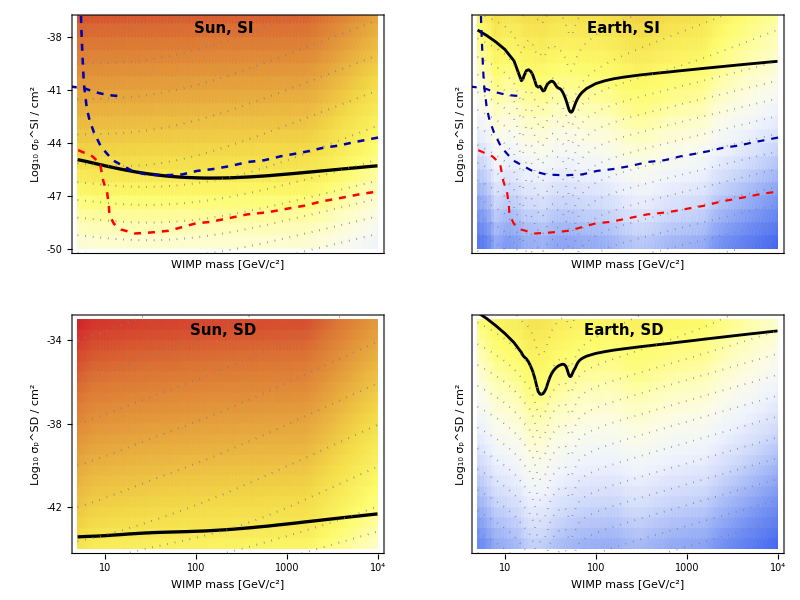
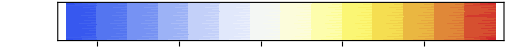

AnnRatePlot.pdf

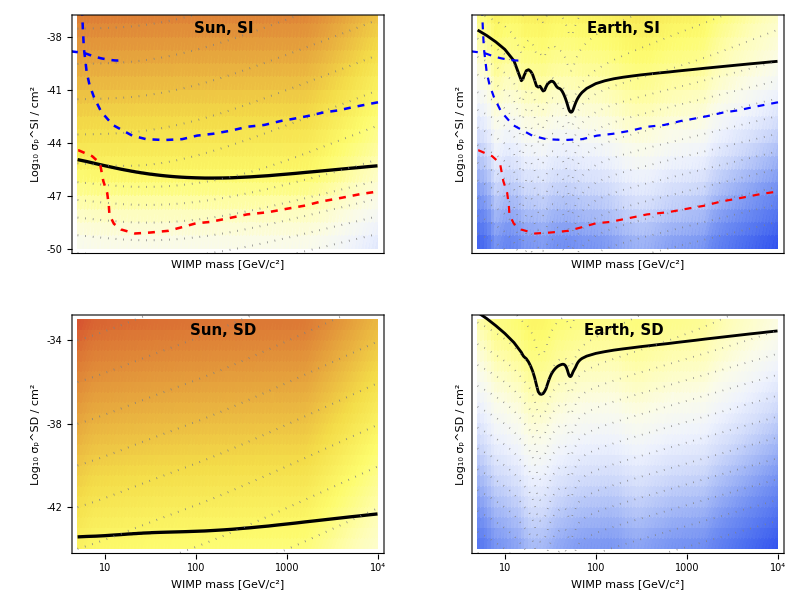
-Graphics--Graphics-

AnnRatePlot001.pdf

```mathematica
(*PlotAnnSunSI=ListDensityPlot[AnnRateSunSI,Mesh->None,ColorFunction->"Rainbow",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log[10,σSITab[[1]]]-44,Log[10,σSITab[[NSI]]]-44}}];*)
PlotAnnRateSunSI=Show[SunSIFrame,PlotListGridSITot[[1]],PlotSunSIσ,PlotSSI08f1,PlotSSI10f1,PlotSSI12f1,PlotSSI14f1,PlotSSI16f1,PlotSSI18f1,PlotSSI20f1,PlotSSI22f1,PlotSSI24f1,PlotSSI26f1,PlotSSI28f1,PlotSSI30f1,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-49.3}],Inset[Graphics[Text[Style["12",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-47.3}],Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-45.1}],Inset[Graphics[Text[Style["20",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-41.3}],Inset[Graphics[Text[Style["24",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.3}],Inset[Graphics[Text[Style["28",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.6}],CDMSLabel,LUXLabel,NuFloorLabel}];
PlotAnnRateEarthSI=Show[EarthSIFrame,PlotListGridSITot[[2]],PlotEarthSIσ,PlotESIm8f1,PlotESIm6f1,PlotESIm4f1,PlotESIm2f1,PlotESI00f1,PlotESI02f1,PlotESI04f1,PlotESI06f1,PlotESI08f1,PlotESI10f1,PlotESI12f1,PlotESI14f1,PlotESI16f1,PlotESI18f1,PlotESI20f1,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["-6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-48.7}],Inset[Graphics[Text[Style["-2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-46.7}],Inset[Graphics[Text[Style["2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-44.7}],Inset[Graphics[Text[Style["6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.7}],Inset[Graphics[Text[Style["10",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.7}],Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.8}],Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.4}],CDMSLabel,LUXLabel,NuFloorLabel}];
PlotAnnRateSunSD=Show[SunSDFrame,PlotListGridSDTot[[1]],PlotSunSDσ,PlotSSD14f1,PlotSSD16f1,PlotSSD18f1,PlotSSD20f1,PlotSSD22f1,PlotSSD24f1,PlotSSD26f1,PlotSSD28f1,PlotSSD30f1,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.1}],Inset[Graphics[Text[Style["20",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.3}],Inset[Graphics[Text[Style["24",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.2}],Inset[Graphics[Text[Style["28",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-35.7}],PICOLabel}];
PlotAnnRateEarthSD=Show[EarthSDFrame,PlotListGridSDTot[[2]],PlotEarthSDσ,PlotESDm6f1,PlotESDm4f1,PlotESDm2f1,PlotESD00f1,PlotESD02f1,PlotESD04f1,PlotESD06f1,PlotESD08f1,PlotESD10f1,PlotESD12f1,PlotESD14f1,PlotESD16f1,PlotESD18f1,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{1.2,-33.3}],Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.2,-33.3}],Inset[Graphics[Text[Style["10",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.9}],Inset[Graphics[Text[Style["6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-36.8}],Inset[Graphics[Text[Style["2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.9}],Inset[Graphics[Text[Style["-2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.9}],Inset[Graphics[Text[Style["-6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.9}],PICOLabel}];
AnnRatePlot=Labeled[grid=Grid[{{PlotAnnRateSunSI,PlotAnnRateEarthSI},{PlotAnnRateSunSD,PlotAnnRateEarthSD}},Frame->All],DensityPlot[y,{y,minplot,maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{ylab,""},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5 First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]

(*Grid[{{PlotAnnRateSunSI,PlotAnnRateEarthSI},{PlotAnnRateSunSD,PlotAnnRateEarthSD}},Frame->All]*)

Export["AnnRatePlot.pdf",AnnRatePlot,"pdf"]

(*PlotAnnSunSI=ListDensityPlot[AnnRateSunSI,Mesh->None,ColorFunction->"Rainbow",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log[10,σSITab[[1]]]-44,Log[10,σSITab[[NSI]]]-44}}];*)
PlotAnnRateSunSI001=Show[SunSIFrame,PlotListGridSITot[[3]],PlotSunSIσ,PlotSSI06001,PlotSSI08001,PlotSSI10001,PlotSSI12001,PlotSSI14001,PlotSSI16001,PlotSSI18001,PlotSSI20001,PlotSSI22001,PlotSSI24001,PlotSSI26001,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-49.3}],Inset[Graphics[Text[Style["10",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-47.3}],Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-45.1}],Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-41.4}],Inset[Graphics[Text[Style["22",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.3}],Inset[Graphics[Text[Style["26",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.6}],CDMSLabel001,LUXLabel001,NuFloorLabel}];
PlotAnnRateEarthSI001=Show[EarthSIFrame,PlotListGridSITot[[4]],PlotEarthSIσ,PlotESIm8001,PlotESIm6001,PlotESIm4001,PlotESIm2001,PlotESI00001,PlotESI02001,PlotESI04001,PlotESI06001,PlotESI08001,PlotESI10001,PlotESI12001,PlotESI14001,PlotESI16001,PlotESI18001,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["-8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-48.7}],Inset[Graphics[Text[Style["-4",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-46.7}],Inset[Graphics[Text[Style["0",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-44.7}],Inset[Graphics[Text[Style["4",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.7}],Inset[Graphics[Text[Style["8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.7}],Inset[Graphics[Text[Style["12",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.8}],Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.4}],CDMSLabel001A,LUXLabel001,NuFloorLabel}];
PlotAnnRateSunSD001=Show[SunSDFrame,PlotListGridSDTot[[3]],PlotSunSDσ,PlotSSD14001,PlotSSD16001,PlotSSD18001,PlotSSD20001,PlotSSD22001,PlotSSD24001,PlotSSD26001,PlotSSD28001,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.1}],Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.3}],Inset[Graphics[Text[Style["22",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.2}],Inset[Graphics[Text[Style["26",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-35.7}],PICOLabel001}];
PlotAnnRateEarthSD001=Show[EarthSDFrame,PlotListGridSDTot[[4]],PlotEarthSDσ,PlotESDm8001,PlotESDm6001,PlotESDm4001,PlotESDm2001,PlotESD00001,PlotESD02001,PlotESD04001,PlotESD06001,PlotESD08001,PlotESD10001,PlotESD12001,PlotESD14001,PlotESD16001,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{1.2,-33.3}],Inset[Graphics[Text[Style["12",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.2,-33.3}],Inset[Graphics[Text[Style["8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.8}],Inset[Graphics[Text[Style["4",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-36.8}],Inset[Graphics[Text[Style["0",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.8}],Inset[Graphics[Text[Style["-4",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.8}],Inset[Graphics[Text[Style["-8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.8}],PICOLabel001}];
AnnRatePlot001=Labeled[grid=Grid[{{PlotAnnRateSunSI001,PlotAnnRateEarthSI001},{PlotAnnRateSunSD001,PlotAnnRateEarthSD001}},Frame->All],DensityPlot[y,{y,minplot,maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{ylab,"",},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["AnnRatePlot001.pdf",AnnRatePlot001,"pdf"]
```

```mathematica
SunSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
EarthSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
SunSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30},{-29,-29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
EarthSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30},{-29,-29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
PlotAnnRateSunSI=Show[SunSIFrame,PlotListGridSITot[[1]],PlotSunSIσ,PlotSSI08f1,PlotSSI10f1,PlotSSI12f1,PlotSSI14f1,PlotSSI16f1,PlotSSI18f1,PlotSSI20f1,PlotSSI22f1,PlotSSI24f1,PlotSSI26f1,PlotSSI28f1,PlotSSI30f1,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["8",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-49.3}],Inset[Graphics[Text[Style["12",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-47.3}],Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-45.1}],Inset[Graphics[Text[Style["20",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-41.3}],Inset[Graphics[Text[Style["24",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.3}],Inset[Graphics[Text[Style["28",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.6}],CDMSLabel,LUXLabel,NuFloorLabel}];
PlotAnnRateEarthSI=Show[EarthSIFrame,PlotListGridSITot[[2]],PlotEarthSIσ,PlotESIm8f1,PlotESIm6f1,PlotESIm4f1,PlotESIm2f1,PlotESI00f1,PlotESI02f1,PlotESI04f1,PlotESI06f1,PlotESI08f1,PlotESI10f1,PlotESI12f1,PlotESI14f1,PlotESI16f1,PlotESI18f1,PlotESI20f1,LUXPlot,CDMSLite2016SIPlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{Inset[Graphics[Text[Style["-6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-48.7}],Inset[Graphics[Text[Style["-2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-46.7}],Inset[Graphics[Text[Style["2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-44.7}],Inset[Graphics[Text[Style["6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.7}],Inset[Graphics[Text[Style["10",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.7}],Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-37.8}],Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-37.4}],CDMSLabel,LUXLabel,NuFloorLabel}];
PlotAnnRateSunSD=Show[SunSDFrame,PlotListGridSDTot[[1]],PlotSunSDσ,PlotSSD14f1,PlotSSD16f1,PlotSSD18f1,PlotSSD20f1,PlotSSD22f1,PlotSSD24f1,PlotSSD26f1,PlotSSD28f1,PlotSSD30f1,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["16",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.1}],Inset[Graphics[Text[Style["20",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.3}],Inset[Graphics[Text[Style["24",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.2}],Inset[Graphics[Text[Style["28",FontFamily->"Times",FontSize->ipyf],{1,1}]],{0.95,-35.7}],PICOLabel}];
PlotAnnRateEarthSD=Show[EarthSDFrame,PlotListGridSDTot[[2]],PlotEarthSDσ,PlotESDm6f1,PlotESDm4f1,PlotESDm2f1,PlotESD00f1,PlotESD02f1,PlotESD04f1,PlotESD06f1,PlotESD08f1,PlotESD10f1,PlotESD12f1,PlotESD14f1,PlotESD16f1,PlotESD18f1,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{Inset[Graphics[Text[Style["18",FontFamily->"Times",FontSize->ipyf],{1,1}]],{1.2,-33.3}],Inset[Graphics[Text[Style["14",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.2,-33.3}],Inset[Graphics[Text[Style["10",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-34.9}],Inset[Graphics[Text[Style["6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-36.8}],Inset[Graphics[Text[Style["2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-38.9}],Inset[Graphics[Text[Style["-2",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-40.9}],Inset[Graphics[Text[Style["-6",FontFamily->"Times",FontSize->ipyf],{1,1}]],{3.9,-42.9}],PICOLabel}];
```

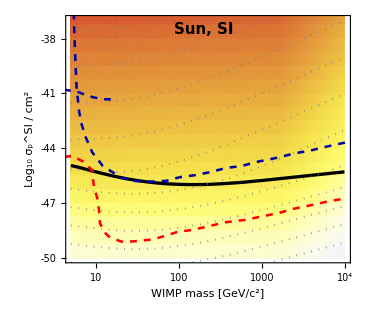
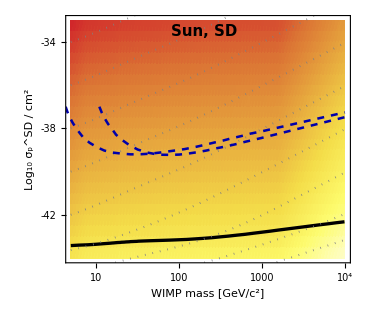
-Graphics--Graphics--Graphics-

AnnRatePlotSun.pdf

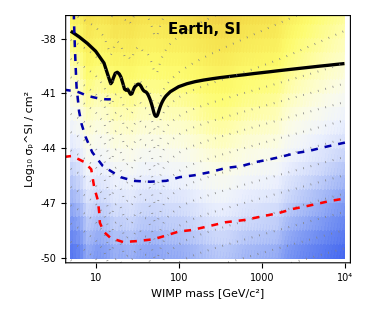
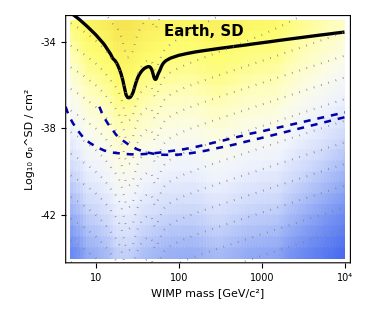
-Graphics--Graphics--Graphics-

AnnRatePlotEarth.pdf

```mathematica
AnnRatePlotSun=Labeled[grid=Row[{PlotAnnRateSunSI,PlotAnnRateSunSD},Frame->All],DensityPlot[y,{y,minplot,maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{ylab,""},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5 First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["AnnRatePlotSun.pdf",AnnRatePlotSun,"pdf"]

AnnRatePlotEarth=Labeled[grid=Row[{PlotAnnRateEarthSI,PlotAnnRateEarthSD},Frame->All],DensityPlot[y,{y,minplot,maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{ylab,""},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5 First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["AnnRatePlotEarth.pdf",AnnRatePlotEarth,"pdf"]
```

## Integrated neutrino flux

```mathematica
mcut=mW;
conv=3.154 10^17; (*conversion from cm^2 s to km^2 year*)
bthick=0.006;
dir={DG,DotDashed,Thickness[bthick]};
dird={DG,Dotted,Thickness[bthick]};
```

```mathematica
(*Labels Subscript[f, χ]=1*)
SKLabelSSI1=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],-π/15]],{1.4,-42.5}];
SKLabelSSI2=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/9]],{3.6,-39.6}];
ICLabelSSI=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/9]],{3.6,-41.2}];
SKLabelESI=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-40.45}];
ICLabelESI=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-41.7}];
SKLabelSSD1=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{1.4,-40.1}];
SKLabelSSD2=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/7]],{3.6,-36.7}];
ICLabelSSD=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/13]],{2.8,-39.6}];
SKLabelESD=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-34.6}];
ICLabelESD=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-35.7}];

BBSKLabelSSI1=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],-π/22]],{1.6,-40.7}];
BBSKLabelSSI2=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/9]],{3.6,-38.8}];
BBSKLabelSSD1=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{1.6,-38.1}];
BBSKLabelSSD2=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/7]],{3.6,-35.9}];
BBSKLabelESI=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],-π/4]],{1.3,-38.9}];
BBSKLabelESD=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],-π/4.75]],{1.4,-33.9}];
BBICLabelSSI=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/12]],{3.5,-40.5}];
BBICLabelSSD=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],-π/9]],{2.4,-36.9}];
BBICLabelESI=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-41}];
BBICLabelESD=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-35.1}];

(*Subscript[f, χ]=0.01*)
SKLabelSSI1001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],-π/15]],{1.4,-40.5}];
SKLabelSSI2001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/9]],{3.3,-38.1}];
SKLabelSSD1001=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{1.4,-38.1}];
SKLabelSSD2001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/7]],{3.7,-34.5}];
SKLabelESI001=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{1.8,-39.5}];
SKLabelESD001=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{1.8,-34.3}];
ICLabelSSI001=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/9]],{3.6,-39.3}];
ICLabelSSD001=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/12]],{2.8,-37.8}];
ICLabelESI001=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-40.6}];
ICLabelESD001=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-34.8}];

BBSKLabelSSI1001=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{2,-39.4}];
BBSKLabelSSI2001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/10]],{3.1,-37.7}];
BBICLabelSSI001=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/10]],{3.5,-38.5}];
BBSKLabelESI001=Inset[Graphics[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-38.3}];
BBICLabelESI001=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-39.1}];
BBSKLabelSSD1001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/24]],{2,-36.55}];
BBSKLabelSSD2001=Inset[Graphics[Rotate[Text[Style["SUPER-K",FontFamily->"Times",FontSize->lf],{1,1}],π/7]],{3.7,-33.8}];
BBICLabelSSD001=Inset[Graphics[Rotate[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}],π/14]],{3.4,-35.1}];
BBICLabelESD001=Inset[Graphics[Text[Style["IceCube",FontFamily->"Times",FontSize->lf],{1,1}]],{3.2,-33.3}];
```

```mathematica
(*Yields*)
WWEarth=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/WW_earth_mu.dat"];
WWEarthLog = {WWEarth[[Range[Length[WWEarth]],1]],Log[WWEarth[[Range[Length[WWEarth]],2]]]}//Transpose;
WWEarthF2=Interpolation[WWEarthLog,InterpolationOrder->1];
WWEarthF1[mm_]:=Exp[WWEarthF2[mm]];
TTEarth=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/tata_earth_mu.dat"];
TTEarthLog = {TTEarth[[Range[Length[TTEarth]],1]],Log[TTEarth[[Range[Length[TTEarth]],2]]]}//Transpose;
TTEarthF2=Interpolation[TTEarthLog,InterpolationOrder->1];
TTEarthF1[mm_]:=Exp[TTEarthF2[mm]];
WWEarthF[mm_]:=If[mm<mcut,TTEarthF1[mm],WWEarthF1[mm]];
BBEarth=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/bb_earth_mu.dat"];
BBEarthLog = {BBEarth[[Range[Length[BBEarth]],1]],Log[BBEarth[[Range[Length[BBEarth]],2]]]}//Transpose;
BBEarthF1=Interpolation[BBEarthLog,InterpolationOrder->1];
BBEarthF[mm_]:=Exp[BBEarthF1[mm]];
WWSun=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/WW_sun_mu.dat"];
WWSunLog = {WWSun[[Range[Length[WWSun]],1]],Log[WWSun[[Range[Length[WWSun]],2]]]}//Transpose;
WWSunF2=Interpolation[WWSunLog,InterpolationOrder->1];
WWSunF1[mm_]:=Exp[WWSunF2[mm]];TTSun=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/tata_sun_mu.dat"];
TTSunLog = {TTSun[[Range[Length[TTSun]],1]],Log[TTSun[[Range[Length[TTSun]],2]]]}//Transpose;
TTSunF2=Interpolation[TTSunLog,InterpolationOrder->1];
TTSunF1[mm_]:=Exp[TTSunF2[mm]];
WWSunF[mm_]:=If[mm<mcut,TTSunF1[mm],WWSunF1[mm]];
BBSun=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/bb_sun_mu.dat"];
BBSunLog = {BBSun[[Range[Length[BBSun]],1]],Log[BBSun[[Range[Length[BBSun]],2]]]}//Transpose;
BBSunF2=Interpolation[BBSunLog,InterpolationOrder->1];
BBSunF[mm_]:=Exp[BBSunF2[mm]];

WWSunle=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/WW_sun_muneu.dat"];
WWSunleLog = {WWSunle[[Range[Length[WWSunle]],1]],Log[WWSunle[[Range[Length[WWSunle]],2]]]}//Transpose;
WWSunleF2=Interpolation[WWSunleLog,InterpolationOrder->1];
WWSunleF1[mm_]:=Exp[WWSunleF2[mm]];
TTSunle=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/tautau_sun_muneu.dat"];
TTSunleLog = {TTSunle[[Range[Length[TTSunle]],1]],Log[TTSunle[[Range[Length[TTSunle]],2]]]}//Transpose;
TTSunleF2=Interpolation[TTSunleLog,InterpolationOrder->1];
TTSunleF1[mm_]:=Exp[TTSunleF2[mm]];
WWSunleF[mm_]:=If[mm<mcut,TTSunleF1[mm],WWSunleF1[mm]];
BBSunle=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoYieldTab/bb_sun_muneu.dat"];
BBSunleLog = {BBSunle[[Range[Length[BBSunle]],1]],Log[BBSunle[[Range[Length[BBSunle]],2]]]}//Transpose;
BBSunleF2=Interpolation[BBSunleLog,InterpolationOrder->1];
BBSunleF[mm_]:=Exp[BBSunleF2[mm]];
```

```mathematica
(*Muon bound from SuperK, Sun*)
SKSunWW=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Sun_TanakaThesis_fig7.8_WW.png.dat"];
(*SKSunWWF=Interpolation[SKSunWW,InterpolationOrder->1];*)
SKSunBB=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Sun_TanakaThesis_fig7.7_bb.png.dat"];
(*SKSunBBF=Interpolation[SKSunBB,InterpolationOrder->1];*)

SKSunleWW=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Sun_1503.04858_fig2_WW.png.dat"];
(*convert from neutrino to muon flux*)
SKSunleWWrs={{SKSunleWW[[1,1]],SKSunleWW[[1,2]]*WWSunF[SKSunleWW[[1,1]]]/WWSunleF[SKSunleWW[[1,1]]]}};
For[i=2,i≤Length[SKSunleWW],i++,
SKSunleWWrs=Append[SKSunleWWrs,{SKSunleWW[[i,1]],SKSunleWW[[i,2]]*WWSunF[SKSunleWW[[i,1]]]/WWSunleF[SKSunleWW[[i,1]]]}];];
(*SKSunleWWF1=Interpolation[SKSunleWW,InterpolationOrder->1];*)
(*SKSunleWWF[mm_]:= SKSunleWWF1[mm]*WWSunF[mm]/WWSunleF[mm];*)
SKSunleBB=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Sun_1503.04858_fig2_bb.png.dat"];
SKSunleBBrs={{SKSunleBB[[1,1]],SKSunleBB[[1,2]]*BBSunF[SKSunleBB[[1,1]]]/BBSunleF[SKSunleBB[[1,1]]]}};
For[i=2,i≤Length[SKSunleBB],i++,
SKSunleBBrs=Append[SKSunleBBrs,{SKSunleBB[[i,1]],SKSunleBB[[i,2]]*BBSunF[SKSunleBB[[i,1]]]/BBSunleF[SKSunleBB[[i,1]]]}];];
(*SKSunleBBF1=Interpolation[SKSunleBB,InterpolationOrder->1];
SKSunleBBF[mm_]:= SKSunleBBF1[mm]*BBSunF[mm]/BBSunleF[mm];*)
(*Muon bound from SuperK, Earth*)
SKEarthWW=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Earth_TanakaThesis_fig8.7_WW.png.dat"];
(*SKEarthWWF=Interpolation[SKEarthWW,InterpolationOrder->1];*)
SKEarthBB=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/SuperK_Earth_TanakaThesis_fig8.6_bb.png.dat"];
(*SKEarthBBF=Interpolation[SKEarthBB,InterpolationOrder->1];*)
(*Muon bound from ICeCube, Sun*)
ICSunWW=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/IceCube_Sun_1112.1840_fig5_WW.png.dat"];
(*ICSunWWF=Interpolation[ICSunWW,InterpolationOrder->1];*)
ICSunBB=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/IceCube_Sun_1112.1840_fig5_bb.png.dat"];
(*ICSunBBF=Interpolation[ICSunBB,InterpolationOrder->1];*)
(*Muon bound from ICeCube, Earth*)
ICEarthWW=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/IceCube_Earth_1609.01492_fig6_WW.png.dat"];
(*ICEarthWWF=Interpolation[ICEarthWW,InterpolationOrder->1];*)
ICEarthBB=Import["/Users/visinelli/Dropbox/LucaVisinelliArticoli/Published/Dark matter capture/NeutrinoBounds/IceCube_Earth_1609.01492_fig6_bb.png.dat"];
(*ICEarthBBF=Interpolation[ICEarthBB,InterpolationOrder->1];*)
```

InterpolatingFunction::dmval: Input value {3.9839992076`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84859482011`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.84589213518`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

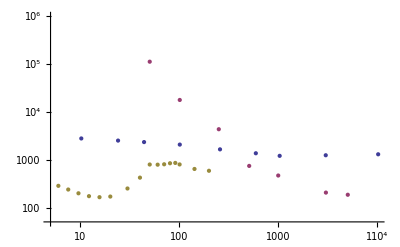

```mathematica
ListLogLogPlot[{SKSunBB,ICSunBB,SKSunleBBrs},InterpolationOrder->1,Joined->False,PlotRange->{{5,10^4},{50,10^6}}]
```

```mathematica
WWEarthSIfunct[mm_,ss_,fcdm_]:=conv ΓEarthSI[mm,ss,fcdm]WWEarthF[mm];
WWEarthSDfunct[mm_,ss_,fcdm_]:=conv ΓEarthSD[mm,ss,fcdm]WWEarthF[mm];
WWSunSIfunct[mm_,ss_,fcdm_]:=conv ΓSunSI[mm,ss,fcdm]WWSunF[mm];
WWSunSDfunct[mm_,ss_,fcdm_]:=conv ΓSunSD[mm,ss,fcdm]WWSunF[mm];
BBEarthSIfunct[mm_,ss_,fcdm_]:=conv ΓEarthSI[mm,ss,fcdm]BBEarthF[mm];
BBEarthSDfunct[mm_,ss_,fcdm_]:=conv ΓEarthSD[mm,ss,fcdm]BBEarthF[mm];
BBSunSIfunct[mm_,ss_,fcdm_]:=conv ΓSunSI[mm,ss,fcdm]BBSunF[mm];
BBSunSDfunct[mm_,ss_,fcdm_]:=conv ΓSunSD[mm,ss,fcdm]BBSunF[mm];
```

```mathematica
(*WW Bounds from SuperK, Sun, fχ=1*)
Remove[σWWSunSKSI1,σWWSunSKSD1,σWWSunSKleSI1,σWWSunSKleSD1];
σWWSunSKSI1=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSIfunct[SKSunWW[[i,1]],ss,1]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSI1[[i]]=10^4 σSI ss/.sol}];
σWWSunSKSI1={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSI1[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSI1Plot=ListPlot[Log10[σWWSunSKSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKSD1=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSDfunct[SKSunWW[[i,1]],ss,1]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSD1[[i]]=10^4 σSD ss/.sol}];
σWWSunSKSD1={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSD1[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSD1Plot=ListPlot[Log10[σWWSunSKSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSI1=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSIfunct[SKSunleWWrs[[i,1]],ss,1]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSI1[[i]]=10^4 σSI ss/.sol}];
σWWSunSKleSI1={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSI1[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSI1Plot=ListPlot[Log10[σWWSunSKleSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSD1=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSDfunct[SKSunleWWrs[[i,1]],ss,1]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSD1[[i]]=10^4 σSD ss/.sol}];
σWWSunSKleSD1={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSD1[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSD1Plot=ListPlot[Log10[σWWSunSKleSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from SuperK, Sun, fχ=0.01*)
Remove[σWWSunSKSI001,σWWSunSKSD001,σWWSunSKleSI001,σWWSunSKleSD001];
σWWSunSKSI001=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSIfunct[SKSunWW[[i,1]],ss,fcdm001]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSI001[[i]]=10^4 σSI ss/.sol}];
σWWSunSKSI001={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSI001[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSI001Plot=ListPlot[Log10[σWWSunSKSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKSD001=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSDfunct[SKSunWW[[i,1]],ss,fcdm001]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSD001[[i]]=10^4 σSD ss/.sol}];
σWWSunSKSD001={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSD001[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSD001Plot=ListPlot[Log10[σWWSunSKSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSI001=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSIfunct[SKSunleWWrs[[i,1]],ss,fcdm001]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSI001[[i]]=10^4 σSI ss/.sol}];
σWWSunSKleSI001={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSI001[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSI001Plot=ListPlot[Log10[σWWSunSKleSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSD001=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSDfunct[SKSunleWWrs[[i,1]],ss,fcdm001]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSD001[[i]]=10^4 σSD ss/.sol}];
σWWSunSKleSD001={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSD001[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSD001Plot=ListPlot[Log10[σWWSunSKleSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from SuperK, Sun, fχ=10^-4*)
(*Remove[σWWSunSKSIm4,σWWSunSKSDm4,σWWSunSKleSIm4,σWWSunSKleSDm4];
σWWSunSKSIm4=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSIfunct[SKSunWW[[i,1]],ss,fcdmm4]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSIm4[[i]]=10^4 σSI ss/.sol}];
σWWSunSKSIm4={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSIm4[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSIm4Plot=ListPlot[Log10[σWWSunSKSIm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKSDm4=Table[1,{i,1,Length[SKSunWW]}];
For[i=1,i≤Length[SKSunWW],i++,{sol=FindRoot[WWSunSDfunct[SKSunWW[[i,1]],ss,fcdmm4]==SKSunWW[[i,2]],{ss,1,10}];σWWSunSKSDm4[[i]]=10^4 σSD ss/.sol}];
σWWSunSKSDm4={SKSunWW[[Range[Length[SKSunWW]],1]],σWWSunSKSDm4[[Range[Length[SKSunWW]]]]}//Transpose;
WWSunSKSDm4Plot=ListPlot[Log10[σWWSunSKSDm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSIm4=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSIfunct[SKSunleWWrs[[i,1]],ss,fcdmm4]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSIm4[[i]]=10^4 σSI ss/.sol}];
σWWSunSKleSIm4={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSIm4[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSIm4Plot=ListPlot[Log10[σWWSunSKleSIm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunSKleSDm4=Table[1,{i,1,Length[SKSunleWWrs]}];
For[i=1,i≤Length[SKSunleWWrs],i++,{sol=FindRoot[WWSunSDfunct[SKSunleWWrs[[i,1]],ss,fcdmm4]==SKSunleWWrs[[i,2]],{ss,1,10}];σWWSunSKleSDm4[[i]]=10^4 σSD ss/.sol}];
σWWSunSKleSDm4={SKSunleWWrs[[Range[Length[SKSunleWWrs]],1]],σWWSunSKleSDm4[[Range[Length[SKSunleWWrs]]]]}//Transpose;
WWSunSKleSDm4Plot=ListPlot[Log10[σWWSunSKleSDm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];*)

(*BB Bounds from SuperK, Sun, fχ=1*)
Remove[σBBSunSKSI1,σBBSunSKSD1,σBBSunSKleSI1,σBBSunSKleSD1];
σBBSunSKSI1=Table[1,{i,1,Length[SKSunBB]}];
For[i=1,i≤Length[SKSunBB],i++,{sol=FindRoot[BBSunSIfunct[SKSunBB[[i,1]],ss,1]==SKSunBB[[i,2]],{ss,1,10}];σBBSunSKSI1[[i]]=10^4 σSI ss/.sol}];
σBBSunSKSI1={SKSunBB[[Range[Length[SKSunBB]],1]],σBBSunSKSI1[[Range[Length[SKSunBB]]]]}//Transpose;
BBSunSKSI1Plot=ListPlot[Log10[σBBSunSKSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKSD1=Table[1,{i,1,Length[SKSunBB]}];
For[i=1,i≤Length[SKSunBB],i++,{sol=FindRoot[BBSunSDfunct[SKSunBB[[i,1]],ss,1]==SKSunBB[[i,2]],{ss,1,10}];σBBSunSKSD1[[i]]=10^4 σSD ss/.sol}];
σBBSunSKSD1={SKSunBB[[Range[Length[SKSunBB]],1]],σBBSunSKSD1[[Range[Length[SKSunBB]]]]}//Transpose;
BBSunSKSD1Plot=ListPlot[Log10[σBBSunSKSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKleSI1=Table[1,{i,1,Length[SKSunleBBrs]}];
For[i=1,i≤Length[SKSunleBBrs],i++,{sol=FindRoot[BBSunSIfunct[SKSunleBBrs[[i,1]],ss,1]==SKSunleBBrs[[i,2]],{ss,1,10}];σBBSunSKleSI1[[i]]=10^4 σSI ss/.sol}];
σBBSunSKleSI1={SKSunleBBrs[[Range[Length[SKSunleBBrs]],1]],σBBSunSKleSI1[[Range[Length[SKSunleBBrs]]]]}//Transpose;
BBSunSKleSI1Plot=ListPlot[Log10[σBBSunSKleSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKleSD1=Table[1,{i,1,Length[SKSunleBBrs]}];
For[i=1,i≤Length[SKSunleBBrs],i++,{sol=FindRoot[BBSunSDfunct[SKSunleBBrs[[i,1]],ss,1]==SKSunleBBrs[[i,2]],{ss,1,10}];σBBSunSKleSD1[[i]]=10^4 σSD ss/.sol}];
σBBSunSKleSD1={SKSunleBBrs[[Range[Length[SKSunleBBrs]],1]],σBBSunSKleSD1[[Range[Length[SKSunleBBrs]]]]}//Transpose;
BBSunSKleSD1Plot=ListPlot[Log10[σBBSunSKleSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*BB Bounds from SuperK, Sun, fχ=0.01*)
Remove[σBBSunSKSI001,σBBSunSKSD001,σBBSunSKleSI001,σBBSunSKleSD001];
σBBSunSKSI001=Table[1,{i,1,Length[SKSunBB]}];
For[i=1,i≤Length[SKSunBB],i++,{sol=FindRoot[BBSunSIfunct[SKSunBB[[i,1]],ss,fcdm001]==SKSunBB[[i,2]],{ss,1,10}];σBBSunSKSI001[[i]]=10^4 σSI ss/.sol}];
σBBSunSKSI001={SKSunBB[[Range[Length[SKSunBB]],1]],σBBSunSKSI001[[Range[Length[SKSunBB]]]]}//Transpose;
BBSunSKSI001Plot=ListPlot[Log10[σBBSunSKSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKSD001=Table[1,{i,1,Length[SKSunBB]}];
For[i=1,i≤Length[SKSunBB],i++,{sol=FindRoot[BBSunSDfunct[SKSunBB[[i,1]],ss,fcdm001]==SKSunBB[[i,2]],{ss,1,10}];σBBSunSKSD001[[i]]=10^4 σSD ss/.sol}];
σBBSunSKSD001={SKSunBB[[Range[Length[SKSunBB]],1]],σBBSunSKSD001[[Range[Length[SKSunBB]]]]}//Transpose;
BBSunSKSD001Plot=ListPlot[Log10[σBBSunSKSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKleSI001=Table[1,{i,1,Length[SKSunleBBrs]}];
For[i=1,i≤Length[SKSunleBBrs],i++,{sol=FindRoot[BBSunSIfunct[SKSunleBBrs[[i,1]],ss,fcdm001]==SKSunleBBrs[[i,2]],{ss,1,10}];σBBSunSKleSI001[[i]]=10^4 σSI ss/.sol}];
σBBSunSKleSI001={SKSunleBBrs[[Range[Length[SKSunleBBrs]],1]],σBBSunSKleSI001[[Range[Length[SKSunleBBrs]]]]}//Transpose;
BBSunSKleSI001Plot=ListPlot[Log10[σBBSunSKleSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunSKleSD001=Table[1,{i,1,Length[SKSunleBBrs]}];
For[i=1,i≤Length[SKSunleBBrs],i++,{sol=FindRoot[BBSunSDfunct[SKSunleBBrs[[i,1]],ss,fcdm001]==SKSunleBBrs[[i,2]],{ss,1,10}];σBBSunSKleSD001[[i]]=10^4 σSD ss/.sol}];
σBBSunSKleSD001={SKSunleBBrs[[Range[Length[SKSunleBBrs]],1]],σBBSunSKleSD001[[Range[Length[SKSunleBBrs]]]]}//Transpose;
BBSunSKleSD001Plot=ListPlot[Log10[σBBSunSKleSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
```

InterpolatingFunction::dmval: Input value {9925.15635852`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.9839992076`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84859482011`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.9839992076`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84859482011`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9925.15635852`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.9839992076`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84859482011`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.9839992076`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84859482011`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10165.0265174`} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*WW Bounds from IceCube, Sun, fχ=1*)
Remove[σWWSunICSI1,σWWSunICSD1];
σWWSunICSI1=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSIfunct[ICSunWW[[i,1]],ss,1]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSI1[[i]]=10^4 σSI ss/.sol}];
σWWSunICSI1={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSI1[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSI1Plot=ListPlot[Log10[σWWSunICSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunICSD1=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSDfunct[ICSunWW[[i,1]],ss,1]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSD1[[i]]=10^4 σSD ss/.sol}];
σWWSunICSD1={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSD1[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSD1Plot=ListPlot[Log10[σWWSunICSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from IceCube, Sun, fχ=0.01*)
Remove[σWWSunICSI001,σWWSunICSD001];
σWWSunICSI001=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSIfunct[ICSunWW[[i,1]],ss,fcdm001]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSI001[[i]]=10^4 σSI ss/.sol}];
σWWSunICSI001={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSI001[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSI001Plot=ListPlot[Log10[σWWSunICSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunICSD001=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSDfunct[ICSunWW[[i,1]],ss,fcdm001]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSD001[[i]]=10^4 σSD ss/.sol}];
σWWSunICSD001={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSD001[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSD001Plot=ListPlot[Log10[σWWSunICSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from IceCube, Sun, fχ=10^-4*)
(*Remove[σWWSunICSIm4,σWWSunICSDm4];
σWWSunICSIm4=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSIfunct[ICSunWW[[i,1]],ss,fcdmm4]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSIm4[[i]]=10^4 σSI ss/.sol}];
σWWSunICSIm4={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSIm4[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSIm4Plot=ListPlot[Log10[σWWSunICSIm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWSunICSDm4=Table[1,{i,1,Length[ICSunWW]}];
For[i=1,i≤Length[ICSunWW],i++,{sol=FindRoot[WWSunSDfunct[ICSunWW[[i,1]],ss,fcdmm4]==ICSunWW[[i,2]],{ss,1,10}];σWWSunICSDm4[[i]]=10^4 σSD ss/.sol}];
σWWSunICSDm4={ICSunWW[[Range[Length[ICSunWW]],1]],σWWSunICSDm4[[Range[Length[ICSunWW]]]]}//Transpose;
WWSunICSDm4Plot=ListPlot[Log10[σWWSunICSDm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];*)

(*BB Bounds from IceCube, Sun, fχ=1*)
Remove[σBBSunICSI1,σBBSunICSD1];
σBBSunICSI1=Table[1,{i,1,Length[ICSunBB]}];
For[i=1,i≤Length[ICSunBB],i++,{sol=FindRoot[BBSunSIfunct[ICSunBB[[i,1]],ss,1]==ICSunBB[[i,2]],{ss,1,10}];σBBSunICSI1[[i]]=10^4 σSI ss/.sol}];
σBBSunICSI1={ICSunBB[[Range[Length[ICSunBB]],1]],σBBSunICSI1[[Range[Length[ICSunBB]]]]}//Transpose;
BBSunICSI1Plot=ListPlot[Log10[σBBSunICSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunICSD1=Table[1,{i,1,Length[ICSunBB]}];
For[i=1,i≤Length[ICSunBB],i++,{sol=FindRoot[BBSunSDfunct[ICSunBB[[i,1]],ss,1]==ICSunBB[[i,2]],{ss,1,10}];σBBSunICSD1[[i]]=10^4 σSD ss/.sol}];
σBBSunICSD1={ICSunBB[[Range[Length[ICSunBB]],1]],σBBSunICSD1[[Range[Length[ICSunBB]]]]}//Transpose;
BBSunICSD1Plot=ListPlot[Log10[σBBSunICSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*BB Bounds from IceCube, Sun, fχ=0.01*)
Remove[σBBSunICSI001,σBBSunICSD001];
σBBSunICSI001=Table[1,{i,1,Length[ICSunBB]}];
For[i=1,i≤Length[ICSunBB],i++,{sol=FindRoot[BBSunSIfunct[ICSunBB[[i,1]],ss,fcdm001]==ICSunBB[[i,2]],{ss,1,10}];σBBSunICSI001[[i]]=10^4 σSI ss/.sol}];
σBBSunICSI001={ICSunBB[[Range[Length[ICSunBB]],1]],σBBSunICSI001[[Range[Length[ICSunBB]]]]}//Transpose;
BBSunICSI001Plot=ListPlot[Log10[σBBSunICSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBSunICSD001=Table[1,{i,1,Length[ICSunBB]}];
For[i=1,i≤Length[ICSunBB],i++,{sol=FindRoot[BBSunSDfunct[ICSunBB[[i,1]],ss,fcdm001]==ICSunBB[[i,2]],{ss,1,10}];σBBSunICSD001[[i]]=10^4 σSD ss/.sol}];
σBBSunICSD001={ICSunBB[[Range[Length[ICSunBB]],1]],σBBSunICSD001[[Range[Length[ICSunBB]]]]}//Transpose;
BBSunICSD001Plot=ListPlot[Log10[σBBSunICSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
```

```mathematica
(*WW Bounds from SuperK, Earth, fχ=1*)
Remove[σWWEarthSKSI1,σWWEarthSKSD1,WWEarthSKSI1Plot,WWEarthSKSD1Plot];
σWWEarthSKSI1=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[SKEarthWW[[i,1]],ss,1]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSI1[[i]]=10^4 σSI ss/.sol}];
σWWEarthSKSI1={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSI1[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSI1Plot=ListPlot[Log10[σWWEarthSKSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthSKSD1=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[SKEarthWW[[i,1]],ss,1]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSD1[[i]]=10^4 σSD ss/.sol}];
σWWEarthSKSD1={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSD1[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSD1Plot=ListPlot[Log10[σWWEarthSKSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from SuperK, Earth, fχ=0.01*)
Remove[σWWEarthSKSI001,σWWEarthSKSD001,WWEarthSKSI001Plot,WWEarthSKSD001Plot];
σWWEarthSKSI001=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[SKEarthWW[[i,1]],ss,fcdm001]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSI001[[i]]=10^4 σSI ss/.sol}];
σWWEarthSKSI001={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSI001[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSI001Plot=ListPlot[Log10[σWWEarthSKSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthSKSD001=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[SKEarthWW[[i,1]],ss,fcdm001]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSD001[[i]]=10^4 σSD ss/.sol}];
σWWEarthSKSD001={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSD001[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSD001Plot=ListPlot[Log10[σWWEarthSKSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from SuperK, Earth, fχ=10^-4*)
(*Remove[σWWEarthSKSIm4,σWWEarthSKSDm4,WWEarthSKSIm4Plot,WWEarthSKSDm4Plot];
σWWEarthSKSIm4=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[SKEarthWW[[i,1]],ss,fcdmm4]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSIm4[[i]]=10^4 σSI ss/.sol}];
σWWEarthSKSIm4={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSIm4[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSIm4Plot=ListPlot[Log10[σWWEarthSKSIm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthSKSDm4=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[SKEarthWW[[i,1]],ss,fcdmm4]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSDm4[[i]]=10^4 σSD ss/.sol}];
σWWEarthSKSDm4={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSDm4[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSDm4Plot=ListPlot[Log10[σWWEarthSKSDm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];*)

(*BB Bounds from SuperK, Earth, fχ=1*)
Remove[σBBEarthSKSI1,σBBEarthSKSD1];
σBBEarthSKSI1=Table[1,{i,1,Length[SKEarthBB]}];
For[i=1,i≤Length[SKEarthBB],i++,{sol=FindRoot[BBEarthSIfunct[SKEarthBB[[i,1]],ss,1]==SKEarthBB[[i,2]],{ss,1,10}];σBBEarthSKSI1[[i]]=10^4 σSI ss/.sol}];
σBBEarthSKSI1={SKEarthBB[[Range[Length[SKEarthBB]],1]],σBBEarthSKSI1[[Range[Length[SKEarthBB]]]]}//Transpose;
BBEarthSKSI1Plot=ListPlot[Log10[σBBEarthSKSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBEarthSKSD1=Table[1,{i,1,Length[SKEarthBB]}];
For[i=1,i≤Length[SKEarthBB],i++,{sol=FindRoot[BBEarthSDfunct[SKEarthBB[[i,1]],ss,1]==SKEarthBB[[i,2]],{ss,1,10}];σBBEarthSKSD1[[i]]=10^4 σSD ss/.sol}];
σBBEarthSKSD1={SKEarthBB[[Range[Length[SKEarthBB]],1]],σBBEarthSKSD1[[Range[Length[SKEarthBB]]]]}//Transpose;
BBEarthSKSD1Plot=ListPlot[Log10[σBBEarthSKSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*BB Bounds from SuperK, Earth, fχ=0.01*)
Remove[σBBEarthSKSI001,σBBEarthSKSD001];
σBBEarthSKSI001=Table[1,{i,1,Length[SKEarthBB]}];
For[i=1,i≤Length[SKEarthBB],i++,{sol=FindRoot[BBEarthSIfunct[SKEarthBB[[i,1]],ss,fcdm001]==SKEarthBB[[i,2]],{ss,1,10}];σBBEarthSKSI001[[i]]=10^4 σSI ss/.sol}];
σBBEarthSKSI001={SKEarthBB[[Range[Length[SKEarthBB]],1]],σBBEarthSKSI001[[Range[Length[SKEarthBB]]]]}//Transpose;
BBEarthSKSI001Plot=ListPlot[Log10[σBBEarthSKSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBEarthSKSD001=Table[1,{i,1,Length[SKEarthBB]}];
For[i=1,i≤Length[SKEarthBB],i++,{sol=FindRoot[BBEarthSDfunct[SKEarthBB[[i,1]],ss,fcdm001]==SKEarthBB[[i,2]],{ss,1,10}];σBBEarthSKSD001[[i]]=10^4 σSD ss/.sol}];
σBBEarthSKSD001={SKEarthBB[[Range[Length[SKEarthBB]],1]],σBBEarthSKSD001[[Range[Length[SKEarthBB]]]]}//Transpose;
BBEarthSKSD001Plot=ListPlot[Log10[σBBEarthSKSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
```

InterpolatingFunction::dmval: Input value {9989.30216992`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10037.6023373`} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*WW Bounds from IceCube, Earth, fχ=1*)
Remove[σWWEarthICSI1,σWWEarthICSD1];
σWWEarthICSI1=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[ICEarthWW[[i,1]],ss,1]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSI1[[i]]=10^4 σSI ss/.sol}];
σWWEarthICSI1={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSI1[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSI1Plot=ListPlot[Log10[σWWEarthICSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthICSD1=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[ICEarthWW[[i,1]],ss,1]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSD1[[i]]=10^4 σSD ss/.sol}];
σWWEarthICSD1={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSD1[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSD1Plot=ListPlot[Log10[σWWEarthICSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from IceCube, Earth, fχ=0.01*)
Remove[σWWEarthICSI001,σWWEarthICSD001];
σWWEarthICSI001=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[ICEarthWW[[i,1]],ss,fcdm001]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSI001[[i]]=10^4 σSI ss/.sol}];
σWWEarthICSI001={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSI001[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSI001Plot=ListPlot[Log10[σWWEarthICSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthICSD001=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[ICEarthWW[[i,1]],ss,fcdm001]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSD001[[i]]=10^4 σSD ss/.sol}];
σWWEarthICSD001={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSD001[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSD001Plot=ListPlot[Log10[σWWEarthICSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*WW Bounds from IceCube, Earth, fχ=10^-4*)
(*Remove[σWWEarthICSIm4,σWWEarthICSDm4];
σWWEarthICSIm4=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSIfunct[ICEarthWW[[i,1]],ss,fcdmm4]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSIm4[[i]]=10^4 σSI ss/.sol}];
σWWEarthICSIm4={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSIm4[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSIm4Plot=ListPlot[Log10[σWWEarthICSIm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σWWEarthICSDm4=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSDfunct[ICEarthWW[[i,1]],ss,fcdmm4]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSDm4[[i]]=10^4 σSD ss/.sol}];
σWWEarthICSDm4={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSDm4[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSDm4Plot=ListPlot[Log10[σWWEarthICSDm4],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];*)

(*BB Bounds from IceCube, Earth, fχ=1*)
Remove[σBBEarthICSI1,σBBEarthICSD1];
σBBEarthICSI1=Table[1,{i,1,Length[ICEarthBB]}];
For[i=1,i≤Length[ICEarthBB],i++,{sol=FindRoot[BBEarthSIfunct[ICEarthBB[[i,1]],ss,1]==ICEarthBB[[i,2]],{ss,1,10}];σBBEarthICSI1[[i]]=10^4 σSI ss/.sol}];
σBBEarthICSI1={ICEarthBB[[Range[Length[ICEarthBB]],1]],σBBEarthICSI1[[Range[Length[ICEarthBB]]]]}//Transpose;
BBEarthICSI1Plot=ListPlot[Log10[σBBEarthICSI1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBEarthICSD1=Table[1,{i,1,Length[ICEarthBB]}];
For[i=1,i≤Length[ICEarthBB],i++,{sol=FindRoot[BBEarthSDfunct[ICEarthBB[[i,1]],ss,1]==ICEarthBB[[i,2]],{ss,1,10}];σBBEarthICSD1[[i]]=10^4 σSD ss/.sol}];
σBBEarthICSD1={ICEarthBB[[Range[Length[ICEarthBB]],1]],σBBEarthICSD1[[Range[Length[ICEarthBB]]]]}//Transpose;
BBEarthICSD1Plot=ListPlot[Log10[σBBEarthICSD1],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];

(*BB Bounds from IceCube, Earth, fχ=0.01*)
Remove[σBBEarthICSI001,σBBEarthICSD001];
σBBEarthICSI001=Table[1,{i,1,Length[ICEarthBB]}];
For[i=1,i≤Length[ICEarthBB],i++,{sol=FindRoot[BBEarthSIfunct[ICEarthBB[[i,1]],ss,fcdm001]==ICEarthBB[[i,2]],{ss,1,10}];σBBEarthICSI001[[i]]=10^4 σSI ss/.sol}];
σBBEarthICSI001={ICEarthBB[[Range[Length[ICEarthBB]],1]],σBBEarthICSI001[[Range[Length[ICEarthBB]]]]}//Transpose;
BBEarthICSI001Plot=ListPlot[Log10[σBBEarthICSI001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
σBBEarthICSD001=Table[1,{i,1,Length[ICEarthBB]}];
For[i=1,i≤Length[ICEarthBB],i++,{sol=FindRoot[BBEarthSDfunct[ICEarthBB[[i,1]],ss,fcdm001]==ICEarthBB[[i,2]],{ss,1,10}];σBBEarthICSD001[[i]]=10^4 σSD ss/.sol}];
σBBEarthICSD001={ICEarthBB[[Range[Length[ICEarthBB]],1]],σBBEarthICSD001[[Range[Length[ICEarthBB]]]]}//Transpose;
BBEarthICSD001Plot=ListPlot[Log10[σBBEarthICSD001],InterpolationOrder->1,Joined->True,PlotStyle->dir,PlotRange->All];
```

InterpolatingFunction::dmval: Input value {9908.152294`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9981.19904264`} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*DarkSUSY Earth composition, WW Bounds from SuperK and IceCube, fχ=1*)
WWEarthSDDSfunct[mm_,ss_,fcdm_]:=conv ΓEarthSDDS[mm,ss,fcdm]WWEarthF[mm];
Remove[σWWEarthSKSDDS1, σWWEarthICSDDS1];
σWWEarthSKSDDS1=Table[1,{i,1,Length[SKEarthWW]}];
For[i=1,i≤Length[SKEarthWW],i++,{sol=FindRoot[WWEarthSDDSfunct[SKEarthWW[[i,1]],ss,1]==SKEarthWW[[i,2]],{ss,1,10}];σWWEarthSKSDDS1[[i]]=10^4 σSD ss/.sol}];
σWWEarthSKSDDS1={SKEarthWW[[Range[Length[SKEarthWW]],1]],σWWEarthSKSDDS1[[Range[Length[SKEarthWW]]]]}//Transpose;
WWEarthSKSDDS1Plot=ListPlot[Log10[σWWEarthSKSDDS1],InterpolationOrder->1,Joined->True,PlotStyle->dird,PlotRange->All];
σWWEarthICSDDS1=Table[1,{i,1,Length[ICEarthWW]}];
For[i=1,i≤Length[ICEarthWW],i++,{sol=FindRoot[WWEarthSDDSfunct[ICEarthWW[[i,1]],ss,1]==ICEarthWW[[i,2]],{ss,1,10}];σWWEarthICSDDS1[[i]]=10^4 σSD ss/.sol}];
σWWEarthICSDDS1={ICEarthWW[[Range[Length[ICEarthWW]],1]],σWWEarthICSDDS1[[Range[Length[ICEarthWW]]]]}//Transpose;
WWEarthICSDDS1Plot=ListPlot[Log10[σWWEarthICSDDS1],InterpolationOrder->1,Joined->True,PlotStyle->dird,PlotRange->All];
```

InterpolatingFunction::dmval: Input value {9989.30216992`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9908.152294`} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
WWEarthSI1=Table[conv GammaEarthSI1[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
BBEarthSI1=Table[conv GammaEarthSI1[[j,i]]BBEarthF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
WWSunSI1=Table[conv GammaSunSI1[[j,i]]WWSunF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
BBSunSI1=Table[conv GammaSunSI1[[j,i]]BBSunF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
```

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
WWEarthSD1=Table[conv GammaEarthSD1[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
BBEarthSD1=Table[conv GammaEarthSD1[[j,i]]BBEarthF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
WWSunSD1=Table[conv GammaSunSD1[[j,i]]WWSunF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
BBSunSD1=Table[conv GammaSunSD1[[j,i]]BBSunF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
```

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
WWEarthSI001=Table[conv GammaEarthSI001[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
BBEarthSI001=Table[conv GammaEarthSI001[[j,i]]BBEarthF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
WWSunSI001=Table[conv GammaSunSI001[[j,i]]WWSunF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
BBSunSI001=Table[conv GammaSunSI001[[j,i]]BBSunF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
```

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
(*WWSunSIm4=Table[conv GammaSunSIm4[[j,i]]WWSunF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
WWSunSDm4=Table[conv GammaSunSDm4[[j,i]]WWSunF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
WWEarthSIm4=Table[conv GammaEarthSIm4[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSI},{i,1,NN}];
WWEarthSDm4=Table[conv GammaEarthSDm4[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSD},{i,1,NN}];*)
```

```mathematica
WWEarthSD001=Table[conv GammaEarthSD001[[j,i]]WWEarthF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
BBEarthSD001=Table[conv GammaEarthSD001[[j,i]]BBEarthF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
WWSunSD001=Table[conv GammaSunSD001[[j,i]]WWSunF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
BBSunSD001=Table[conv GammaSunSD001[[j,i]]BBSunF[mTab[[i]]],{j,1,NSD},{i,1,NN}];
```

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7845.2213026825175`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9876.548459095964`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
(*plotWWEarth1=ListLinePlot[Table[{Log10[mTab[[i]]],Log10[WWEarthM[[1,i]]]},{i,1,NN}]];
plotWWEarth5=ListLinePlot[Table[{Log10[mTab[[i]]],Log10[WWEarthM[[5,i]]]},{i,1,NN}]];
plotWWEarth10=ListLinePlot[Table[{Log10[mTab[[i]]],Log10[WWEarthM[[10,i]]]},{i,1,NN}]];
plotWWEarth15=ListLinePlot[Table[{Log10[mTab[[i]]],Log10[WWEarthM[[15,i]]]},{i,1,NN}]];
Show[plotWWEarth1,plotWWEarth5,plotWWEarth10,plotWWEarth15,PlotRange->All,Frame->True]*)
```

```mathematica
Maxplot=Max[Log10[WWSunSI1],Log10[BBSunSI1],Log10[WWEarthSI1],Log10[BBEarthSI1],Log10[WWSunSI001],Log10[BBSunSI001],Log10[WWEarthSI001],Log10[BBEarthSI001],Log10[WWSunSD1],Log10[BBSunSD1],Log10[WWEarthSD1],Log10[BBEarthSD1],Log10[WWSunSD001],Log10[BBSunSD001],Log10[WWEarthSD001],Log10[BBEarthSD001]];
Minplot=Min[Log10[WWSunSI1],Log10[BBSunSI1],Log10[WWEarthSI1],Log10[BBEarthSI1],Log10[WWSunSI001],Log10[BBSunSI001],Log10[WWEarthSI001],Log10[BBEarthSI001],Log10[WWSunSD1],Log10[BBSunSD1],Log10[WWEarthSD1],Log10[BBEarthSD1],Log10[WWSunSD001],Log10[BBSunSD001],Log10[WWEarthSD001],Log10[BBEarthSD001]];
Rangeplot=Maxplot-Minplot;
```

```mathematica
WWSunSI1=(Log10[WWSunSI1]-Minplot)/Rangeplot;
BBSunSI1=(Log10[BBSunSI1]-Minplot)/Rangeplot;
WWEarthSI1=(Log10[WWEarthSI1]-Minplot)/Rangeplot;
BBEarthSI1=(Log10[BBEarthSI1]-Minplot)/Rangeplot;
WWSunSD1=(Log10[WWSunSD1]-Minplot)/Rangeplot;
BBSunSD1=(Log10[BBSunSD1]-Minplot)/Rangeplot;
WWEarthSD1=(Log10[WWEarthSD1]-Minplot)/Rangeplot;
BBEarthSD1=(Log10[BBEarthSD1]-Minplot)/Rangeplot;
```

```mathematica
WWSunSI001=(Log10[WWSunSI001]-Minplot)/Rangeplot;
BBSunSI001=(Log10[BBSunSI001]-Minplot)/Rangeplot;
WWEarthSI001=(Log10[WWEarthSI001]-Minplot)/Rangeplot;
BBEarthSI001=(Log10[BBEarthSI001]-Minplot)/Rangeplot;
WWSunSD001=(Log10[WWSunSD001]-Minplot)/Rangeplot;
BBSunSD001=(Log10[BBSunSD001]-Minplot)/Rangeplot;
WWEarthSD001=(Log10[WWEarthSD001]-Minplot)/Rangeplot;
BBEarthSD001=(Log10[BBEarthSD001]-Minplot)/Rangeplot;
```

```mathematica
(*WWSunSIm4=(Log10[WWSunSIm4]-Minplot)/Rangeplot;
WWSunSDm4=(Log10[WWSunSDm4]-Minplot)/Rangeplot;
WWEarthSIm4=(Log10[WWEarthSIm4]-Minplot)/Rangeplot;
WWEarthSDm4=(Log10[WWEarthSDm4]-Minplot)/Rangeplot;*)
```

```mathematica
GridSunSITot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{WWSunSI1,BBSunSI1};
```

```mathematica
GridEarthSITot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{WWEarthSI1,BBEarthSI1};
```

```mathematica
GridSunSDTot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{WWSunSD1,BBSunSD1};
```

```mathematica
GridEarthSDTot=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{WWEarthSD1,BBEarthSD1};
```

```mathematica
GridSunSITot001=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{WWSunSI001,BBSunSI001};
```

```mathematica
GridEarthSITot001=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{WWEarthSI001,BBEarthSI001};
```

```mathematica
GridSunSDTot001=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{WWSunSD001,BBSunSD001};
```

```mathematica
GridEarthSDTot001=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{WWEarthSD001,BBEarthSD001};
```

```mathematica
(*GridWWm4SI=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSITab[[1]]σSI 10^4],Log10[σSITab[[NSI]]σSI 10^4]}},ColorFunctionScaling->False]&/@{WWSunSIm4,WWEarthSIm4};
GridWWm4SD=ListDensityPlot[#,Mesh->None,ColorFunction->"TemperatureMap",DataRange->{{Log[10,mTab[[1]]],Log[10,mTab[[NN]]]},{Log10[σSDTab[[1]]σSD 10^4],Log10[σSDTab[[NSD]]σSD 10^4]}},ColorFunctionScaling->False]&/@{WWSunSDm4,WWEarthSDm4};*)
```

```mathematica
(*Frames*)
x1=300;
y1=250;
pxr1=10;
pxl1=5;
pyu1=6;
pyd1=5;
pxax1=50;
pyax1=50;
ipyf=10;
thick=0.0055;
labelstyle={Bold,14};

SunSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1,pyu1}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
EarthSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1},ImagePadding->{{pxl1,pxr1},{pyd1,pyu1}},AspectRatio->Full];
SunSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30},{-29,-29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
EarthSDFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
```

```mathematica
(*WW channel*)
WWCountSunSI1=Show[SunSIFrame,GridSunSITot[[1]],PlotSunSIσ,WWSunSKleSI1Plot,WWSunSKSI1Plot,WWSunICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,SKLabelSSI1,SKLabelSSI2,ICLabelSSI,NuFloorLabel}];
WWCountSunSD1=Show[SunSDFrame,GridSunSDTot[[1]],PlotSunSDσ,WWSunSKleSD1Plot,WWSunSKSD1Plot,WWSunICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{PICOLabel,SKLabelSSD1,SKLabelSSD2,ICLabelSSD,NuFloorLabel}];
WWCountEarthSI1=Show[EarthSIFrame,GridEarthSITot[[1]],PlotEarthSIσ,WWEarthSKSI1Plot,WWEarthICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,SKLabelESI,ICLabelESI,NuFloorLabel}];
WWCountEarthSD1=Show[EarthSDFrame,GridEarthSDTot[[1]],PlotEarthSDσ,WWEarthSKSD1Plot,WWEarthICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43}]],Epilog->{PICOLabel,SKLabelESD,ICLabelESD,NuFloorLabel}];
WWCountSunSI001=Show[SunSIFrame,GridSunSITot001[[1]],PlotSunSIσ,WWSunSKleSI001Plot,WWSunSKSI001Plot,WWSunICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel001,LUXLabel001,SKLabelSSI1001,SKLabelSSI2001,ICLabelSSI001,NuFloorLabel}];
WWCountSunSD001=Show[SunSDFrame,GridSunSDTot001[[1]],PlotSunSDσ,WWSunSKleSD001Plot,WWSunSKSD001Plot,WWSunICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{PICOLabel001,SKLabelSSD1001,SKLabelSSD2001,ICLabelSSD001,NuFloorLabel}];
WWCountEarthSI001=Show[EarthSIFrame,GridEarthSITot001[[1]],PlotEarthSIσ,WWEarthSKSI001Plot,WWEarthICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel001A,LUXLabel001,SKLabelESI001,ICLabelESI001,NuFloorLabel}];
WWCountEarthSD001=Show[EarthSDFrame,GridEarthSDTot001[[1]],PlotEarthSDσ,WWEarthSKSD001Plot,WWEarthICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43}]],Epilog->{PICOLabel001,SKLabelESD001,ICLabelESD001,NuFloorLabel}];
```

```mathematica
(*BB channel*)
BBCountSunSI1=Show[SunSIFrame,GridSunSITot[[2]],PlotSunSIσ,BBSunSKleSI1Plot,BBSunSKSI1Plot,BBSunICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,BBSKLabelSSI1,BBSKLabelSSI2,BBICLabelSSI,NuFloorLabel}];
BBCountSunSD1=Show[SunSDFrame,GridSunSDTot[[2]],PlotSunSDσ,BBSunSKleSD1Plot,BBSunSKSD1Plot,BBSunICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{PICOLabelbb,BBSKLabelSSD1,BBSKLabelSSD2,BBICLabelSSD,NuFloorLabel}];
BBCountEarthSI1=Show[EarthSIFrame,GridEarthSITot[[2]],PlotEarthSIσ,BBEarthSKSI1Plot,BBEarthICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,BBSKLabelESI,BBICLabelESI,NuFloorLabel}];
BBCountEarthSD1=Show[EarthSDFrame,GridEarthSDTot[[2]],PlotEarthSDσ,BBEarthSKSD1Plot,BBEarthICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Graphics[Text[Style["bb̄, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43}]],Epilog->{PICOLabelbb,BBSKLabelESD,BBICLabelESD,NuFloorLabel}];
BBCountSunSI001=Show[SunSIFrame,GridSunSITot001[[2]],PlotSunSIσ,BBSunSKleSI001Plot,BBSunSKSI001Plot,BBSunICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel001,LUXLabel001,BBSKLabelSSI1001,BBSKLabelSSI2001,BBICLabelSSI001,NuFloorLabel}];
BBCountSunSD001=Show[SunSDFrame,GridSunSDTot001[[2]],PlotSunSDσ,BBSunSKleSD001Plot,BBSunSKSD001Plot,BBSunICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Epilog->{PICOLabelbb001,BBSKLabelSSD1001,BBSKLabelSSD2001,BBICLabelSSD001,NuFloorLabel}];
BBCountEarthSI001=Show[EarthSIFrame,GridEarthSITot001[[2]],PlotEarthSIσ,BBEarthSKSI001Plot,BBEarthICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{LUXLabel001,BBSKLabelESI001,BBICLabelESI001,NuFloorLabel}];
BBCountEarthSD001=Show[EarthSDFrame,GridEarthSDTot001[[2]],PlotEarthSDσ,BBEarthSKSD001Plot,BBEarthICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.5}]],Graphics[Text[Style["bb̄, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43}]],Epilog->{PICOLabelbb001,BBICLabelESD001,NuFloorLabel}];
```

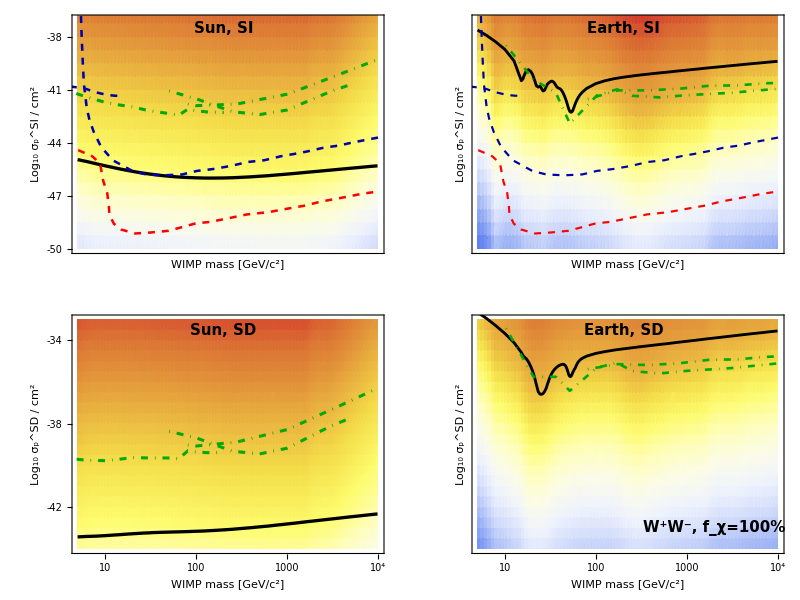
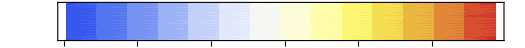

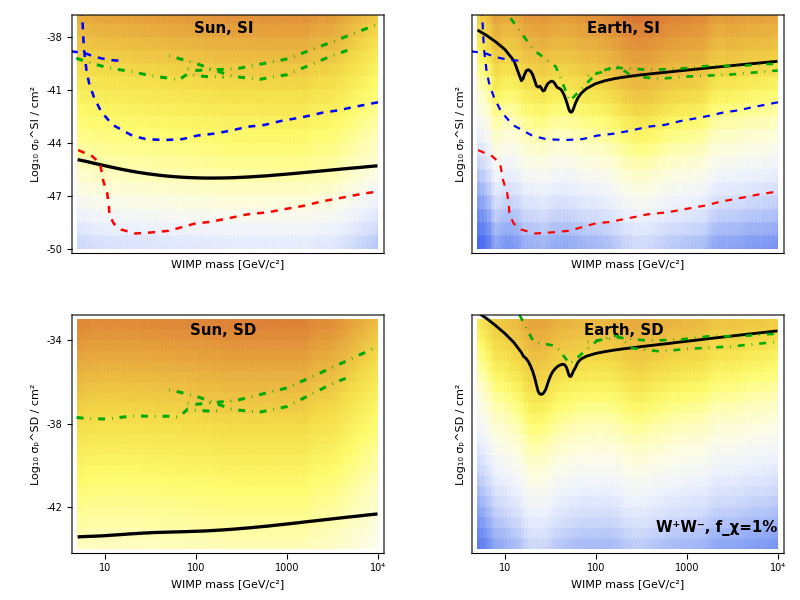
-Graphics--Graphics-

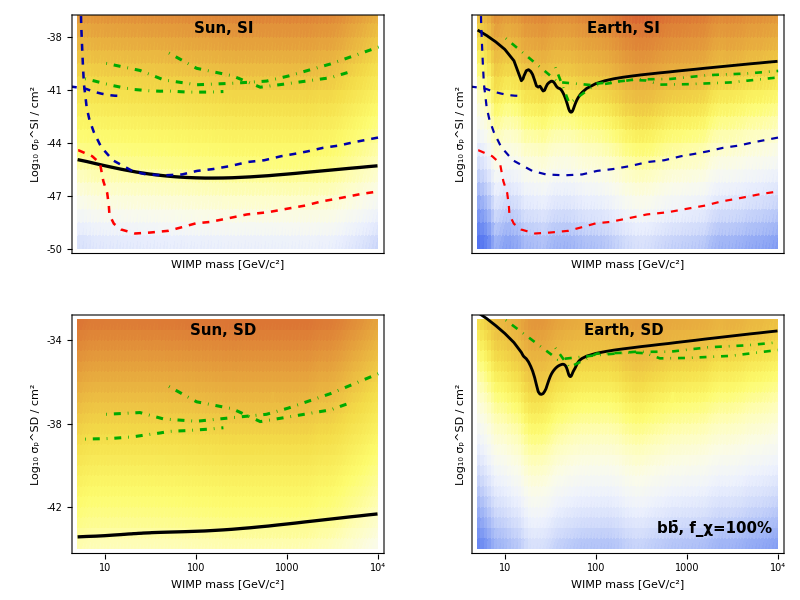
-Graphics--Graphics-

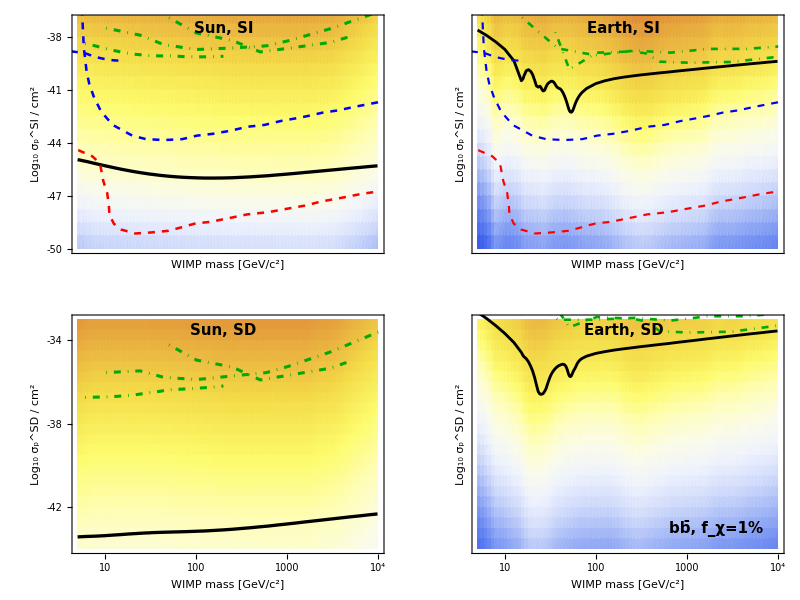
-Graphics--Graphics-

```mathematica
WWFluxPlot1=Labeled[grid=Grid[{{WWCountSunSI1,WWCountEarthSI1},{WWCountSunSD1,WWCountEarthSD1}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["WWFluxPlot1.pdf",WWFluxPlot1,"pdf"];

WWFluxPlot001=Labeled[grid=Grid[{{WWCountSunSI001,WWCountEarthSI001},{WWCountSunSD001,WWCountEarthSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["WWFluxPlot001.pdf",WWFluxPlot001,"pdf"];

BBFluxPlot1=Labeled[grid=Grid[{{BBCountSunSI1,BBCountEarthSI1},{BBCountSunSD1,BBCountEarthSD1}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["BBFluxPlot1.pdf",BBFluxPlot1,"pdf"];

BBFluxPlot001=Labeled[grid=Grid[{{BBCountSunSI001,BBCountEarthSI001},{BBCountSunSD001,BBCountEarthSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["BBFluxPlot001.pdf",BBFluxPlot001,"pdf"];
```

```mathematica
(*Frames*)
x1=300;
y1=250;
pxr1=10;
pxl1=5;
pyu1=6;
pyd1=5;
pxax1=50;
pyax1=50;
ipyf=10;
thick=0.0055;
labelstyle={Bold,14};

EarthSIFrame1=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""}}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1,pyu1}},AspectRatio->Full];
EarthSDFrame1=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
EarthSIFrame001=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1},ImagePadding->{{pxl1,pxr1},{pyd1,pyu1}},AspectRatio->Full];
EarthSDFrame001=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];

SunSIFrame1=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1,pyu1}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
SunSDFrame1=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33},{-32,-32},{-31,-31},{-30,-30},{-29,-29}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
SunSIFrame001=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1},ImagePadding->{{pxl1,pxr1},{pyd1,pyu1}},FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},AspectRatio->Full];
SunSDFrame001=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-44,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""},{-34,""},{-33,""},{-32,""},{-31,""},{-30,""},{-29,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
```

```mathematica
(*WW channel*)
WWCountEarthSI1=Show[EarthSIFrame1,GridEarthSITot[[1]],PlotEarthSIσ,WWEarthSKSI1Plot,WWEarthICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-49.4}]],Graphics[{Dashed,Line[{{m100TT,-50},{m100TT,0}}]}],Epilog->{CDMSLabel,LUXLabel,SKLabelESI,ICLabelESI,NuFloorLabel}];
WWCountEarthSD1=Show[EarthSDFrame1,GridEarthSDTot[[1]],PlotEarthSDσ,WWEarthSKSD1Plot,WWEarthICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43.4}]],Graphics[{Dashed,Line[{{m100TT,-50},{m100TT,0}}]}],Epilog->{PICOLabel,SKLabelESD,ICLabelESD,NuFloorLabel}];
WWCountEarthSI001=Show[EarthSIFrame001,GridEarthSITot001[[1]],PlotEarthSIσ,WWEarthSKSI001Plot,WWEarthICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["W^+W^-, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-49.4}]],Graphics[{Dashed,Line[{{m1TT,-50},{m1TT,0}}]}],Epilog->{CDMSLabel001A,LUXLabel001,SKLabelESI001,ICLabelESI001,NuFloorLabel}];
WWCountEarthSD001=Show[EarthSDFrame001,GridEarthSDTot001[[1]],PlotEarthSDσ,WWEarthSKSD001Plot,WWEarthICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43.4}]],Graphics[{Dashed,Line[{{m1TT,-50},{m1TT,0}}]}],Epilog->{PICOLabel001,SKLabelESD001,ICLabelESD001,NuFloorLabel}];


WWCountSunSI1=Show[SunSIFrame1,GridSunSITot[[1]],PlotSunSIσ,WWSunSKleSI1Plot,WWSunSKSI1Plot,WWSunICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-49.4}]],Graphics[{Dashed,Line[{{m100TT,-50},{m100TT,0}}]}],Epilog->{CDMSLabel,LUXLabel,SKLabelSSI1,SKLabelSSI2,ICLabelSSI,NuFloorLabel}];
WWCountSunSD1=Show[SunSDFrame1,GridSunSDTot[[1]],PlotSunSDσ,WWSunSKleSD1Plot,WWSunSKSD1Plot,WWSunICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43.4}]],Graphics[{Dashed,Line[{{m100TT,-50},{m100TT,0}}]}],Epilog->{PICOLabel,SKLabelSSD1,SKLabelSSD2,ICLabelSSD,NuFloorLabel}];
WWCountSunSI001=Show[SunSIFrame001,GridSunSITot001[[1]],PlotSunSIσ,WWSunSKleSI001Plot,WWSunSKSI001Plot,WWSunICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["W^+W^-, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-49.4}]],Graphics[{Dashed,Line[{{m1TT,-50},{m1TT,0}}]}],Epilog->{CDMSLabel001,LUXLabel001,SKLabelSSI1001,SKLabelSSI2001,ICLabelSSI001,NuFloorLabel}];
WWCountSunSD001=Show[SunSDFrame001,GridSunSDTot001[[1]],PlotSunSDσ,WWSunSKleSD001Plot,WWSunSKSD001Plot,WWSunICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["W^+W^-, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43.4}]],Graphics[{Dashed,Line[{{m1TT,-50},{m1TT,0}}]}],Epilog->{PICOLabel001,SKLabelSSD1001,SKLabelSSD2001,ICLabelSSD001,NuFloorLabel}];
```

```mathematica
(*BB channel*)
BBCountEarthSI1=Show[EarthSIFrame1,GridEarthSITot[[2]],PlotEarthSIσ,BBEarthSKSI1Plot,BBEarthICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["bb̄, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-49.4}]],Graphics[{Dashed,Line[{{m100BB,-50},{m100BB,0}}]}],Epilog->{CDMSLabel,LUXLabel,BBSKLabelESI,BBICLabelESI,NuFloorLabel}];
BBCountEarthSD1=Show[EarthSDFrame1,GridEarthSDTot[[2]],PlotEarthSDσ,BBEarthSKSD1Plot,BBEarthICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["bb̄, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43.4}]],Graphics[{Dashed,Line[{{m100BB,-50},{m100BB,0}}]}],Epilog->{PICOLabelbb,BBSKLabelESD,BBICLabelESD,NuFloorLabel}];
BBCountEarthSI001=Show[EarthSIFrame001,GridEarthSITot001[[2]],PlotEarthSIσ,BBEarthSKSI001Plot,BBEarthICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Earth, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["bb̄, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-49.4}]],Graphics[{Dashed,Line[{{m1BB,-50},{m1BB,0}}]}],Epilog->{LUXLabel001,BBSKLabelESI001,BBICLabelESI001,NuFloorLabel}];
BBCountEarthSD001=Show[EarthSDFrame001,GridEarthSDTot001[[2]],PlotEarthSDσ,BBEarthSKSD001Plot,BBEarthICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["bb̄, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43.4}]],Graphics[{Dashed,Line[{{m1BB,-50},{m1BB,0}}]}],Epilog->{PICOLabelbb001,BBICLabelESD001,NuFloorLabel}];

BBCountSunSI1=Show[SunSIFrame1,GridSunSITot[[2]],PlotSunSIσ,BBSunSKleSI1Plot,BBSunSKSI1Plot,BBSunICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["bb̄, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-49.4}]],Graphics[{Dashed,Line[{{m100BB,-50},{m100BB,0}}]}],Epilog->{CDMSLabel,LUXLabel,BBSKLabelSSI1,BBSKLabelSSI2,BBICLabelSSI,NuFloorLabel}];
BBCountSunSD1=Show[SunSDFrame1,GridSunSDTot[[2]],PlotSunSDσ,BBSunSKleSD1Plot,BBSunSKSD1Plot,BBSunICSD1Plot,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["bb̄, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43.4}]],Graphics[{Dashed,Line[{{m100BB,-50},{m100BB,0}}]}],Epilog->{PICOLabelbb,BBSKLabelSSD1,BBSKLabelSSD2,BBICLabelSSD,NuFloorLabel}];
BBCountSunSI001=Show[SunSIFrame001,GridSunSITot001[[2]],PlotSunSIσ,BBSunSKleSI001Plot,BBSunSKSI001Plot,BBSunICSI001Plot,LUXPlot001,CDMSLitePlot001,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-37.5}]],Graphics[Text[Style["bb̄, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-49.4}]],Graphics[{Dashed,Line[{{m1BB,-50},{m1BB,0}}]}],Epilog->{CDMSLabel001,LUXLabel001,BBSKLabelSSI1001,BBSKLabelSSI2001,BBICLabelSSI001,NuFloorLabel}];
BBCountSunSD001=Show[SunSDFrame001,GridSunSDTot001[[2]],PlotSunSDσ,BBSunSKleSD001Plot,BBSunSKSD001Plot,BBSunICSD001Plot,PICO2016SD60Plot001,PICO2016SD2LPlot001,Graphics[Text[Style["Sun, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[300],-33.5}]],Graphics[Text[Style["bb̄, f_χ=1%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2100],-43.4}]],Graphics[{Dashed,Line[{{m1BB,-50},{m1BB,0}}]}],Epilog->{PICOLabelbb001,BBSKLabelSSD1001,BBSKLabelSSD2001,BBICLabelSSD001,NuFloorLabel}];
```

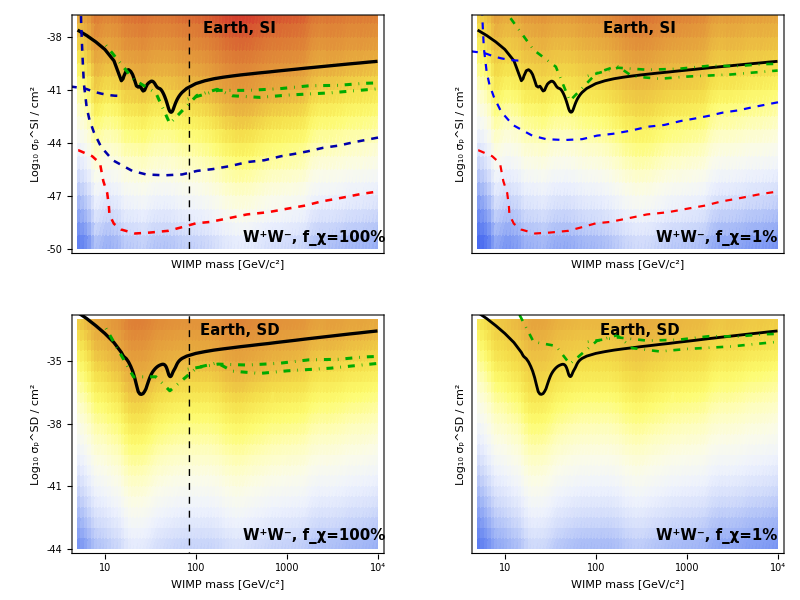
-Graphics--Graphics-

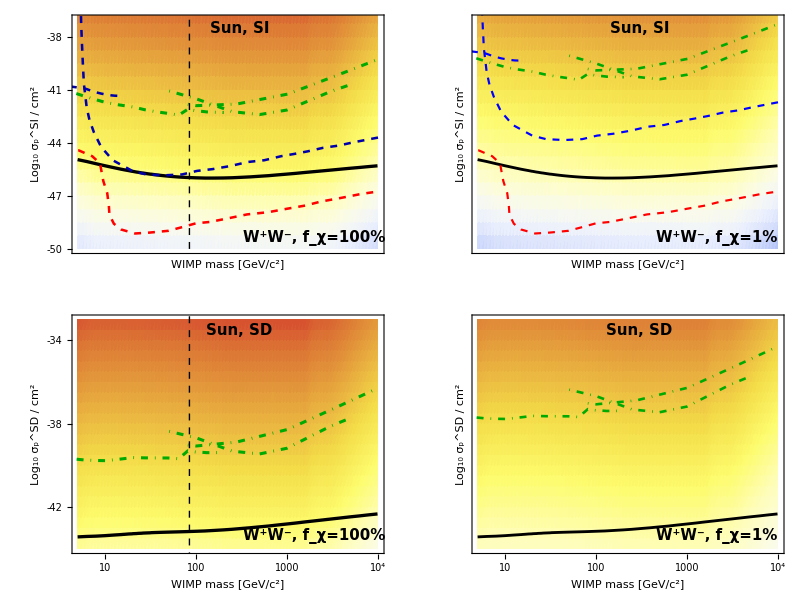
-Graphics--Graphics-

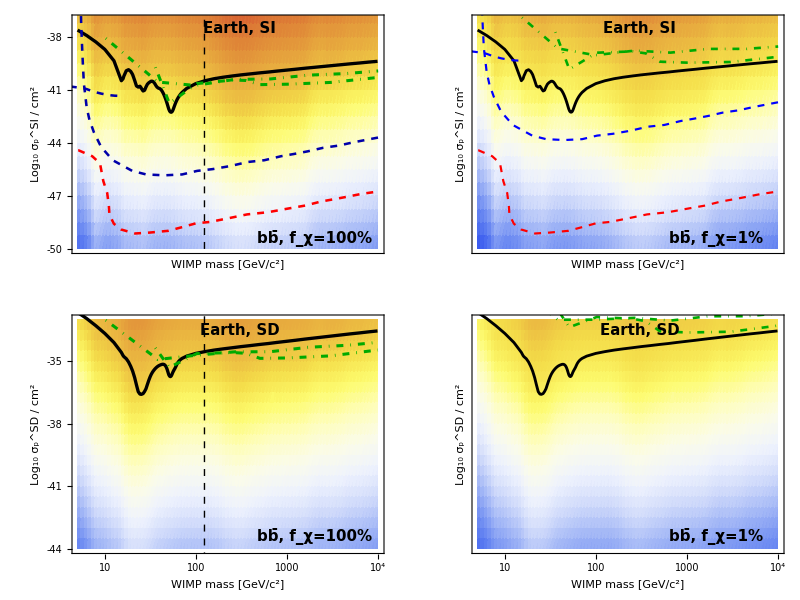
-Graphics--Graphics-

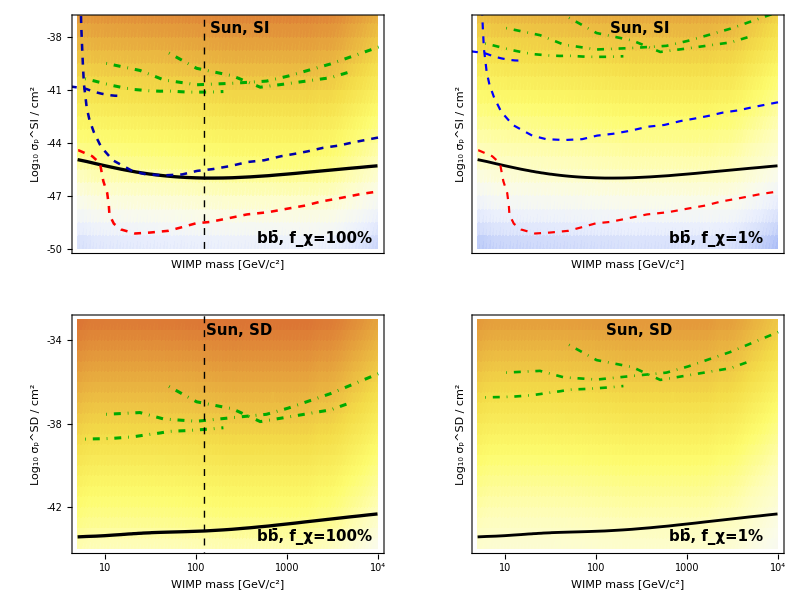
-Graphics--Graphics-

```mathematica
WWEarthPlot=Labeled[grid=Grid[{{WWCountEarthSI1,WWCountEarthSI001},{WWCountEarthSD1,WWCountEarthSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["WWEarthPlot.pdf",WWEarthPlot,"pdf"];

WWSunPlot=Labeled[grid=Grid[{{WWCountSunSI1,WWCountSunSI001},{WWCountSunSD1,WWCountSunSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["WWSunPlot.pdf",WWSunPlot,"pdf"];

BBEarthPlot=Labeled[grid=Grid[{{BBCountEarthSI1,BBCountEarthSI001},{BBCountEarthSD1,BBCountEarthSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["BBEarthPlot.pdf",BBEarthPlot,"pdf"];

BBSunPlot=Labeled[grid=Grid[{{BBCountSunSI1,BBCountSunSI001},{BBCountSunSD1,BBCountSunSD001}},Frame->All],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->1.5First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["BBSunPlot.pdf",BBSunPlot,"pdf"];
```

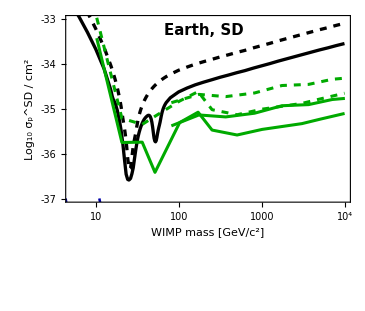

ComparisonPlot.pdf

```mathematica
EarthSDDSFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-37,-33}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-37,-37},{-36,-36},{-35,-35},{-34,-34},{-33,-33}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-37,""},{-36,""},{-35,""},{-34,""},{-33,""}}},FrameLabel->{{ylabSD,""},{"WIMP mass [GeV/c^2]",""}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
WWEarthSKSD1Plot1=ListPlot[Log10[σWWEarthSKSD1],InterpolationOrder->1,Joined->True,PlotStyle->{DG,Thickness[bthick]},PlotRange->All];
WWEarthSKSDDS1Plot1=ListPlot[Log10[σWWEarthSKSDDS1],InterpolationOrder->1,Joined->True,PlotStyle->{DG,Dashed,Thickness[bthick]},PlotRange->All];
WWEarthICSD1Plot1=ListPlot[Log10[σWWEarthICSD1],InterpolationOrder->1,Joined->True,PlotStyle->{DG,Thickness[bthick]},PlotRange->All];
WWEarthICSDDS1Plot1=ListPlot[Log10[σWWEarthICSDDS1],InterpolationOrder->1,Joined->True,PlotStyle->{DG,Dashed,Thickness[bthick]},PlotRange->All];

ComparisonPlot=Show[EarthSDDSFrame,PlotEarthSDσ,PlotEarthSDDSσ,WWEarthSKSD1Plot1,WWEarthSKSDDS1Plot1,WWEarthICSD1Plot1,WWEarthICSDDS1Plot1,PICO2016SD60Plot,PICO2016SD2LPlot,Graphics[Text[Style["Earth, SD",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-33.25}]],Graphics[Text[Style["W^+W^-, f_χ=100%",FontSize->15,FontFamily->"Times",FontWeight->"Bold",SingleLetterItalics->False],{Log10[2000],-43}]],Epilog->{PICOLabel,NuFloorLabel}]
Export["ComparisonPlot.pdf",ComparisonPlot,"pdf"]
```

```mathematica
(*Talks*)
```

```mathematica
SunSIFrame=Plot[-10,{x,10^-8,2.8},Frame->True,Axes->False,PlotRange->{{Log[10,5],4.},{-50,-37}},FrameTicks->{{{0,1},{1,10},{2,100},{3,1000},{4,Superscript[10,4]}},{{-50,-50},{-49,-49},{-48,-48},{-47,-47},{-46,-46},{-45,-45},{-44,-44},{-43,-43},{-42,-42},{-41,-41},{-40,-40},{-39,-39},{-38,-38},{-37,-37},{-36,-36},{-35,-35}},{{0,""},{1,""},{2,""},{3,""},{4,""}},{{-50,""},{-49,""},{-48,""},{-47,""},{-46,""},{-45,""},{-44,""},{-43,""},{-42,""},{-41,""},{-40,""},{-39,""},{-38,""},{-37,""},{-36,""},{-35,""}}},FrameStyle->Directive[Thickness[0.002],FontSize->14,FontFamily->"Times"],FrameLabel->{{ylabSI,""},{"WIMP mass [GeV/c^2]",""}},BaseStyle->{FontFamily->"Times",SingleLetterItalics->False},ImageSize->{x1+pxr1+pxl1+pxax1,y1+pyu1+pyd1+pyax1},ImagePadding->{{pxl1+pxax1,pxr1},{pyd1+pyax1,pyu1}},AspectRatio->Full];
```

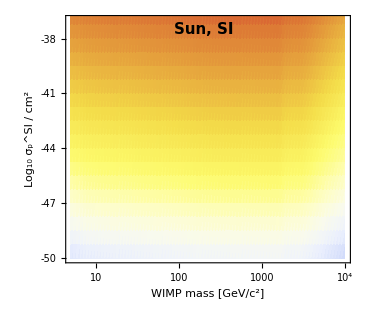
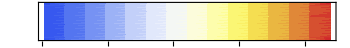

```mathematica
WWSunPlot0=Labeled[grid=Show[SunSIFrame,GridSunSITot[[1]],Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]]],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["~/Desktop/WWCountSunSI10.pdf",WWSunPlot0,"pdf"];
```

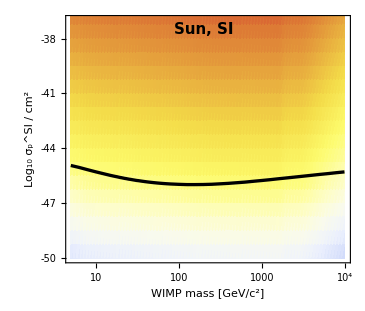
-Graphics--Graphics-

```mathematica
WWSunPlot1=Labeled[grid=Show[SunSIFrame,GridSunSITot[[1]],PlotSunSIσ,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]]],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["~/Desktop/WWCountSunSI11.pdf",WWSunPlot1,"pdf"];
```

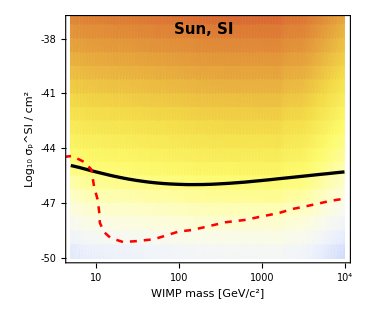
-Graphics--Graphics-

```mathematica
WWSunPlot2=Labeled[grid=Show[SunSIFrame,GridSunSITot[[1]],PlotSunSIσ,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{NuFloorLabel}],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["~/Desktop/WWCountSunSI12.pdf",WWSunPlot2,"pdf"];
```

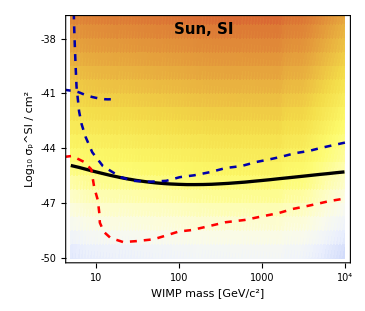
-Graphics--Graphics-

```mathematica
WWSunPlot3=Labeled[grid=Show[SunSIFrame,GridSunSITot[[1]],PlotSunSIσ,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,NuFloorLabel}],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["~/Desktop/WWCountSunSI13.pdf",WWSunPlot3,"pdf"];
```

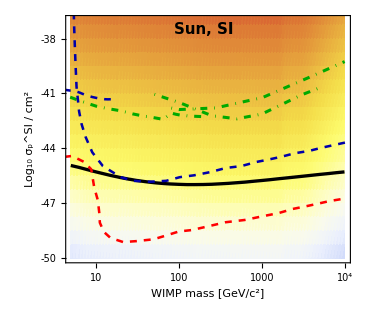
-Graphics--Graphics-

```mathematica
WWSunPlot4=Labeled[grid=Show[SunSIFrame,GridSunSITot[[1]],PlotSunSIσ,WWSunSKleSI1Plot,WWSunSKSI1Plot,WWSunICSI1Plot,LUXPlot,CDMSLitePlot,NuFloorPlot,Graphics[Text[Style["Sun, SI",FontSize->15,FontFamily->"Times",FontWeight->"Bold"],{Log10[200],-37.5}]],Epilog->{CDMSLabel,LUXLabel,SKLabelSSI1,SKLabelSSI2,ICLabelSSI,NuFloorLabel}],DensityPlot[y,{y,Minplot,Maxplot},{x,0,1},AspectRatio->0.07,ColorFunction->"TemperatureMap",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->Directive[GrayLevel[0],FontSize->14,FontFamily->"Times"],FrameLabel->{"Log_10 Φ_μ [km^-2 yr^-1]","",},FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
Export["~/Desktop/WWCountSunSI14.pdf",WWSunPlot4,"pdf"];
```

## Effects of evaporation on Γ_A

```mathematica
ΓSunSIfull[mm_,ss_,fcdm_]:=0.5 CASun[mm,fcdm] NSSI[mm,ss,fcdm]^2;
ΓSunSDfull[mm_,ss_,fcdm_]:=0.5CASun[mm,fcdm] NSSD[mm,ss,fcdm]^2;
ΓEarthSIfull[mm_,ss_,fcdm_]:=0.5CAEarth[mm,fcdm] NESI[mm,ss,fcdm]^2;
ΓEarthSDfull[mm_,ss_,fcdm_]:=0.5CAEarth[mm,fcdm] NESD[mm,ss,fcdm]^2;
```

```mathematica
ΓSunSD[15,1,1]
ΓSunSDfull[15,1,1]
```

1.82069×10^25

1.78061×10^20

## Computation of ϕ

```mathematica
RCore=3.4 10^6 ;(*meters*)
RMantle=3 10^6 ;(*meters*)
REarth=6.4 10^6; (*meters*)
ρCore=1.2 10^4; (*Mean density in kg/m^3*)
ρMantle=4.5 10^3; (*Mean density in kg/m^3*)
MCore=4 π/3 ρCore RCore^3;
MMantle=4 π/3 ρMantle (REarth^3-RCore^3);
MEarth = MCore+MMantle;
ρEarth=3MEarth/(4π REarth^3);

vsur=11.2 10^3; (*escape velocity at surface in m/s*)
vCore=15 10^3; (*escape velocity at core in m/s*)
Mearth[r_]:=If[r<RCore,MCore (r/RCore)^3,MCore+MMantle((r^3-RCore^3)/(REarth^3-RCore^3))]/MEarth;
vE2[r_]:=vCore^2-Mearth[r](vCore^2-vsur^2);

(*Elements*)
AFe=56;(*Iron*)
AO=16;(*Oxygen*)
ASi=28;(*Silicon*)
AMg=24;(*Magnesium*)
ANi=59;(*Nickel*)
ACa=40;(*Calcium*)
AAl=27;(*Aluminum*)
AS=32;(*Sulfur*)
ACr = 52; (*Chromium*)
ANa=23;(*Sodium*)
AP = 31; (*Phosphor*)
AMn = 55; (*Phosphor*)
AC=12;(*Carbon*)
AH=1;(*Hydrogen*)

Aearth={AFe, AO, ASi, AMg, ANi, ACa, AAl, AS, ACr, ANa, AP, AMn, AC, AH};
```

```mathematica
xFe54=0.058;
xFe56=0.917;
xFe57=0.022;
xFe58=0.0028;
xNi58=0.681;
xNi60=0.262;
xNi61=0.011;
xNi62=0.036;
xNi64=0.009;

xFeE=0.32;
xNiE=0.0181;

(*Total*)
xFe54E=xFeE xFe54;
xFe56E=xFeE xFe56;
xFe57E=xFeE xFe57;
xFe58E=xFeE xFe58;
xOE=0.297;
xSiE=0.161;
xMgE=0.154;
xNi58E= xNiE xNi58;
xNi60E= xNiE xNi60;
xNi61E= xNiE xNi61;
xNi62E= xNiE xNi62;
xNi64E= xNiE xNi64;
xCaE=0.0171;
xAlE=0.0159;
xSE=0.0064;
xCrE=0.0047;
xNaE=0.0018;
xPE=0.0007;
xMnE=0.0016;
xCE=0.0007;
xHE=0.0003;

(*Molecular weight of the mantle*)
xFeM=0.0626;
xNiM=0.00196;

xFe54M=xFeM xFe54;
xFe56M=xFeM xFe56;
xFe57M=xFeM xFe57;
xFe58M=xFeM xFe58;
xOM=0.44;
xSiM=0.21;
xMgM=0.228;
xNi58M=xNiM xNi58;
xNi60M=xNiM xNi60;
xNi61M=xNiM xNi61;
xNi62M=xNiM xNi62;
xNi64M=xNiM xNi64;
xCaM=0.0253;
xAlM=0.0235;
xSM=0.00025;
xCrM=0.0026;
xNaM=0.0027;
xPM=0.00009;
xMnM=0.001;
xCM=0.0001;
xHM=0.0001;

(*core*)
xFeC=0.855;
xNiC=0.052;

xFe54C=xFeC xFe54;
xFe56C=xFeC xFe56;
xFe57C=xFeC xFe57;
xFe58C=xFeC xFe58;
xOC=0;
xSiC=0.06;
xMgC=0;
xNi58C=xNiC xNi58;
xNi60C=xNiC xNi60;
xNi61C=xNiC xNi61;
xNi62C=xNiC xNi62;
xNi64C=xNiC xNi64;
xCaC=0;
xAlC=0;
xSC=0.019;
xCrC=0.009;
xNaC=0;
xPC=0.002;
xMnC=0.003;
xCC=0.002;
xHC=0.0006;

(*Mantle*)
xMantle=ρMantle {xFe54M,xFe56M,xFe57M,xFe58M,xOM,xSiM,xMgM,xNi58M,xNi60M,xNi61M,xNi62M,xNi64M,xCaM,xAlM,xSM,xCrM,xNaM,xPM,xMnM,xCM,xHM};
xCore=ρCore {xFe54C,xFe56C,xFe57C,xFe58C,xOC,xSiC,xMgC,xNi58C,xNi60C,xNi61C,xNi62C,xNi64C,xCaC,xAlC,xSC,xCrC,xNaC,xPC,xMnC,xCC,xHC};
xEarth={xFe54E,xFe56E,xFe57E,xFe58E,xOE,xSiE,xMgE,xNi58E,xNi60E,xNi61E,xNi62E,xNi64E,xCaE,xAlE,xSE,xCrE,xNaE,xPE,xMnE,xCE,xHE};
ρmat[r_, i_]:=If[r<RCore,xCore[[i]],xMantle[[i]]];

ϕ[i_]:=(4π NIntegrate[r^2 vE2[r]ρmat[r,i],{r,0,REarth}])/(vE2[REarth] MEarth  xEarth[[i]]);
ϕT=Table[1,{i,1,Length[xEarth]}];

For[i=1,i≤Length[xEarth],i++,ϕT[[i]]=ϕ[i]];
ϕT
```

{1.59351,1.59351,1.59351,1.59351,1.27952,1.32523,1.27869,1.62527,1.62527,1.62527,1.62527,1.62527,1.27784,1.2765,1.61658,1.49874,1.29552,1.63438,1.53948,1.64671,1.35423}